## Routines

```mathematica
<<ComputationalGeometry`
```

```mathematica
SphereNNbrs2[thePts_,theNbhd_]:=
Module[{thePt,theNbhdPts, minDist, meanDist,distTbl,nearPts,theNbr,theNbrIndices,nearestNbrIndex,nearPtsIndices},
theNbhdPts=thePts[[theNbhd]];
thePt=theNbhdPts[[1]];
distTbl=Map[Norm[#-thePt]&,theNbhdPts];
meanDist=Mean[distTbl];
nearPtsIndices=Select[Range[Length[distTbl]],distTbl[[#]]<meanDist&];
nearPts=theNbhdPts[[nearPtsIndices]];
distTbl=distTbl[[nearPtsIndices]];
minDist=Min[distTbl];

nearestNbrIndex=nearPtsIndices[[Select[distTbl,#==minDist&][[1]] ]];
theNbrIndices={nearestNbrIndex};
theNbr=theNbhdPts[[nearestNbrIndex]];
getnextNNbr[thePt,theNbr,nearPts,nearPtsIndices];

indices=DelaunayTriangulation[projPts][[1,2]];
theNbhd[[indices]]]
```

```mathematica
getnextNNbr[v0_,v1_,thePts_]:=Module[{a},
a=v1-v0;
Map[checkPt[v0,a_,thePts] ,thePts]]
```

```mathematica
checkPt[v0_,a_,thePts_][thePt_]:=Module[{b,normal,iptbl},
b=thePt-v0;
normal=Cross[a,b];
normal=Sign[normal.v0]normal;
iptbl=Map[(normal.#)&,thePts];
If[Max[iptbl]<normal.v0, True, False]]
```

```mathematica
SphereNNbrs[thePts_,theNbhd_]:=
Module[{thePt,theNbhdPts,TPBasis,projPts,indices},
theNbhdPts=thePts[[theNbhd]];
thePt=theNbhdPts[[1]];
TPBasis=NullSpace[{thePt}];
projPts=Map[#-(#.thePt)thePt&,theNbhdPts];
projPts=projPts.Transpose[TPBasis];
indices=DelaunayTriangulation[projPts][[1,2]];
theNbhd[[indices]]]
```

```mathematica
c12[u1_,u2_,u3_]={-((-1+u1.u2+u1.u3-u2.u3) (-1+u2.u3))/(-3+(u1.u2)^2+2 u1.u3+(u1.u3-u2.u3)^2+2 u2.u3-2 u1.u2 (-1+u1.u3+u2.u3)),((-1+u1.u3) (1-u1.u2+u1.u3-u2.u3))/(-3+(u1.u2)^2+2 u1.u3+(u1.u3-u2.u3)^2+2 u2.u3-2 u1.u2 (-1+u1.u3+u2.u3))};
```

```mathematica
Vert[u1_,u2_,u3_]:=Module[{c1,c2,c3,v},
{c1,c2}=c12[u1,u2,u3];
c3=1-c1-c2;
v={c1,c2,c3}.{u1,u2,u3};
v=v/Sqrt[v.v]]
```

```mathematica
VorCell[thePt_, theNNPts_]:=Prepend[Table[Vert[thePt,theNNPts[[k]],theNNPts[[k+1]]],{k,1,Length[theNNPts]-1}],Vert[thePt,First[theNNPts],Last[theNNPts]]]
```

## Import Data

```mathematica
Clear[pts1K,en1K,nbhds1K]
```

```mathematica
"/Users/hardindp/Dropbox/MinEnergyComputations/willsMinEnergy/main/Jul18test9.txt"
```

```mathematica
Do[pts[i]=Import["/Users/hardindp/Dropbox/MinEnergyComputations/willsMinEnergy/main/Jul18test"<>ToString[i]<>".txt","Table"];

nbhd[i]=Drop[Import["/Users/hardindp/Dropbox/MinEnergyComputations/willsMinEnergy/main/Jul18testnbhds"<>ToString[i]<>".txt","Table"],1];
nbhd[i]=Select[nbhd[i],(Length[#]>0)&];
nbhd[i]=Map[#+1&,nbhd[i]];
t=Timing[NNbrs[i]=Map[SphereNNbrs[pts[i],#]&,nbhd[i]];]; Print[{i,t[[1]]}],{i,1,3}]
```

{1,137.02061}

{2,133.75215}

{3,133.34023}

```mathematica
Min[Map[Length,nbhd[3]]]
```

30

```mathematica
spheres=Table[
VorPolys=Table[{Switch[Length[NNbrs[i][[k]]],6,Green,7,Blue,5,Red,_,Orange],Polygon[VorCell[pts[i][[k]], pts[i][[NNbrs[i][[k]]]]]]},{k,1,Length[pts[i]]}];
Show[Graphics3D[VorPolys],ViewPoint->{Left,Front,Bottom},Boxed->False,Lighting->"Neutral"],{i,1,3}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
ListAnimate[spheres]
```

```mathematica
Drop[en1K,1001][[1]]
```

{-0.232386,0.398163,-0.887391}

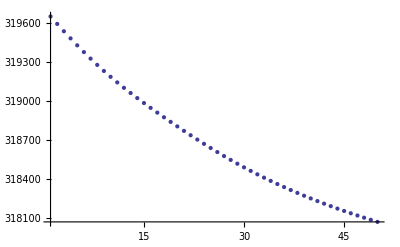

```mathematica
ListPlot[Drop[en1K,3050][[All,4]],PlotRange->All]
```

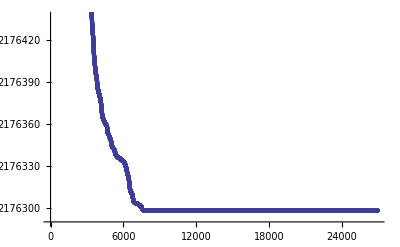

```mathematica
ListPlot[en10K[[All,4]]]
```

## 3KPts

```mathematica
en3000=Import["/Users/hardindp/Documents/MINEnergyCode/EnergyProject/test3000_8000.txt","Table"]
```

{{0,2.21642×10^-12,6.67875×10^9,4.56264×10^10},{1,3.21722×10^-12,2.40926×10^9,1.74956×10^9},«7997»,{7999,1.74187×10^-8,2.1269×10^8,2.1269×10^8}}

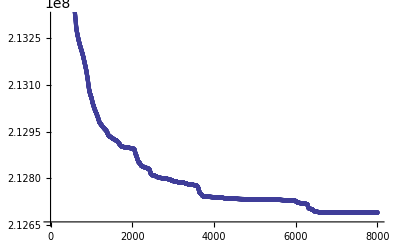

```mathematica
ListPlot[en3000[[All,4]]]
```

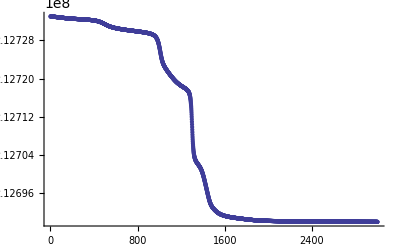

```mathematica
ListPlot[Drop[en3000[[All,4]],5000],PlotRange->All]
```

```mathematica
Do[pts3K[i]=Import["/Users/hardindp/Documents/MINEnergyCode/EnergyProject/test3000_8000"<>ToString[i]<>".txt","Table"];

nbhd3K[i]=Drop[Import["/Users/hardindp/Documents/MINEnergyCode/EnergyProject/test3000_8000nbhds"<>ToString[i]<>".txt","Table"],1];
nbhd3K[i]=Map[#+1&,nbhd3K[i]];
t=Timing[NNbrs3K[i]=Map[SphereNNbrs[pts3K[i],#]&,nbhd3K[i]];]; Print[{i,t[[1]]}],{i,21,50}]
```

{21,184.288}

{22,177.136}

{23,179.003}

{24,188.445}

{25,175.228}

{26,196.549}

{27,178.123}

{28,180.512}

{29,178.588}

{30,178.966}

{31,178.685}

{32,179.373}

{33,179.134}

{34,181.607}

{35,187.336}

{36,180.976}

{37,177.337}

{38,178.593}

{39,177.976}

{40,179.257}

{41,183.111}

{42,180.197}

{43,176.521}

{44,176.2}

{45,178.925}

{46,176.744}

{47,174.769}

{48,175.707}

{49,175.779}

{50,176.578}

```mathematica
Export["/Users/hardindp/Documents/MINEnergyCode/EnergyProject/test3000_8000_NNbrs.txt",Table[NNbrs3K[i],{i,1,50}]]
```

/Users/hardindp/Documents/MINEnergyCode/EnergyProject/test3000_8000_NNbrs.txt

```mathematica
ListAnimate[VorTbl]
```

```mathematica
Show[Graphics3D[{{Yellow,Sphere[{0,0,0},1]},coloredPts3K[[defectPts3K[[All,1]]]]}],Boxed->False]
```

-Graphics3D-

```mathematica
pts30K=Import["/Users/hardindp/Documents/MINEnergyCode/EnergyProject/test30000_4000.txt","Table"];
```

```mathematica
i=20;VorPolys=Table[{Switch[Length[NNbrs30K[i][[k]]],6,Green,7,Blue,5,Red,_,Orange],Polygon[VorCell[pts30K[[k]], pts30K[[NNbrs30K[i][[k]]]]]]},{k,1,Length[pts3K[i]]}];
sphere30K=Show[Graphics3D[VorPolys],ViewPoint->{Left,Front,Bottom},Boxed->False,Lighting->"Neutral"]
```

Dot::rect: Nonrectangular tensor encountered.

General::stop: Further output of Dot :: rect will be suppressed during this calculation.

Part::partw: Part 2 of NNbrs30K[20] does not exist.

Part::pspec: Part specification NNbrs30K[20] ⟦ 2 ⟧ is neither an integer nor a list of integers.

Dot::dotsh: Tensors {1, 3.36121×10^-16, 1.23887675375436206×10^12, 1.2273957199103269×10^12} and {{0, 2.61302×10^-15, 3.50757749497608545×10^12, 4.06728148829462207×10^12}, {1, 3.36121×10^-16, 1.23887675375436206×10^12, 1.2273957199103269×10^12}, « 48 », « 3950 »} have incompatible shapes.

General::stop: Further output of Dot :: dotsh will be suppressed during this calculation.

Part::partw: Part 2 of NNbrs30K[20.] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::pspec: Part specification NNbrs30K[20] ⟦ 3 ⟧ is neither an integer nor a list of integers.

$Aborted

-Graphics3D-

```mathematica
Table[
VorPolys=Table[{Switch[Length[NNbrs3K[i][[k]]],6,Green,7,Blue,5,Red,_,Orange],Polygon[VorCell[pts3K[i][[k]], pts3K[i][[NNbrs3K[i][[k]]]]]]},{k,1,Length[pts3K[i]]}];
Show[Graphics3D[VorPolys],ViewPoint->{Left,Front,Bottom},Boxed->False,Lighting->"Neutral"],{i,1,50}]
```

```mathematica
Show[Show[Graphics3D[VorPolys],ViewPoint->{Left,Front,Bottom},Boxed->False,Lighting->"Neutral"],ViewPoint->{Right,Bottom}]
```

-Graphics3D-

```mathematica
Show[Graphics3D[VorPolys],ViewPoint->{Front},Boxed->False,Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
k=20;
Show[Graphics3D[{{Yellow,Sphere[{0,0,0},1]},Map[Point,pts3K[k]]}],Boxed->False]
```

-Graphics3D-

```mathematica
Show[Graphics3D[{{Yellow,Sphere[{0,0,0},1]},coloredPts3K}],Boxed->False]
```

-Graphics3D-

```mathematica
Length[nbhd3K]
```

3000

```mathematica
Timing[NNbrs3K=Map[SphereNNbrs[pts3K,#]&,nbhd3K];]
```

{186.032,Null}

```mathematica
coloredPts3K=Table[{Switch[Length[NNbrs3K[[k]]],6, Black, 5, Blue, 7, Red, _,Orange],Point[pts3K[[k]]]},{k,1,Length[pts3K]}];
```

```mathematica
defectPts3K=Select[Transpose[{Range[Length[NNbrs3K]],Map[Length,NNbrs3K]}],#[[2]]≠6&];
```

```mathematica
Show[Graphics3D[{{Yellow,Sphere[{0,0,0},1]},coloredPts3K[[defectPts3K[[All,1]]]]}],Boxed->False]
```

-Graphics3D-

```mathematica
Show[Graphics3D[{{Yellow,Sphere[{0,0,0},1]},Map[Point,pts3K]}],Boxed->False]
```

-Graphics3D-

```mathematica
Show[Graphics3D[{{Yellow,Sphere[{0,0,0},1]},coloredPts3K}],Boxed->False]
```

-Graphics3D-

## 30K Pts

```mathematica
?VoronoiDiagram
```

VoronoiDiagram[{{x_1,y_1},{x_2,y_2},…}] yields the planar Voronoi diagram of the points {x_1,y_1},{x_2,y_2},…
VoronoiDiagram[{{x_1,y_1},{x_2,y_2},…},val] takes val to be the Delaunay triangulation vertex adjacency list.
VoronoiDiagram[{{x_1,y_1},{x_2,y_2},…},val,hull] takes hull to be the convex hull index list.

```mathematica
pts30K=Import["/Users/hardindp/Documents/MINEnergyCode/EnergyProject/test30000_400020.txt","Table"];
```

```mathematica
Dimensions[pts30K]
```

{30000,3}

```mathematica
nbhd30K=Drop[Import["/Users/hardindp/Documents/MINEnergyCode/EnergyProject/test30000_4000nbhds20.txt","Table"],1];
nbhd30K=Map[#+1&,nbhd30K];
```

```mathematica
Length[nbhd30K]
```

30000

```mathematica
pts10K[[nbhd10K[[1]]]]
```

{{-0.240037,0.741757,0.626241},{-0.205855,0.709312,0.674166},{-0.206267,0.734053,0.647008},{-0.239246,0.716922,0.654816},{-0.271586,0.724333,0.633706},{-0.268178,0.751646,0.602586},{-0.206094,0.756552,0.620608},{-0.302276,0.745748,0.593708},{-0.292189,0.768525,0.569206},{-0.220824,0.790576,0.571163},{-0.233562,0.766965,0.597673},{-0.257789,0.778445,0.572335},{-0.158955,0.784618,0.599256},{-0.194507,0.778655,0.596542},{-0.182791,0.800837,0.570305},{-0.270376,0.697893,0.663206},{-0.237809,0.690822,0.682797},{-0.304547,0.723398,0.619634},{-0.3032,0.700126,0.646446},{-0.171304,0.757659,0.629768},{-0.173869,0.72941,0.661612}}

```mathematica
SphereVor[thePts_]:=Module[{thePt,thePts2,TPBasis,projPts,verts,indices},
thePt=thePts[[1]];
TPBasis=NullSpace[{thePt}];
thePts2=thePts;
projPts=Map[#-(#.thePt)thePt&,thePts2];
projPts=projPts.Transpose[TPBasis];
{verts,indices}=VoronoiDiagram[projPts];
verts[[indices[[1,2]]]];
Map[#+thePt&,nbrs.TPBasis]]
```

```mathematica
Timing[SphereNNbrs[pts30K,nbhd30K[[1]]]]
```

{0.065021,{13704,25486,16462,1292,17655,29895}}

```mathematica
Timing[NNbrs=Map[SphereNNbrs[pts30K,#]&,nbhd30K];]
```

{1790.14,Null}

#### NNbrs30K

```mathematica
NNbrs
```

```mathematica
{{13704,25486,16462,1292,17655,29895},{12102,10264,24812,9091,5077,21815},{6599,8269,23802,25321,8291,9837},{17586,18662,24955,20679,21591,19401},{3449,4168,7195,11429,17416,2557},{14663,24053,27593,5054,2168,12012},{4829,452,15721,5115,12467,10796},{18228,25485,15777,21332,524,2798},{9056,15185,18408,23014,6404,13270},{4473,21591,14003,23625,28889},{28817,16347,18522,26205,15425,6859},{26146,1135,11413,29135,20935,19436},{10360,4449,5690,1945,28297,14328},{5404,20639,24234,24492,14915,14131},{24805,1611,20062,18514,8152,23306},{28778,5533,15356,28640,13835,21325},{14211,10106,25733,25352,24243,18284,6960},{27011,27614,6779,7170,18708},{9629,26281,6797,21791,7370,29999},{2966,18040,6516,4133,17050,10856},{7635,28878,16333,21300,4770,3299},{28444,27404,9323,6626,23499,2842},{13045,23197,2607,24231,3939,8822},{13102,18607,11132,8645,8422,2000},{22720,5116,19900,4802,22515},{9510,25640,17766,1965,14152,3219},{17728,6232,20743,3891,21004,13044,14008},{12295,13107,918,10416,14303,16262},{24328,10635,13925,14222,21302,27279},{256,3955,503,11207,14815,759},{5527,17838,24659,5470,6858,29931},{24370,10673,4944,26589,25226,3537},{7989,16734,25729,23917,2994,23785},{2918,15704,2886,4695,4463,14804},{17935,12660,10359,16974,16629,22795},{9608,27569,22867,3154,19819,10339},{10315,20362,885,15571,18089,6884},{15779,17752,14130,25884,5188,12286},{20456,24845,20742,2456,17290,8439},{15626,10706,12440,6139,2671,15140},{24230,21959,18781,17814,1072,25544},{356,21521,26687,29368,15355,11735},{15572,23765,17559,9275,24978,9461},{3063,5244,414,20382,13264,17567},{15363,25325,18802,20666,20981,2917},{19870,26965,15720,17564,7372,22993},{28398,14171,19199,26394,26761,7156},{19481,19116,3645,18142,29528,20823},{29416,7739,8629,25603,26198,1425},{14389,15443,7938,6577,25088,21636},{22784,6169,9370,4736,20990,24809},{21100,29646,12795,8604,29743,2970},{16396,26049,21495,19683,9339,6887},{12896,23649,2977,17905,23997,25694},{29766,9825,20466,12709,18133,25033},{20797,15876,15392,1456,13592,7584},{3765,21575,23136,4181,23841,29386},{13595,5104,18279,18085,15690,10456},{24789,23517,23995,24136,15303,4025},{23795,5088,20023,25340,25269,26669},{12308,2782,20586,24874,1122,11717,11057},{27290,17577,24155,22362,23909,23627},{2054,23992,320,19502,2765,2625},{25783,6208,7717,12264,17222,24837},{8429,22102,5155,22426,21715,11785},{3276,17740,16100,29854,11415,1206},{8665,18704,22771,21386,26494,29240},{16195,22571,7556,22267,14872,17931},{5319,213,22694,14908,6776,4859},{1777,18883,7010,27653,18593,23195},{251,22219,15424,2041,14295,4917},{28707,15150,9502,11322,14012,16551},{16802,10035,17469,2300,20701,16138},{9097,20846,13372,904,384,21178},{16617,15847,29319,16222,15342,17457},{12070,19827,4660,22385,28760,9161},{12193,7208,8625,25688,3696,7853},{2691,11595,12330,28414,13698,99},{10621,24923,7939,16359,28150,9438},{17979,28240,21046,8878,9316,18028},{12281,20835,19459,24242,704,29485},{22198,916,29568,29115,701,22293},{23100,17642,3885,3081,3951,11513},{21221,21657,266,3015,11884,26429},{15162,4786,5868,8968,26170,22978},{10730,6905,5706,20709,5510,23229},{3596,24876,28139,17069,12268,3563},{27354,12826,19288,1701,16192,7978},{1645,23509,442,3458,28485,28474},{2648,10058,16446,9858,28661,8616},{21687,28245,1391,10466,10210,15694},{9304,24291,21370,23356,19003,17637},{5089,3723,4861,20278,8436,20216},{2876,25983,15985,18210,19780,21410},{309,10297,15857,10115,5947,1547},{12990,18073,24660,9336,21947,29642},{5293,14547,25704,29163,9887,21704},{7110,6490,19750,29053,9532,17219},{9545,2691,78,13698,758,17424},{2020,29004,5671,437,16012,1867,10082},{26896,22937,27480,19241,10836,5541},{17929,1383,23034,19897,1998,9401},{838,17798,7810,29040,6972,19226},{5377,25409,22574,21749,9628,20274},{29176,6259,12452,13845,15896,857},{27328,18752,9801,7433,23542,7463},{25230,12373,17862,18561,11260,29775},{17830,21844,26930,6050,28061,26811},{23668,15170,18965,25692,10535,11190},{19930,19182,10757,20582,20499,29532},{4039,12208,22709,5638,23425,2731},{23089,8247,11289,2348,1799,14764},{25209,157,7694,28096,9924,20978},{2937,1258,14839,10282,7802},{8087,2533,19318,5934,21415,15326},{17771,6744,8544,2449,21249,18353},{25711,22271,10910,27197,1536,2582},{13942,24828,19081,24173,16665,29484},{28078,23907,12864,22627,29710,28063},{22698,10959,9394,1101,16969,11369},{13977,4522,3703,29078,3410,3720},{19072,27041,2869,21458,16079,2940},{4633,16796,26587,16790,8401,5485},{2633,10960,15400,21844,17830,23160},{12884,18919,5856,18288,12406},{2577,20252,19965,21075,13508,13586},{12187,6643,29489,22026,2684,17397},{23126,6268,7295,11611,5692,10314},{24383,24325,16066,3914,23729,25571},{22964,7241,5807,23859,29731,6098},{1424,18550,10896,28865,20025,14643},{28029,29039,8205,28401,26336,17608},{24544,10085,20395,16512,352,25519},{4369,14522,26240,831,4920,22990},{23373,9910,3461,26280,10782,22967},{814,10614,27262,28067,28990,15556},{512,4106,25415,155,26667,18245},{25493,4241,23317,24795,20600,24542},{18042,23040,23573,9715,16534,20595},{29517,3309,8331,10322,27159,884},{8787,28418,17966,12436,21131,18928},{15258,22785,8332,16943,27768,6143},{28204,4156,24246,12870,22021,1992},{9026,5770,28612,19394,16627,18066},{4569,7843,12157,1901,17652,9761},{19754,1244,18714,25938,665,13950},{4225,14037,28981,26032,21887,17345},{11900,21292,14821,14475,12505,5812},{7474,2549,8147,7068,6439,16677},{29048,15942,22459,10406,5779,4404},{20991,896,16916,6391,19945,19159},{17391,10789,7627,23164,16558,3213},{9505,11069,13412,15493,9913,3168},{9296,25328,18726,28794,5435,4175},{137,25415,23494,19985,6893,26667},{24931,11867,1236,14218,14000,13339},{25576,360,20344,7694,113,25209},{19065,5737,3935,20099,25265,27914},{10577,19287,13840,29634,14967,6646},{7453,16503,26369,22643,21599,7092},{13955,9173,10002,12719,2106,27626},{10815,13023,19165,12959,23359,18187},{19403,6499,27964,9278,5522,9710},{9830,11575,17580,13183,24028,13389},{12003,25295,13595,10456,19389,6501},{339,14915,20425,5828,25559,17481},{5139,25168,21070,16099,1126,28273},{18785,23252,9261,26250,4521,29180},{7186,7303,24934,5993,11025,15817},{29211,17433,17358,11136,10438,2050},{14189,14232,12846,6392,21463,2203},{28328,2858,5910,28180,2727,19849},{12072,21664,17834,14360,4204,21538},{2514,20813,28306,10425,2531,20664},{14741,26502,5043,26163,9120,17007},{25050,15198,10569,3541,440,16246},{18403,14376,4731,9820,591,1094},{13970,20824,12059,27527,7080,5399},{14358,9376,16668,14009,14925,13779},{2453,1680,13693,15707,22709,12208},{7655,3482,9566,22133,871,12183},{23625,12814,11949,18798,11710},{12759,7663,26979,12206,21478,10531},{20197,12478,22340,18822,11103,11510},{8402,14276,28546,24666,5424,20928},{10383,1762,21032,13505,12694,649},{24145,11955,6933,2076,8254,5552},{25092,9068,4955,26573,12971,9064},{22854,16924,29091,29602,29229,24073},{10450,23852,24006,13951,25747},{3240,921,21880,11142,22480,2720},{4346,11108,21900,25124,6924,17826},{27385,27441,13398,2226,28412,3336},{27370,9705,8501,15944,10924,26584},{28907,28552,12511,21030,8944},{23180,25501,15093,13891,7387,10000},{26729,5720,29012,18373,22221,9482},{13172,8681,11258,25971,16678,7871},{24403,2713,29458,7727,23779,3224},{20873,15289,14061,6248,13380,25328},{26732,25998,21378,8916,12143,21604},{20357,13608,24161,26787,25507},{23374,1209,10375,25283,8630,22295},{2252,10517,12684,10297,309,16698},{10727,866,4514,13649,2428,2445},{19623,21627,18538,17936,14661},{17610,26247,29655,27016,7057,14783},{13734,15445,18694,15415,14952,2790},{8661,7349,4684,28630,1688,2336},{15900,20850,25405,24758,13808,23038},{17740,10657,11671,19486,10064,12148},{29653,10690,14442,26341,11069,6277},{29264,12172,21949,22694,69,5319},{11284,24438,555,4788,18307,23220},{14829,20017,14337,20638,18392,534},{7222,18293,21636,4962,23191,19853},{20916,28962,28378,5346,22169,25286},{25656,2970,29743,9021,10175,24854},{16911,13365,19760,28429,13438,17835},{20679,12654,27783,7711,16908,15675,29831},{7350,5289,17197,18248,22305,16358},{3458,4149,6019,25940,28804,9492},{16570,20358,14480,2530,2043,23590},{4781,5522,22269,19815,19636,20140},{16219,6221,284,21269,26961,8461},{18134,14318,21592,23059,27548},{11928,6415,20214,21424,3055,13902},{692,556,23500,8870,685,29236},{1278,14168,15963,12219,4045,14381},{23475,19130,14223,11475,1545,5675},{1220,9955,17317,19433,25491,14685},{28798,377,1580,11202,15006,1413},{25821,18399,3800,16694,8330,10568},{15933,19867,4747,21482,17096,27772},{4975,27475,395,15139,7756,4875},{16340,5694,20472,27862,8470,9375},{11913,15852,21117,24039,11583,21684},{11626,10090,21279,16867,2943,7980},{11321,10989,2381,6753,10475,5407},{29970,6745,22873,17165,2780,14697},{22230,3318,22715,16591,21605,14650},{18414,14515,7092,6683,21003,11230},{12785,8246,26813,6622,23708,28218},{17946,15651,24261,22979,12040,10410},{495,28997,16261,9476,24364,597},{14162,28632,3212,29709,25415,4106},{21386,14914,24964,5486,22327,14436},{27208,18688,1576,18108,13411,20481},{23105,3649,9557,11267,23318,25817},{19313,1743,18657,29774,1303},{1558,8875,22219,71,4917,3887},{5176,12351,12856,9221,9923,10942},{29019,26677,6845,22823,3232,22422},{15564,6855,10468,24685,6045,10473},{18963,9523,19375,9786,24855,22254},{7457,26597,3955,30,759,7797},{5490,14225,2944,8840,11883,26586},{4163,2780,18675,28968,11138,27484},{15272,21068,3816,15366,4943,13723},{14858,13310,17663,13090,29696,15119},{20935,29135,28792,8843,8132,7102},{3815,11306,4430,8135,5946,10485},{18564,26865,16641,23325,25490,7047,16454},{1163,10223,15702,3209,14767,18621},{16972,29783,1173,26600,8548,20856},{21657,9423,9612,2507,3015,84},{19864,8189,8712,25925,27532,17839},{7002,10642,9848,3018,5379,1362},{19570,12562,3943,14785,1006,26648},{27969,588,2395,5971,8053,17496,19275},{7887,9218,22800,18244,10649},{18118,19138,4537,6860,2826,9469},{21544,2293,6897,15262,8696,10842},{21781,2962,20978,2317,8453,3310},{16267,2784,3995,24359,16075,24779},{28070,21173,15962,3433,3446,4792},{6183,775,4896,26553,12517,1552},{23731,14198,3072,22915,14965,18754},{28400,29738,20605,1455,29927,9663},{5367,5101,7030,10988,14524,23270},{25054,12087,12659,14333,21523,14121},{25905,637,12259,25406,11482,5071},{15194,15751,19588,25374,29567,21782},{6221,9428,8392,19739,21269,225},{27954,28668,26302,18801,21642,28037},{20302,23090,4643,13831,3171,3070},{11872,28517,15730,18473,6209,2373},{6614,23939,15339,12170,2200,24235},{11116,5127,422,23455,6506,9085},{25072,11782,22948,18589,3184,27048},{7830,2596,11461,27731,2244,17711},{793,4661,1898,1638,29145,16940},{21174,26454,13766,24635,28980,27477},{11636,4213,15199,1698,9714,16571},{25470,20460,23520,4624,7266,17836},{6513,13385,14145,10414,15794,17320},{20620,24217,5806,13074,14496,16999},{18095,6090,5684,5265,9491,27201},{21956,23886,23663,2514,23070,21802},{12536,2688,25602,9108,25260,4122},{22418,26790,18329,17497,5291,10946},{1428,18806,29422,15982,2759,27519},{23279,5187,26902,24699,20465,15127},{15193,27859,4331,16314,16599,29340},{27296,21741,24606,21781,23010,29385},{12466,20185,20622,27095,8527,736},{20845,22746,19355,2124,17907,4629},{24371,5322,14320,2110,22353,29968},{16698,204,10297,95,1547,11309},{19076,20444,5651,27365,6324,12689},{14012,11322,2178,16737,22832,23023},{22683,15858,19048,11520,20830,6075},{19885,29605,25979,12307,28075,22928},{9746,22221,18373,7869,6334,29664},{13985,21067,13099,25165,5363,22008},{12404,29747,21084,21286,14787,13296},{925,19290,7738,27342,7408,28799},{20246,6569,957,14936,17420,29811},{26448,12096,14562,15464,3787,9393},{23992,13801,4462,7720,19502,63},{17127,10986,18287,18016,11897,28308},{19977,13379,22631,28008,28609},{11361,13951,1187,777,2355,25032},{25476,27099,18878,12222,29909,3321},{25757,6344,22758,15279,11280,1063},{22871,10715,27716,6685,16989,15232},{8624,3316,26026,20257,27578,16835},{24887,26672,6555,21662,18748,17778},{15344,5300,23258,26930,21844,15400},{6606,16321,9809,21410,20256,375},{15798,21263,21468,16892,20633,5169},{5097,24284,22942,27516,2551},{6798,20716,5937,8201,16115,7626},{14356,17434,28081,2470,23095,19997},{21346,16424,16358,22305,23060,13113},{25129,20309,10160,23313,6934,7097,20948},{6315,12396,20008,27715,22678,23850},{432,25064,4200,12811,17516,779},{8519,14131,14915,166,17481,17921},{2497,6531,12569,26800,2347,13799},{25874,10493,27061,13126,29376,8103},{6082,27902,22075,19828,24661,14832},{19887,13774,7051,4745,21541,16814},{28723,24069,12914,8765,12597,12821},{1395,19135,16938,29311,11185,6389},{27611,27713,8296,4744,7295,6268},{8469,4319,19470,12120,17673,24094},{25213,13814,23505,13533,4886,594},{3210,25982,14589,11121,11614,28642},{14609,27383,27313,24125,8707,1152},{10362,17871,29373,12547,6939,20762},{25519,133,16512,8113,7198,29917},{938,812,1332,20333,21442,23011},{20711,23270,14524,26835,25252,18447},{24817,14216,28957,1694,27403,24594,19422},{4255,13532,21521,42,11735,18003},{19631,6870,29361,15280,25563,11243},{1725,24994,2394,16009,2183,8472},{6349,25112,25536,27984,26941,15157},{15885,29928,19014,20344,157,25576},{16078,20782,24677,22336,4295,14001},{15880,26283,20140,19636,4979,29479},{17480,28924,29207,27955,10056,23888},{3059,25294,3165,12972,18509,23979},{25828,22010,7344,26283,15880,7029},{2235,4130,14585,13609,19562,26245},{7392,21576,27787,7509,10271,17768},{18101,4503,18751,23137,2332,23972},{11856,10126,15489,24755,15765,27022},{20342,10396,13149,10674,8642,29760},{14706,14507,29495,23840,22242,25076},{10436,5616,24180,1079,26054,23527},{21183,10780,22717,7879,21360,25208},{14056,23947,29538,12102,29961,4020},{6606,330,20256,24491,7328,7410},{29133,27199,1848,5165,17996,15093},{23443,8703,6656,1580,232,28798},{20692,26251,14858,18427,25465,28432},{14476,11811,23234,20175,12599,14821},{15894,26866,10435,19604,29110,8946},{2208,5509,21006,12466,736,13664},{4824,18247,23871,8004,11563,28205},{3777,14398,5231,22455,22970,26409},{21178,74,904,16927,9620,28402},{3789,19148,25766,21753,26764,25394},{19085,14367,8317,15487,11920,26794},{4336,29478,2541,1594,7677,20497},{27570,11580,19667,8412,14165,25345},{27014,3821,17282,10938,27405,3218},{6752,22956,13639,15458,9512,15929},{18502,17753,21369,27597,11118,8167},{3079,14122,17636,18736,12844,26400},{10788,22743,17995,20539,19297,5671},{19095,11938,1631,1942,4730,8998},{27475,26516,15228,21146,15139,235},{25965,28337,25891,1927,26045,18238},{15362,13015,5724,9154,23495,18156},{5100,22868,2239,16301,4967,1345},{21603,20379,4728,29137,21831,7129},{4905,4145,5173,18587,20457,11743},{18053,1920,27877,11673,21164,23595},{22025,26623,27478,26742,16523},{10033,14883,22383,25880,3421,6493},{28616,10245,10572,11683,10642,15869},{2458,20283,1339,5731,14298,11862},{12593,14552,16567,10849,27998,21282},{12390,13852,14588,14161,14593,733},{28989,11382,27656,26510,23278,22075},{27964,22587,10214,8464,28379,9278},{10269,3755,14959,22458,25110,23103},{18237,11146,12600,21700,27482,17260},{23136,2531,10425,9643,28216,4181},{22905,19074,28300,26714,15263,4243},{5244,26243,8290,1012,20382,44},{8523,22680,4402,19092,25525,11758},{25101,5396,10339,1005,3117,844},{19146,8511,7928,12707,6847,12834},{19622,14669,16945,14102,11716,2894},{15550,25014,25906,16868,751},{27567,3180,8602,24277,21152,18178},{16080,23829,8752,27690,6765,7848},{5127,18674,1409,5744,23455,289},{4918,28170,14075,10034,11411,14539},{5764,22354,26448,9393,7443,12058},{6239,2519,1741,7611,23789,28397},{10769,15179,15039,4929,2406,28726},{24076,22476,5332,29880,28203,8538},{1964,26576,10491,11592,17336,26897},{25158,20091,13206,13229,11751,11007},{12644,19597,6976,26839,15753,23222},{11485,16234,18788,18884,3943,12562},{20130,3019,25064,338,779,20872},{13649,786,4224,27752,5246,17986},{25776,6481,18004,10608,10909,21074},{29047,21792,24333,20886,14631,18151},{22896,24317,7714,27283,10555,1113},{5671,19297,2146,7643,16012,100},{6957,3038,29550,22565,2112,15725},{28866,27493,8009,24608,17705,1439},{176,3541,19840,1732,22330,27073,16246},{6345,4335,22830,26260,22017,13817},{23509,8713,7158,4149,3458,89},{4428,18868,8786,6935,27061,10493},{533,14913,29511,24111,15632,28338},{6021,13516,5862,10514,18569,15492},{21511,1436,10677,3157,9832,24311},{3020,20491,23397,14780,19086,13035},{26838,15512,11741,11349,26149,22682},{3632,2314,26231,6881,22157,6912},{25820,13756,1057,4162,4088,13663},{9538,23362,27106,6242,19549,17745},{20648,12770,23745,15721,7,4829},{9063,17491,24201,1465,4008,4656},{27252,16185,9488,2750,10954,5907},{16565,29767,477,25598,1706,21268},{29981,4061,24409,27428,14061,15289},{9268,8900,1507,3226,8497,11908},{16582,5922,15892,7415,5157,16604},{23478,29045,26028,19695,20887,19273},{13316,22250,23156,4427,19469,23915},{19772,5306,7331,16738,14064,7120},{17824,26618,11802,14015,8029,6567},{11214,9141,4418,21845,13481,7692},{16843,5124,10697,21865,6427,14235},{10553,8727,8398,988,10123,21401},{9959,9761,17652,5085,10200,10476},{2171,4079,26630,3817,4606,4954},{14879,16439,1440,28761,22226,3648},{8041,25516,27194,2039,10201,14788},{6587,4408,9232,20260,17714,25917},{2400,18047,12012,7656,11688,23592},{15432,1959,13064,24985,20122,22603},{22518,11416,8459,26262,17546,7005},{17076,14257,13885,22114,18699,1807},{8058,1531,14581,15306,27672,5362},{9949,22337,23563,1402,5394,9587},{29767,12944,25785,8795,25598,455},{18967,7447,19890,12700,22023,13284},{8962,20373,8216,16657,10323,19137},{14138,28902,20663,19236,3167,3550},{24216,20771,10072,13036,4348,12521},{8482,15554,23091,14793,16421,3389},{27852,26686,27070,18247,4824,3653},{10446,18796,14235,27563,24989,4985},{25581,23150,5434,12052,16513,17302},{9720,5394,9940,28906,1309,25909},{10019,615,17352,6135,5438,1500},{14980,15829,23706,4713,26927,10744},{23822,12672,18160,12209,6635,9680},{27212,8798,17269,23064,19516,12442},{17627,23610,2880,22282,29093,23022,4185},{27832,20623,15678,29582,28894,16043},{14324,16590,12726,2694,10214,22587},{24221,15999,11285,9996,7991,21661},{22269,28379,28997,245,597,19815},{14641,29103,23746,21081,13776,25836},{2298,18022,25667,2623,9938,16976},{17292,22095,17552,5849,11497,27738},{29144,19771,16065,17900,13365,26581},{15501,19798,12841,24207,17086,23799},{7404,5328,873,28154,14637,4622},{20209,7646,3086,14594,28581,1641},{3955,3887,4917,8485,11207,30},{14910,11574,18772,14538,21681,25831},{7007,16832,8811,6072,28660,22166},{5599,21184,23870,7800,29031,17288},{7185,6632,10445,12866,2781,3904},{4740,19184,8781,24484,16828,24494},{21467,4607,17148,13761,11646,29546},{27120,6323,10448,7811,9009,29428},{12015,6130,19621,4439,20318,22543},{4015,19465,4106,137,18245,13155},{24105,17836,7266,28739,4956,25829},{22867,20158,23080,27517,5197,3154},{27833,10926,10651,1181,25524,23249},{10274,7486,28600,28916,22239,22895},{4166,20757,29753,18622,530,8379},{25283,17975,20989,7729,1452,3708},{24907,11239,16697,14606,10500,15357},{531,841,11687,6464,20515,16228},{29274,18725,18361,23001,12943,19021},{3188,28659,10696,10291,6547,11966},{6193,19006,10292,4326,7858,24564},{2798,8,21332,18196,8603,26343},{6830,8641,15200,2173,16496,4854},{25096,13225,15871,7538,23076,10758},{10613,14951,29895,15954,15040,8007},{16020,24860,17934,16184,13298,14032},{12068,14116,4096,17896,29036,9701},{8379,517,18622,13169,7703,28427},{3845,23360,841,520,16228,13963},{2776,20864,22604,6422,12270,22241},{19699,1562,14913,444,28338,2026},{8610,14829,215,18392,4226,26298},{11085,14460,20088,5633,903,6366},{26682,16862,19449,28382,25262,790},{18788,20996,5428,26610,2565,18884},{29632,9929,24757,13683,16647,3911},{14638,13708,28970,29702,15305,27273},{26905,18143,13886,18213,15203,20188},{2162,25773,9667,18541,9751,28124},{28274,18455,29837,1766,21185,27553},{17520,28765,3605,13510,7122,7028},{14760,14424,7359,11290,3277,20794},{8406,805,6016,8727,10553,7899},{24074,16754,21405,1588,18110,16609},{2508,9053,16187,24213,10388,27580},{23991,3920,12662,25236,16902,24430},{20525,12942,12474,23304,18728,18872},{1477,27448,5493,28871,22294,6425},{15028,23702,5009,24402,15377,6009},{20817,23114,19087,19577,28137,13467},{25017,27645,7329,25186,3867,4278},{28570,24117,17188,3953,3623,10483},{24438,7863,18813,20858,4788,214},{7112,18864,5166,23500,228,692},{27231,18148,9392,20510,17174,18650},{12677,10434,25621,24763,25912,9472},{791,6381,2365,29946,18164,7114},{25792,11860,22135,15685,12523,29793},{28023,14836,23193,12069,21497,19902},{28716,28296,20541,21939,23757,28350},{4036,13641,5669,18342,21044,24244,6781},{9404,7234,1422,2522,827,2141},{11609,14591,27612,3519,18591,15956},{20221,28331,29886,29756,1125,1578},{20308,8465,4629,17461,23385,28466},{18846,17090,22138,16980,20445,18584},{27653,4196,4773,25687,19252,16757},{14365,28681,3099,25272,1796,9220},{14559,20772,19531,12766,7994,1713},{24134,8876,25329,8151,3562,4883},{13563,12383,1721,17522,24943,17340},{2368,7358,19882,27717,4365,12278},{771,1202,18428,2572,5514,15088},{16157,4813,19831,24522,23268,26201},{6004,7360,28129,19868,24625,11056},{13314,7493,14002,17875,1676,25070},{5639,29607,8758,17502,2518,25484},{9686,18791,11288,21720,29796,19487},{16576,29062,20577,11134,25892,3710},{10289,9357,4976,28034,1509,21116},{18213,26293,5660,2438,3848,25254,14193},{28604,23213,23280,8489,24058,27219},{15897,11629,3897,29380,11033,28481},{20336,11404,19645,26852,22616,5979},{16231,8255,9251,20502,10841,5836},{23178,15492,18569,2395,270,27969},{19036,27193,23892,27309,29684,1065},{22960,4949,28244,13874,728,2819},{1094,177,9820,27843,16475,10777},{26655,22320,23354,1828,18993,14543},{24998,25241,20280,6837,23767,7226},{29131,25213,348,4886,14693,4023},{6851,20751,23349,18837,24394,7440},{24655,7866,25163,12931,29572,18469},{19815,495,245,24364,12495,29303},{1656,29688,26644,10771,27861,24911},{23043,5805,24893,29730,23753,20960},{8830,25180,8826,14366,25058,29531},{1571,12425,17795,22931,10447,19624,20419},{8093,25996,26322,29871,14629,19024},{14157,16212,5206,7728,2520,26834},{7936,11779,22807,19237,2983,17791},{19873,26704,12587,6051,25930,18568},{22647,15219,16431,10324,23880,28838},{23120,24135,13125,25100,20643,19377},{15151,11953,19613,21006,5509,14602},{14920,1066,26884,22721,9189,13843},{1194,2529,17950,3630,28770,2165},{1112,11623,1415,14691,8809,4048},{25587,25753,11137,20963,26198,1425},{25589,29359,12657,24027,28384,3642},{9769,5303,6067,20145,23418,8266},{22481,6893,23561,17352,487,10019},{4445,22440,10065,17579,6963,13145},{3965,25351,23102,29239,24555,20301},{25093,3168,9913,14600,13085,19023},{21310,1983,19876,20492,22781,19075},{8577,12723,8883,11425,9776,22777},{22131,12327,1441,5978,17899,9046},{23891,9766,783,28569,27668,22341},{16817,3502,3829,5913,27451,27175},{4292,4876,27884,26165,9909,27656},{1325,5680,26178,20279,6911,12522},{13061,11603,6062,22871,13993,10358},{23917,24219,23277,7658,28593,2954},{769,1854,4006,3444,11774,27780},{15807,21042,21026,4443,10399,14582},{2839,12565,8546,2739,28501,12502},{14046,14247,26856,25554,16605,4261},{16170,10839,16666,11013,2995,29132,4501},{20543,6884,18089,17523,10633,28223},{1326,24596,12468,15192,29153,3900},{4717,18382,7882,1044,26660,13018},{28822,24938,15499,18616,25352,25733},{10963,7351,752,12259,282,25905},{13921,19973,22313,16320,6876,16328},{5900,17852,3544,21797,16417,27008},{19955,27789,21535,18673,6910,19649},{19385,24469,9296,4175,13539,25931},{19391,12969,16704,19905,23869,14781},{11965,28500,27368,21814,19441,7548},{14595,1156,3304,17449,13642,17989,10579},{19051,11720,12757,697,24516,28235},{26022,11192,14410,14031,21448,25087},{18636,2660,21660,1930,2013,13959},{4642,19127,3792,20392,18860,20708},{9646,10383,186,12694,22563,3972},{12962,16908,1477,6425,2601,9185},{19472,17690,11700,3925,726},{6557,20599,11193,12310,17952,5561},{25068,11374,4863,16560,13491,27732},{18893,6551,15362,18156,1250,29113},{2567,2009,14040,12679,3899,29470},{10778,7427,20849,5696,1760,14846},{7960,5007,5929,12006,27432,14200},{13451,17121,3883,6071,11204,22484},{20228,9022,20073,14803,16518,20244},{26622,23481,10577,6646,7981,21313},{14628,1666,16351,1244,19754,27846},{19455,23171,20888,23281,5384,6676},{2120,12615,1144,16968,28627,22053},{18392,20638,14648,23741,26294,5392},{13950,146,25938,11750,27157,24895},{29989,2854,28531,24323,24549,2329},{13913,2831,29801,26805,29363,17489},{16481,5331,21727,14135,20484,24637},{20740,2340,6219,16366,23919,13084},{21023,21337,21963,5597,7607,2182},{19043,20943,20798,27198,7313,16622},{18700,18596,950,25561,28174,29848},{15435,2482,22213,22766,11246,21265},{19318,26441,29065,23953,17709,5934},{17022,28946,15025,22726,14339,14083},{27830,20030,28803,18656,20658,27842},{6630,29309,2136,19737,26917,15877},{23695,27384,29242,17405,29697,2732,7018},{23173,26772,23833,16152,19920,23432},{19201,28956,5919,10689,8668,25435},{18739,19399,11956,18169,10741,21154},{25550,13857,11469,29034,21266,21380},{25236,16602,26225,17284,12357,4191},{9265,3118,3094,14887,23338,22907},{29236,228,8870,25119,3062,7113},{2804,23737,1955,9962,2696,6854},{27775,20189,5773,25364,17133,22499},{29804,9454,14017,19970,9896,25642},{7823,20171,23993,8829,2167,23377},{10390,7248,19637,16394,23541,27176},{27129,23547,11164,10379,1914,5068},{21726,7112,556,228,29236,19205},{15993,18438,29740,2777,20943,19043},{1584,20945,14924,2188,24810,5051},{22288,22525,28397,16015,26019,4896},{25661,6791,27552,17831,18906,21653},{645,12757,17760,11000,24516},{1814,13722,9220,25622,21213,11896},{12885,9613,28445,25614,3100,20349},{29789,19891,3634,21466,18762,2725},{22293,82,29115,15468,7821,2602},{27034,26826,4119,27225,5428,20996},{12101,6947,11527,11107,26766,26058},{29485,81,24242,13569,16584,21031},{6145,13746,21425,24988,26615,17201},{15058,6943,11002,17458,29064,3211},{21786,18303,9248,19179,27270,3529},{26147,16529,20187,8034,22043,13317},{25504,14561,20124,1655,4628,892},{27152,29231,24280,27458,18256,1179},{14629,29871,20157,23571,28258,19062,16578},{3356,16158,4918,14539,19174,2490},{21293,26187,26221,22259,19358,8162},{7072,23292,4637,28221,5925,21545},{12694,13505,20843,1073,6146,3312},{2137,3532,23056,8075,5284,14474},{24052,27574,16237,28020,12244},{26239,29732,16370,6407,6722,10562},{3882,1718,16563,1696,7657,16199},{14317,21619,27561,9516,15863,2754},{3588,21151,15132,19918,12887,7327},{6553,17313,10360,14328,23468,7232},{6368,22186,25633,22098,12570,17689},{27116,18120,6304,6138,14210,18932},{29846,29161,19191,4484,27540,10071},{8635,19472,651,3925,29795,4919,9519},{1191,4899,18985,1897,4812,10145},{2819,590,13874,21585,28662,13287},{18268,6223,11815,24024,12349,13401},{22678,27715,8967,10610,19338,9687},{1105,9851,20245,4948,2493,4994},{4301,2191,14374,25250,18422,12214},{22339,12390,407,14593,11314,17857},{18492,4029,4167,17533,17366,8933},{9015,3922,24348,14961,7752,4940},{13664,381,12466,306,8527,12632,3064},{28900,12045,27256,9571,16805,19713},{6260,10845,16107,4400,23193,27589},{19786,26214,23937,18116,15020,13996},{15472,14772,5002,11543,20754,16883},{12332,7782,7616,1050,17294,27322},{26398,11197,26362,2603,16791,9399},{21709,21313,7981,23054,15253,2888},{2006,3166,12028,28421,11421,4113},{12628,9229,22628,11680,10612,1399},{23534,14792,19909,1372,11319,27898},{19616,28237,1868,4992,24728,19206},{1987,14957,6420,8612,4475,14147},{4017,27280,10089,18460,8750},{18343,14369,7895,7485,20270,23648},{13254,15550,419,16868,20986,4926},{7351,6154,5163,28116,12259,637},{26534,28234,22981,16628,15448,28531},{8536,6714,11340,27669,12755,2048},{16100,12704,12738,5478,11860,29854},{2422,7577,23497,16223,25011,6456},{10997,28186,28588,8502,6919,4644},{17424,99,13698,12413,29339,28209},{7797,256,30,14815,15567,25683},{21891,23909,1620,25196,11367,19300},{22957,19793,16406,17078,16439,22367},{12375,3435,26544,3536,5048,6096},{2443,18463,17300,18696,7629,6483},{18646,7554,2400,23592,28093,18526},{1859,11967,5932,29547,1947,11905},{6275,10944,9553,13943,2361,19547},{25841,20759,25055,26344,29452,22107},{24945,26783,6712,9838,9812,26259},{7206,22252,1854,628,27780,7988},{23091,15497,28275,9031,6287,14793},{23869,19905,1202,575,15088,9885},{23019,20506,24206,7123,20098,22646},{22427,29016,28400,9663,19681,28942},{4497,10372,887,9907,15541,23628},{24788,12860,22288,4896,277,6183},{24330,24723,11839,16378,9948,21062},{323,1187,9712,23752,15512,2355},{13821,29703,24108,27013,26737,11080},{26709,20872,432,338,17516,12641},{13359,7441,9785,27474,3836,4486},{28184,15383,4022,20223,8980,28177},{4436,14974,4553,1938,10246,19458},{9766,27321,26122,7621,28569,622},{24428,11766,12016,2611,5069,3549},{9638,1032,28571,6864,7940,10151},{4514,27700,12898,4224,433,13649},{18683,25062,3641,10719,20150,21093},{21708,8336,10057,18269,7574},{21698,6634,5461,2415,23925,8100},{26682,536,25262,6968,18056,15562},{22127,8751,6381,559,7114,4028},{21147,16329,29181,20624,8615,26537},{9821,17741,9583,4661,292,16940,7147},{14051,11947,21260,10702,17082},{26515,29882,25909,2083,22215,13543},{10999,16910,29055,22418,21838,21612},{18694,17948,17103,11459,18710,15415},{10534,20019,25586,23154,23986,5964},{27179,18003,11735,10045,16010,20563},{18805,19136,7762,10428,25959,10952},{26542,12369,28527,8069,21828,24010},{5496,2948,3158,8619,10672,23645},{9246,8737,20207,1184,10230,22411},{4592,27536,20089,3159,2253,3439},{21734,15041,26955,6016,545,8406},{27349,12117,25948,28764,14309,25651},{18654,29960,20225,2149,14986,1475},{13838,19908,5150,24116,3265,22715},{4109,22444,18972,6319,24209,23861},{20635,22739,28976,17370,23047,20718},{3446,3433,6995,8374,7436,8733},{25775,26519,16106,1332,353,938},{14746,2240,28876,14509,1330,26384},{27003,19792,10614,136,15556,12023},{11318,23488,11577,7409,9257,8594},{25580,4668,29911,23106,1274,4077},{24726,29782,26426,5659,3216,6739},{29765,27407,20024,8869,10607,9227},{11031,23448,8318,11149,6148,6691},{28684,10042,14489,16340,24537,19020},{20116,21853,14413,25502,25289,14368},{11049,28932,7968,9578,5980,18672},{12682,29052,13427,16084,5839,8632},{12889,1709,23557,19989,12359,8582},{24395,22973,27654,23155,22235,19464},{25986,27505,29169,11388,21973,14034},{2141,564,2522,18257,12954,11666},{23143,24776,6098,23702,15028,1575},{28786,28389,17708,11086,21850,12529},{986,18280,15673,21331,14800},{134,26240,18383,18681,24392,4920},{29289,24706,28547,2297,15438,28933},{28605,16460,14066,21359,17717,26319},{2289,8908,2398,5719,28934,4753},{10134,16989,29987,10718,7731,24915},{19728,26944,16898,17824,6567,12130},{4157,2871,17935,22795,7131,8321},{3045,21972,17798,103,19226,21474},{16307,23552,14343,25700,8875,24771},{19215,1279,14770,22893,21272,26706},{23360,9969,2993,11687,520,531},{9360,21363,4236,26898,14712,21437},{4739,27531,25479,4318,25988,8088},{3370,25101,416,3117,28181,29220},{28215,9421,28212,7733,1407,24536},{14635,13019,1315,16411,970,4997},{18899,863,20251,26051,7163,29924},{5962,1579,20615,11472,12111,24752},{18707,3967,27232,28189,26627,5513},{26419,21652,13316,23915,25004,29718},{17020,28745,22535,4841,20364,6112},{27797,18100,4972,20993,3054,18358},{6818,4386,18574,27284,23576,6064},{3946,3540,922,12335,2628,24646},{14651,16131,29167,5929,5007,23523},{16462,22358,18335,19017,27933,1292},{20166,29176,105,15896,16338,11186},{29707,23961,7510,2172,26288,24532},{7825,17147,1871,23578,7277,23882,2343},{18136,15683,6191,14772,15472,29715},{27032,23203,19576,1468,29874,4680},{9383,4516,15164,28043,29914,9107},{28556,12249,20251,847,18899,8773},{18987,24387,7589,3366,17200,11633},{24904,21322,26966,9441,18350,17474},{12031,9677,29104,4514,205,10727},{11638,3572,4168,3449,9328,3033},{10462,3520,7300,13677,15169,28972},{25088,6577,4683,15633,28387,5640},{19379,18825,2558,22622,5637,14754},{4482,12183,181,22133,29433,12848},{1601,26606,23305,28200,18532,10016},{5328,19926,28289,20628,28154,501},{25107,10911,15172,28950,20051,28448},{22774,19956,9045,9451,22436,6715},{5341,3862,14300,23166,19556,23079},{9184,18076,5343,17485,28117,17869},{3076,9582,13299,4262,27648,2307},{24687,15647,22999,22250,13316,21652},{1790,26478,26396,882,29151,26008},{6711,21305,9365,14888,29746,16509},{880,26396,19249,10722,9966,29151},{14025,22054,9703,5953,7968,28932},{14919,29517,140,27159,10823,26837},{20362,15326,21415,27305,15571,37},{21703,19775,19540,11853,7641,20294},{10372,24996,13982,11672,9907,774},{16433,25080,21695,7177,10017,3929},{19506,25071,2523,21499,21738,27847},{11934,5733,25404,11753,18445,23860},{15837,17296,6955,9498,13837,6408},{19675,25504,709,4628,21301,5673},{21286,28861,29806,6554,20591,29935},{22673,13429,7279,23649,12896,29182},{25863,24171,8394,26983,26180,12145},{24465,4800,23512,16916,151,20991},{6668,14527,4363,19609,936,10434},{21787,2658,17662,29736,17139,16037},{29395,15699,15238,15635,26169,2753},{18419,8026,29220,8573,28241,12512},{28724,13223,7407,21627,19623,18957},{19766,2294,4388,29648,13789,8268},{6366,535,5633,17087,8345,3971},{74,13372,15417,18216,16927,384},{28339,28573,2956,3554,23124,7386},{13802,9480,16888,24290,22523,10547},{24159,13164,11019,16675,13502,6519},{14423,4407,21651,18664,23489,23973},{29114,20447,22155,1116,29903,20095},{1772,15060,15752,14156,19909,14792},{28376,9594,13552,11691,4787,6347},{18579,27145,23395,13184,15073,13901},{9985,8098,2981,18633,6832,9704},{24324,15541,14005,23549,19900,5116},{28507,9998,15135,9131,6230,25633},{1282,14808,13762,29568,82,22198},{23392,22292,2616,6856,7139,17959},{13107,13234,5425,11865,10416,28},{7037,16399,2443,6483,2457,21373},{12114,7482,23855,16744,9460,29410},{26445,17738,20174,21880,191,3240},{3540,13657,6241,26017,12335,854},{29609,11336,25945,16830,26227,2932},{23311,19278,27946,19666,15330,10567},{6895,5152,19290,317,28799,6387},{25448,14720,20995,16149,21773,19521},{28815,17688,21355,6269,22387,17319},{22498,11834,10361,29084,9146,21987},{24462,8881,8328,19312,5409,28191},{28133,23318,2058,18570,11919,14387},{23088,29341,6816,9992,20813,23663},{13176,8168,14150,23161,14863,21256},{7021,5447,27738,26561,21454,12066},{13008,11704,11494,15966,8373,8202},{13238,2125,17928,26965,19870,1174},{897,19609,29274,19021,25621,10434},{14571,23440,19980,27505,25986,13896},{19733,25775,812,353,23011,21900},{16679,2791,9702,25274,27281,5420},{19782,25686,13981,29843,23783,11504},{10107,17916,20408,10356,9806,11213},{17880,17146,8474,6799,17658,8810},{8486,14660,18087,13346,14644,3518},{12669,27608,24410,17235,16244,5065},{5477,24010,21828,17382,8116,15268},{26718,20485,14518,9632,11675,25879},{14781,23869,9885,21633,29689,11828},{14065,9574,14212,29900,3618,22508},{5170,1934,24264,11737,4663,8942},{18596,1466,7004,3343,25561,672},{2122,3443,1313,15793,15301,9089},{3053,24916,12154,19082,13283,4294},{15601,5688,25074,5413,22462,8633},{27678,23944,3639,29942,19390,3143},{26521,17848,27362,19772,1600,7118},{29551,11905,1947,21696,23433,5593},{6569,21582,27823,4910,14936,318},{15316,10284,22755,28886,2984,5937},{9213,17215,10770,27236,5586,8267},{8880,12532,8475,2512,18181,29325},{10114,1996,19885,22928,4768,3639},{3835,3420,8279,4353,22531,4512},{17708,5881,14879,3648,24086,11086},{5993,18186,29918,13265,17465,12970},{22881,4460,10662,1513,6785,4515},{21372,13868,8530,26358,26751,10053},{16738,28475,3130,4619,2552,27021},{22545,27509,16361,5135,13081,16323},{14614,29759,20997,21924,28992,11282},{4997,846,16411,9180,7560,18580,17968},{9653,8665,29240,12762,28245,23910},{1864,19826,24617,11624,26302,28668},{15707,2856,8907,10532,22423,23241},{26543,1283,12695,9745,22180,21374},{6073,20356,29292,13424,28028,28110},{23225,2086,15758,9769,28430,5003},{14551,27526,7413,14599,27221,24820},{22178,13785,16579,19656,3924,11874},{29164,1736,1353,23214,16984,20238},{27946,8852,1746,26031,24822,19666},{5376,10335,19407,23931,18660,17384},{19707,27540,22516,18642,3248,17950},{5305,27012,18646,18526,12561,26447},{24483,19420,17368,9188,11676,22917},{24733,5887,8479,28237,19616,9371},{20250,17439,18280,830,14800,21065},{13740,25616,24057,2934,12503,7237},{465,8398,16282,3404,19277,10123},{12432,29152,17184,23020,16498,22793},{2547,15402,23416,23399,9503,9211},{28871,28921,24101,25857,15016,9425},{13501,21331,20745,7718,15708,29108},{2816,9330,5948,22922,21768,23324},{14097,6505,4205,8367,21785,26024},{11362,20655,15520,8775,6357,15480},{6879,15456,9945,14020,15177,18301,26230},{7732,15851,16071,3781,25019,5102},{18413,22605,21761,21716,20402,7915},{25487,18534,10830,8801,15223,22539},{2759,15982,3813,6258,27347,13077},{20657,11666,12954,6288,27386,6760},{9266,14753,20560,1936,22689,6371,11895},{21089,22856,8013,15523,23345,12095},{25362,18598,2887,19437,18453,21808},{416,10339,19819,11031,20018,3117},{26648,269,14785,19183,2199,15047},{8320,14824,28752,15737,5556,28560},{24208,12423,13482,23128,24416,25275},{13016,26131,14766,12910,9539,25304},{2047,15419,3833,5001,7816,8807},{11206,25697,1653,13037,20558,6828},{414,8290,6912,9338,5579,20382},{1769,27196,4117,13162,5147,7455},{17438,23182,18144,12708,25121,16506},{22898,22226,22064,8882,7331,5306},{26607,3788,17466,24054,17028,26072},{2679,17735,17236,13503,7146,6338},{7019,23048,24589,8057,25056,29630},{11089,6294,12680,19101,19346,15118},{15935,26660,3478,26908,18496,9101},{28386,24491,4965,24065,16955,4701},{17701,14205,26938,21829,24953,3573},{6392,12176,5561,18320,2532,29282},{5125,16995,24115,9378,7496,24062},{16748,27959,1923,13489,7048,6568},{27547,8721,12622,5999,11901,13772},{6794,24847,28800,12465,25705,8122},{4303,27174,20144,2187,2575,1808},{20068,15397,27278,25505,3460,18478},{23247,10500,9433,23290,23181,27412},{13539,4175,5435,9464,25392,10504},{23814,28391,3417,28571,785,9638},{4744,18981,16812,1626,1459,7919},{7893,9152,13406,8335,9518},{19673,24649,3917,18549,5814,28807},{21390,1660,16390,5101,5367,15450},{27281,25274,9372,12980,4853,26316},{7731,10718,23121,25230,5843,7078},{4090,19800,13557,23883,12129},{29216,29567,20292,11938,19095,26971},{27594,11620,11929,25630,12252,8909},{23286,22907,23338,7898,24679,22036},{23366,8689,15814,29245,18023,29268},{635,7882,27186,9194,3478,26660},{10326,9168,25377,7889,19825,15537},{22515,4802,17159,4394,1299,4696},{19185,12099,16490,25160,21707,19120},{20674,15780,16561,26958,2871,8456},{7215,24070,2360,15572,1767,12291},{17294,741,7616,19898,1517,4447},{25952,26138,14701,25341,28735,12822},{28784,3354,15098,23693,10329,27046},{26639,8080,12428,8999,20000,14395},{3290,12244,24056,19721,14949,16458},{17813,16492,22975,10343,29393,11002},{6060,16863,25229,29717,2027,19027},{13756,13416,7130,24143,4162,450},{28970,5035,5316,6579,16730,29702},{14597,15998,10177,12791,7282,11940},{25291,3706,19567,10374,6201,11174},{20965,1338,11112,27638,29501,15771},{25832,26794,11920,15780,20674,4666},{21394,25757,325,11280,26439,28002},{10932,12908,5109,13106,14452,16423},{1339,19036,589,29684,4474,5731},{11988,18162,9954,26884,609,14920},{1136,5729,5204,20321,21047,27867},{22460,28393,22831,22038,8263,27461},{29200,17318,18973,5465,11531,7892},{25171,18367,18060,29475,28577,13535},{18267,14210,12983,20217,11311,6343},{25544,41,17814,22350,20322,2775},{715,20843,8304,19911,27375,6146},{21879,5607,29369,5870,1426,26644},{28581,14594,15341,5527,23380,29457},{26759,27325,17430,1563,4159,6633},{21745,5299,7033,26423,8971,3201},{11624,6534,1494,3679,19770},{372,24180,28674,15862,16072,26054},{14610,18921,15899,22762,19840,3541},{28289,19866,14830,9317,18173,20628},{18574,2898,25714,24321,2062,27284},{21830,12833,10120,8297,29347,22450},{7793,24508,12648,14348,2669,24705},{6636,27085,18583,19680,22791,3721},{7642,13771,4826,25468,19587,7179},{12123,5156,9484,12026,21076,3259},{8977,15027,11227,27718,12985,8013},{2821,21517,6006,21748,25647,8283},{10429,6194,14638,27273,15934,5469},{8912,16373,9646,3972,11544,4995},{24908,4084,24854,10334,16451,1862},{28770,3630,11231,11805,7805,26442},{5613,18403,177,591,10777,24609},{15879,28171,19740,9870,10198,29855},{17552,12386,5464,12845,7582,1652,5849},{21547,23107,27754,21800,12955,25336},{12902,7166,7216,3040,19566,25537},{28511,6862,24539,27413,17653,20177},{16238,13044,29993,27492,14564,10127},{120,9394,9854,27755,26325,16969},{4941,19142,28633,15624,17955,5713},{3192,23539,10927,7840,5452,19948},{17310,17675,14673,3874,10848,18459},{2361,13943,9851,731,4994,6528},{10571,27662,29005,19938,6029,19806},{10612,11680,27511,3931,13752,18686},{1986,16730,21917,13720,28291,16422},{27222,28142,26239,10562,12601,12490},{12247,24292,13741,6526,6202,7973},{14899,3147,3551,24865,15895,24077},{15029,3749,11623,611,4048,20161},{22896,436,10555,17243,16938},{1640,23904,25842,17105,7093,3484},{2043,2530,5884,5492,6330,5439},{25781,19316,10721,22155,909,29903},{7946,24301,5697,13889,25877,4356},{7876,15525,22936,24145,10211,16820},{5610,10239,10735,23545,8322,9822},{27090,1817,10647,14994,16226,12589},{7471,1230,11807,10989,11321,4006},{11717,61,24874,8610,12491,26585},{25042,1248,29120,3610,23261,21103},{28911,16121,5361,27628,21683,29577},{1578,566,29756,3974,11550,9581},{27911,28273,167,16099,26649,21320},{16985,19134,17904,18298,11799,27849},{16265,9810,2291,3307,4115,24096},{20375,6430,9543,23370,17042,14748},{14087,19358,5918,3731,11713,15975},{11865,25790,25106,13562,7300,3520},{2734,21680,9799,16928,21744,20040},{9074,7930,10965,15240,26934,18994},{22398,6222,24080,17378,14738,14840},{11941,15670,21823,11413,12,26146},{2498,20583,5729,1067,27867,27924},{6403,3293,13499,13692,10014,15592},{1883,21376,21876,18077,16151,23890},{28622,21795,25678,3923,18632,23007},{29304,6328,27703,1212,5941,12380},{29443,19884,10556,3612,28541,14194},{16870,15789,27279,26377,14478,19633},{14718,14207,22903,16821,14129,9110},{12615,22684,8599,4284,16968,663},{12437,14955,15332,6262,24949,1958},{11929,6188,7247,20033,10980,25630},{7412,18994,26934,15933,27746,15667},{16764,19147,5136,26471,5685,16341},{13712,5314,21702,15345,26875,16589},{14508,22665,4685,29097,14273,6241},{17606,14949,6364,3397,23902,29902},{18132,6707,14609,350,8707,2074},{19228,24638,11113,3026,12623,4627},{28027,9739,5538,25386,1851,17283},{14655,27398,12090,22430,13859,20225},{1690,11099,3304,644,14595},{22904,11770,11198,1280,5354,10377},{2565,26610,23212,17605,26813,8246},{22845,2106,27626,21896,23530,10026},{24245,26877,9499,7299,19805,22507},{21335,20527,20105,25048,27450,25067},{21837,12888,10648,19520,12587,26704},{26668,18769,10223,264,18621,10215},{11457,8509,26075,18379,25001,4780},{25138,22152,24515,16085,13770,4481,22039},{2792,9787,14895,24208,20011,10773},{13524,24791,5928,8551,5004,29373},{28059,17154,13865,11777,11297,7465},{28880,25173,23087,9345,16728,29758},{24749,28412,7985,11706,9604,27057},{29345,21589,2378,2113,14440},{24520,25181,18682,7574,6531,15886},{29783,23376,2150,10949,26600,265},{19284,13238,935,19870,17980,14796},{22672,21201,3926,12324,8552,6875},{29661,23298,22165,3214,27941,8831},{15910,6119,10759,5551,26775,14789},{28173,21905,19505,17514,22875,9049},{27492,27152,710,18256,26988,11952},{1268,19000,29057,4444,25436,21534},{515,10651,7995,2708,3479,25524},{27401,11863,24768,6525,10010,17124},{18356,12544,7143,3547,20949,25451},{10230,803,20207,24087,7789,20118},{10532,29362,5348,19008,9385,18615,29672},{12210,19644,24497,13945,7359,14424},{13951,24006,16304,9712,777,323},{14886,12155,20961,23410,12825,20956},{22190,7451,16324,26438,2877},{24408,18872,18728,29188,16225,29504},{21224,23096,4899,727,10145,24612},{29833,29575,5419,15941,13482,12423},{2223,10803,29150,5888,25271,22368},{11400,24529,2529,610,2165,11879},{5478,12254,16667,2464,3080,22135},{27366,1735,4693,28983,12470,26503},{19293,21920,21336,23074,23562,14322},{4446,20570,3855,10887,18511,25740},{6450,29530,29846,10071,5167,14109},{24097,19678,19427,18015,1928,11976},{2526,28597,25473,9437,12180,11960},{19905,5969,21320,26649,18428,575,771},{2331,12233,11873,1228,18420,26009},{20544,22187,3391,28248,6170,1307},{1568,13012,17737,25083,13621,24580},{11415,66,3276,6167,6011,8742},{19941,18532,5717,2286,23248,11095},{7201,18032,10098,8065,4867,5078},{25732,14359,10091,10375,203,23374},{9692,12175,29700,21920,29179},{14945,10409,17621,7890,6673,14062,6529},{1140,27703,24821,4240,1818,5941},{17844,29129,18232,22806,12274,7149},{17413,7597,11891,13724,8571,25359},{13301,6782,3552,11299,2795,26066},{17765,27114,23134,12588,6773,12017},{4935,4211,10747,14791,8392,9428},{18827,7461,1539,15977,17225,24793},{10384,19025,16640,3468,16160,27530},{2723,24119,9955,231,14685,23272},{3163,25251,29555,3083,3212,28632},{2873,28359,14867,22601,26476,9245},{6218,8413,4847,25023,18291,27601},{11478,23191,4750,15726,12121,25696},{17597,22996,15481,26256,5872,8545,10081},{11619,27879,27079,12218,2649},{21235,17219,9532,26340,7588,11235},{1203,11873,1628,16622,22117,18420},{24572,19591,5315,21673,8361,21422},{22167,22329,21048,11807,1121,7471},{4176,8448,6337,6033,4057,24025},{13462,11845,18228,2798,25343,24375,15621},{4973,19114,16308,28403,20629,10528},{29163,12494,23437,15314,25811,20775},{10884,14698,17059,4665,28904,13159},{11867,28703,20205,10333,14218,156},{20947,13992,22737,20752,17738,7260},{18364,22136,24382,17863,29141,16014},{23752,28523,10460,11871,27377,11741},{9806,10356,10886,25267,16752,27739},{29266,14260,16315,22125,22041,4024},{4288,9375,8470,21503,12938,13355},{28502,19795,22917,7647,24762,1924},{661,16351,18964,18714,146,19754},{19855,27951,13213,7191,7661,23006},{22378,9356,20967,10643,25785,12944},{9149,23215,17264,25901,6008,25421},{6751,11921,12046,29120,1123,25042},{26562,12859,27395,28879,28763,5773},{29113,654,18156,13809,8015,13546},{5532,12541,3352,25626,11091,5316},{6214,20428,26951,6767,17647,13920},{18006,15074,6470,21453,27005,15440},{12959,22624,11151,2840,29225,24521},{16841,10547,22523,10190,21777,19294,5634},{21140,4838,20968,1987,8256,7285},{16707,13855,12119,16156,7929},{9610,10492,27444,14839,114,2937},{8481,26107,29541,12305,19296,5466},{16298,9039,12675,15534,14403,23372},{23283,9384,18326,24819,21155,19722},{21909,4324,21899,28768,6740,16476},{7812,9439,6965,7999,6741,2895},{15109,21411,27040,26125,25365,6979},{21882,3861,26564,5037,10598,15509},{2476,9892,10453,5433,8559,4976},{14050,7798,29876,25486,13704,4721},{6149,11587,19000,1180,21534,9069},{4342,27564,7758,27675,24500,12044},{27813,21985,22196,19319,19860,8404},{25614,19105,15123,21997,21765,22253},{21309,5414,29174,5330,28701,14962},{13894,9174,29723,29686,17380,24561},{4077,816,23106,23452,21979,7977},{17405,12266,4288,13355,16653,29697},{19648,8143,2900,16841,5488,22711},{1971,11808,19605,15927,7513,19686},{26070,17624,14168,229,14381,25038},{25956,3570,3454,14770,840,19215},{1157,11198,27623,27343,8221,5354},{27922,2849,22872,14394,7697,10087},{17158,1819,14808,916,22198,20094},{17463,22029,24198,12695,974,26543},{2096,13494,7229,4410,4498,2451},{19327,25873,11616,11368,24198,22029},{8332,21349,5513,8305,8725,16943},{10167,12123,3259,13854,11558,15454},{22676,3670,2500,24263,21276,18904},{6644,25754,26853,29477,28404,14667},{2371,5528,17345,8834,5721,22926},{26221,11009,18672,22492,27154,22259},{1,16462,856,27933,28176,17655},{22005,28002,26439,6850,7319,27178},{12270,6422,1793,24651,27246,10231},{10003,21493,8001,21133,28476,15816},{16082,5885,28572,2196,20840,28450},{22930,20325,24563,25053,23321,17749},{27452,2126,14497,29875,26754,17892},{7799,4696,1046,4394,3322,28820},{9890,5832,8362,18403,5613,10451},{19824,21261,11305,20487,23835,19202},{19158,9737,26306,19879,1752,16018},{29079,19313,250,29774,13360,24827},{7031,3459,16191,26950,12797,12945},{18681,21704,9887,12936,1838,26691},{13542,3726,21656,22352,28867,14467},{27087,20544,1204,6170,2881,20876},{4537,23747,6727,28033,6316,6860},{25909,486,28906,28747,13676,2083},{13033,11504,23783,17418,10653,7527},{2668,14558,11444,4051,23544,4640},{28953,27051,20281,9413,20556,12905},{3443,24766,7230,25791,15793,951},{20429,9687,19338,8894,6779,27614},{846,13019,9187,15631,22089,4672,16411},{15888,22299,1583,8465,20308,24920},{14633,27795,27155,25057,23705,7046},{25908,18068,10658,25338,3120,5200},{19986,7389,8219,17587,28978,2986},{4952,12048,18136,29715,1342,15141},{15687,21357,16648,29394,17772,19483},{21984,14649,15762,1699,23245,29669},{18313,11042,3235,29566,25403,26874},{15763,7326,19209,29820,16201,23031},{4718,10760,5680,625,12522,13484},{24632,27347,24596,634,3900,23000},{26091,1597,28310,29085,4749,29026},{13791,11665,12134,29493,11177,11685},{12867,18129,21426,21398,13273,27588},{26384,813,14509,15558,13249,28951},{1418,6105,11315,13689,18567,27463},{812,16106,18843,10095,20333,353},{18165,7430,12098,6994,6866},{2600,11763,6770,26783,24945,2238},{1928,18015,11036,6601,8352,14013},{8110,16252,20390,19417,27676,28975},{1373,17557,4791,12217,10591,26690},{24251,26964,3581,11112,1061,20965},{20283,3767,19036,1065,5731,405},{17369,4491,8686,13566,23635,5715},{26909,8270,13765,10509,17419,13633},{15141,1320,29715,18853,28700,27821},{28768,28230,16233,9004,28346,4049},{28505,12951,27397,19360,19106,16865},{6693,15266,5100,398,4967,2078},{22402,21191,6608,2281,5780,25174},{10887,10346,22687,29628,6824,7688},{13064,5317,26924,24664,27330,24985},{10837,17133,10908,20127,14715,21312},{7705,17591,19313,29079,21790,8055},{10156,26079,25581,17302,25329,8876},{23816,18546,16807,21232,20782,15557},{1736,5604,6795,29250,23214,979},{10647,18389,25061,20432,19011,14994},{22144,13420,14081,29014,10806,9802,13515},{12221,28341,21531,11276,15992,12721},{2636,1627,17915,16839,13146,14549},{4695,25443,4278,23787,14040,2009},{21497,12069,13087,3227,14711,27873},{13997,8714,21445,1869,4168,3572},{23003,22812,4870,25206,2808,25674},{20899,7002,268,5379,15871,13225},{15804,6827,4901,6983,26792,29654},{16007,8445,16982,28368,3930,11156},{15297,3082,1989,29729,10766,17227},{21248,12748,7536,10378,8698,1525,21129},{14723,6596,18836,20184,8521},{15995,12666,11693,19674,2323,16723},{8451,1800,3590,26101,29585,19960},{29092,26739,11721,13441,14180,23903},{6829,8444,25664,22476,24076,4966},{746,19909,6179,21402,15163,11319},{19039,2556,17557,1337,26690,10341},{24017,3049,24247,22181,18008,26472},{12194,20365,6746,14891,25727,15613},{3667,11875,2773,26332,29770,7744},{19150,24595,10062,14392,29615,27857},{21894,10353,12345,14449,12591,12497},{11173,18025,4985,8596,24141,6174},{23634,26903,29826,28438,18684,11711},{18757,27749,5944,5529,21326,8117},{13291,10962,9607,29213,16372,11005},{29172,15457,18444,23034,102,17929},{17152,6434,13600,23658,11644},{7954,12079,1785,21621,10503,26292,14706},{22486,28121,24487,5402,11100,10998},{25961,22056,19881,23040,18042,27410},{23456,10652,29608,23146,13759,13982},{10990,9176,28854,13894,5080,5482},{18881,20609,16946,24030,16649,16137},{28245,12762,27063,29834,10466,91},{6638,28824,8121,3128,25353,8877},{29336,28364,10874,19448,7851,4368,22208},{14325,29885,17060,17362,4209,19304},{21098,19135,345,6389,8988},{25301,10185,4711,14406,11443,18585},{28603,16670,3198,13177,26985,1570},{1771,1939,17375,23065,20695,7422},{4595,12628,745,10612,2673,19618},{7279,19482,19837,23866,2977,23649},{3867,25186,25176,1860,28977,22581},{476,23563,2823,1535,9940,5394},{1675,19202,23835,20959,28945,21839},{6016,23132,22265,29412,8398,8727},{5957,20904,11476,13121,10817,19545},{6733,8083,8303,29299,26446,1941},{24536,845,7733,11962,16897,25425},{22809,2520,21432,1954,27925,22954},{18674,27007,13156,15665,5744,422},{12186,23971,24632,23000,26285,16432},{16766,13718,5199,2432,22755,10284},{9661,16859,16432,20597,17218,22424},{10018,28798,232,15006,12607,24012},{6534,9994,23998,11201,12984,1494},{11623,12338,9098,11294,14691,611},{6243,28155,29804,25642,3905,24280},{20282,14972,8614,20493,12479,9804},{25284,16348,6105,1331,27463,3366},{21829,29930,15527,7487,25849,1742},{21532,19718,6566,27433,5987,14696},{5448,11876,18430,26597,7457,22696},{7234,27471,7153,9800,2522,564},{15887,26119,2785,17395,23236,25898},{23536,13194,18550,131,14643,27287},{21700,29416,49,26198,612,25587},{26644,1074,5870,17914,27059,6929,10771},{13245,19319,23279,15127,23275,11881},{2597,19557,18806,302,27519,6084},{29826,12906,14044,4525,27550,28438},{20774,8574,12397,26412,16198,20612},{21674,27771,2023,21340,18512},{25650,24064,15770,8789,17456,12935},{27633,15692,6382,21101,4968,9222},{28422,24827,22236,9037,22864,10913},{21308,24327,13892,18240,4321,8744},{7280,27156,20012,10677,446,21511},{29300,5670,21109,8665,9653,25736},{13981,8380,12461,18258,3598,29843},{8702,28866,439,17705,26974,12131},{16439,17078,4959,29425,28761,468},{12327,28554,3783,26517,5978,621},{5760,23431,17532,19706,21529,14016},{7991,9996,5833,13039,20013,15209},{15609,9042,11464,25981,7634,24737},{1805,12381,6032,26457,5771,28016},{11245,16575,13578,9360,2220,20999},{23493,12365,15918,10663,10306,3575},{15954,17655,28176,7021,20199,1979},{28392,12257,22620,27430,6649,13261},{28746,17451,23537,18126,17615,14486},{10978,6944,9823,4673,6805,15245},{3708,518,7729,11346,17226,22503},{13240,11923,6768,11937,2594,22140},{7859,16243,4546,24994,1725,23715},{279,20605,20876,24011,28077,29927},{56,15392,21128,11826,13592},{27436,3429,2333,27346,29889},{13114,19219,7462,14011,26213,4850},{7919,1033,1626,1656,3534,29427},{8652,28346,10549,19687,29284,2913},{13490,29002,23260,28295,27903,29797},{9349,23666,19555,15295,28041,3979},{26144,10667,26035,27702,5841,10479},{2007,2540,10541,15640,19965,20252},{453,24201,23465,9431,10464,4008},{25623,2336,1688,7004,950,18596},{12610,5121,14734,4114,14020,9945},{861,19576,17783,3617,20966,29874},{1476,6114,27350,8657,4413,15760,19781},{25939,7497,21608,23695,13252,18296},{3150,23720,10840,17114,21321,10958},{23206,18951,24612,18477,27743,18141},{22927,10853,7380,7121,26489,5516},{23504,28135,12388,29544,18939,10920},{21566,18654,807,14986,26382,26074},{6703,3144,6114,1469,19781,27282},{16908,7711,27448,550,6425,650},{9277,24599,13653,23781,21287,14762},{2920,15965,27890,16658,28495,16308},{18163,20476,20160,14972,20282,22168},{20950,17541,21981,10939,7700,13449},{17071,20907,20173,16926,6428,15686},{10661,25024,28998,26329,25095,23622},{20089,20181,6030,27296,28901,3159},{4375,17077,7468,6469,20358,16570},{4599,11791,10092,10829,9633,25969},{10508,21898,17304,8547,1798,27004},{9269,19774,22344,22195,16399,12823},{4195,11170,4845,25063,11068,2988},{21128,22985,5827,15505,27766,11826},{29774,23983,22646,24593,3287,13360},{6292,19574,9590,13486,20926,11846},{28788,4904,23588,12765,25134,4046},{1078,6534,1414,12984,17338,3679},{7741,3900,29153,26552,24897,26893},{1957,29972,29326,8424,18335,22358},{5952,10543,20299,13921,13881,7916},{17863,3514,5039,27335,4872,24772},{14349,17659,16197,14197,9932,23583},{18285,10019,487,5438,13688,8210},{23856,28811,2998,18165,5154,13476},{4815,5618,15087,17188,24117,3854},{26526,13804,29941,22068,23438,19161},{22878,18753,4526,3001,21323,9372},{4930,26447,12561,18858,22316,21610},{27631,10237,14192,29867,26228,29714},{8900,20806,21438,18680,3226,457},{28371,25185,17851,12788,17006,1923},{21116,582,28034,15197,11469,13857},{17130,28206,12159,25808,25870,24570},{28128,19339,8652,2913,29275,10203,1672},{9890,5832,28222,25417,25664,8444},{10662,8400,2810,14726,6785,965},{7306,27640,4391,2376,4722,12471},{17900,16065,29760,8642,29830,2194},{28112,18693,25889,7193,24956,10888},{1050,19898,4065,1643,3546,4447},{21945,17051,14851,11951,16833,4704},{22315,10548,22360,2237,2878,7547},{15579,1878,20191,11564,28940},{25631,21807,11778,12855,15739,24929},{13932,24244,11054,18001,12558,19625},{26614,11509,2020,10082,15909,16368},{12036,6766,8079,2335,17944,23923},{21129,1366,8698,10253,4727,12245},{20407,23230,9061,23946,19443,16501},{12758,13255,11123,24398,25944,16436},{20730,17617,13511,4497,15267,19961},{14984,29333,17970,24684,3954,6769},{15914,12614,7973,25578,26232,4677},{22027,20713,16404,14581,475,8058},{24824,18140,2726,19040,13816,9735},{6773,12588,1784,21308,9167,15369},{24729,25309,26993,21803,15230},{1402,2823,15217,7704,19872,9940},{13618,2582,117,27197,2140,7281},{4092,26082,10814,21893,12319,23251},{28055,16571,9714,2816,17207,6078},{7461,9123,5875,21561,15977,1218},{14334,26391,4289,3275,27485,6252},{16279,18840,28335,9750,3006,23444},{3678,10620,15869,7002,20899,20766},{6175,19269,17095,4297,2901,22246},{1647,22902,3057,29583,3078,8393},{5675,230,11475,11179,26957,10122},{25225,16414,11273,9072,3502,10048},{11309,309,95,5947,5012,11064},{28557,22969,12463,20032,11963,11974},{29074,7084,8129,20832,9827,14048},{6416,3841,17789,16416,17285,11628},{13388,20796,9377,11850,13065,2104,10603},{26749,16354,6183,277,12517,2201},{24614,13584,5368,25826,16693,8236},{23697,26767,1715,28193,23918,4577},{19111,16977,19275,11088,22097,15989},{19217,27658,13705,8639,25180,15275},{17770,21757,14322,1704,16229,25051},{19730,24771,8875,251,3887,18416},{4393,17911,28001,12894,2773,11875},{16124,29101,23485,15202,5457,18300,12807},{11240,20905,10742,25290,6296,21729},{29502,17326,13445,14913,533,19699},{1076,17430,27982,1925,7252,4159},{2311,16749,7651,14123,9475,24665},{5796,27082,21513,14340,25991,4715},{19801,3856,19235,28962,28468,4878},{2499,4144,5336,25193,4419,12104},{16842,13012,1205,24580,3028,12565},{9473,20962,25298,25993,18727,10458},{28603,1397,26985,8337,17729,20721},{17165,8382,12425,601,20419,18675},{2651,17363,29562,26887,6028,13890},{23322,22557,29576,28184,9759,16535},{23434,10011,10139,23977,8620,2014},{29821,23143,828,15028,11769,29533},{18688,26806,28332,12326,18108,248},{15489,14022,27663,23914,9529,24755},{26512,20221,566,1125,9581,24592},{23704,6124,8955,20615,848,5962},{377,6656,24770,24360,11202,232},{8811,17030,11571,18354,20964,6072},{10467,27175,27451,25820,7262,17157},{22299,29824,17983,20845,8465,1316},{15653,28282,20945,694,5051,8806},{29171,26691,1838,10224,22824,9402},{9135,6107,11674,6556,20063,27649},{7957,4852,15577,8751,22127,14668},{546,21405,29424,25779,7941,18110},{17029,10270,12743,11760,21407,2921},{13274,18600,24623,10300,13681,22692},{7067,2687,18521,3443,2122,29644},{25405,9842,7907,12215,13553,24758},{3263,25232,2967,3557,27064,21974},{387,2541,13435,18916,14397,7677},{19752,12218,12746,8519,15832,6720},{29204,28617,28726,25349,15903,26161},{13782,23259,29558,28310,1327,26091},{16978,29712,27102,6498,21159,21660},{3339,23636,3305,28704,7013,22876},{7118,955,19772,7120,29827,11649},{20431,26606,872,10016,4198,13667},{18503,11646,22570,27673,15590,26456},{11028,17796,6585,6833,20805,9855},{4972,20521,15044,29701,14251,20993},{2944,17495,5129,9706,23050,8840},{12458,13363,1790,26008,25839,13138},{15811,6310,27406,10987,2098,12519},{20289,10920,18939,16992,7512,14683},{16767,26475,14639,4143,7431,20450},{17252,5237,19476,29476,17633,17849},{29692,22061,10267,20062,15,24805},{14201,26593,26666,7676,16773},{17174,20510,16429,11961,2005,5566},{10260,13118,23079,19127,4642,27598},{17017,24900,23580,20550,15960,17696},{26824,27601,18291,28273,27911,24313},{17645,14758,15460,17948,18694,15445},{15337,21245,7957,14668,28144,27737},{4337,22947,13910,4516,9383,21812},{23909,22362,14444,9882,25196,760},{29100,29692,24805,29202,11709,13495},{12354,14236,22100,21209,17080,6768},{11880,24602,26682,15562,13866,9352},{5959,8817,27148,26063,20507,20523},{10298,25671,10905,20953,10721,19316},{1033,16812,21719,29688,1656,1459},{13471,12043,19121,17915,1357,2636},{11873,4538,15993,19043,16622,1228},{8774,22697,29011,25296,15606,18391},{26061,19534,6080,8568,26013,28247},{11938,18278,17602,24830,1942,394},{29492,14463,29408,11442,24782,10238},{23513,5908,28242,13362,14355,14632},{13205,23813,24710,16130,2495,13841},{13346,23496,11360,14818,19676,14644},{18953,26507,3812,15718,10780,10630},{8396,4172,25801,8227,17981,22260},{292,1898,29136,12035,3512,29145},{26096,16224,16477,5577,8326,18172},{2310,19018,28777,23904,1114,3484,9635},{26077,20209,502,28581,24110,2627},{29971,9956,10454,17746,10312,6709},{3546,1517,4065,10028,12948,7572},{11455,20516,12194,15613,19710,1949},{19235,23293,23509,89,28474,28378},{2442,14478,21315,23618,20222,15312},{11340,4275,29815,22902,1544,8393,27669},{4234,17341,2621,17968,18580,1754,11857},{5963,12712,18468,28775,22934,26284},{15727,8460,24334,5568,29127,13200},{8172,15244,19921,14576,14435,7852},{5849,1096,7582,2598,4611,10825},{25697,25707,23307,15134,13037,1011},{6071,9866,4823,21329,10614,19792},{709,20124,17501,18817,26408,4628},{1459,1626,29688,598,24911,3534},{6000,17440,1795,16590,14324,6203},{18472,6326,16039,18771,22271,5983},{21635,26585,12491,13228,18777,6841,10882},{17441,10287,9391,16390,1036,21390},{24711,23162,28323,15476,17528,13431},{26012,1954,15620,4092,23251,20061,20792},{27809,16450,8650,6766,12036,28194},{24450,3865,25231,29080,28087,25183},{3597,16094,3177,18923,27824,11479},{26697,18401,10108,16351,661,14628},{15414,4077,7977,27618,10826},{2034,18618,20361,16332,1770,22610},{2608,25022,9770,21095,29015,15210},{4789,25607,20042,2859,22956,12411},{23896,26009,18420,5389,29776,4420},{21336,28128,1511,10203,24948,23074},{10693,29959,13260,16374,21926,10546},{15627,5984,3760,11024,7804,17581},{15538,24147,11073,19202,1403,21839},{578,17875,27191,28914,11689,25070},{15535,8203,26799,5050,12394,25770},{11583,24039,27171,21136,6820,16896},{24257,23424,23163,3810,10712,17234},{22909,29139,9103,13693,180,2453},{19005,21051,4792,10328,20847,28965},{11572,23066,16473,6140,28729,29361},{6489,21119,8776,14261,15059,26698,12872},{15379,10192,10487,23430,3141,3832},{16771,22279,11125,5395,17549,16711},{10930,29807,10915,28330,22049,20530},{5749,18426,13488,22844,28442,8047},{2336,209,28630,9341,7004,1466},{16951,18007,19968,5879,8927,29465},{26505,23323,11099,1156,14595,25239},{9546,29923,20387,12571,21083,28249},{23246,23398,24626,10116,9606},{11398,19715,15031,19298,14553,29305},{355,28957,18805,10952,21849,27403},{19577,29748,3503,29187,2097,11487},{719,16563,7000,26912,10299,7657},{15711,25397,19289,28851,18661,11145},{294,15199,7912,21907,9330,9714},{1322,15762,17055,11906,7753,23245},{2487,29933,26647,13565,2713,26771},{88,19288,26545,22855,29679,16192},{24735,27723,10588,25049,10905,20953},{22819,25466,20902,16395,12060,11148},{1557,14322,23562,23413,27965,16229},{24130,4340,27366,26503,14414,2266},{21268,455,25598,26717,19473,16386},{11207,8485,9178,19947,23881,10105},{18634,2882,1967,18631,10639,16547},{19400,19359,21986,23557,824,12889},{21486,27853,25949,15182,15529,13953},{27194,23601,1991,9843,14473,2039},{11000,27806,14751,21841,20320},{3056,14559,571,7994,19238,20470},{4258,8466,21784,4276,24264,1934},{26767,16729,5112,11959,28193,1554},{27420,29232,26906,18990,24505,16291},{11794,2975,9161,18799,3861,28106},{14195,23109,23138,16563,719,3882},{14606,4865,13714,17073,24759,9433},{4734,12115,22727,17773,11481,10903},{12383,29223,6388,6117,17522,573},{8452,21802,23070,26533,22520,21902},{17784,14885,22248,14186,7864,14461},{16148,21801,11272,17810,23510,10387},{23715,1454,24994,358,8472,18319},{5458,6075,20830,8249,15729},{29011,11512,26574,7725,23046,25296},{2403,13633,17419,24184,22903,14207},{12337,5776,29286,29047,2219,28567},{2070,12319,9888,14842,22948,11782},{22454,5210,3640,24514,12019,21354},{440,19840,20937,20568,11026,22330},{27416,3980,11448,6447,7806,23417},{19527,1851,9150,10298,7428,2452},{20035,12574,10551,4693,1196,27366},{6882,6104,5604,1353,979,29164},{29556,22343,13148,9203,10069,27223},{20761,12347,26309,5576,19883,26036},{10013,27301,16179,21897,15057,17107},{19635,5726,8438,5191,17570,8410},{2519,24963,3819,5829,7611,425},{24953,21829,1419,25849,13549,5612},{27147,16739,21027,18657,250,19313},{24136,26819,9865,9672,22942,24284},{20097,9735,13816,28737,12138,22679},{8852,1759,16917,17775,26031,980},{16931,13294,8016,1917,27886,15673},{2013,1930,28715,25552,3968,15005},{10838,7339,2891,17443,19913,17202},{7087,10618,27842,1973,28758,26257},{28010,26465,29726,5549,27521,4613},{16018,1302,19879,21319,2730,23397},{24961,11159,18731,4371,5582,18830},{11857,1648,18580,4125,4335,26016},{11391,5442,14650,24780,17197,5289},{2785,11653,7334,9116,23790,17395},{1770,16332,8669,25721,13994,17882},{7511,7854,7634,3831,9063,12316},{4286,26324,26693,16917,1746,8852},{15195,14846,656,5696,28863,23538},{3073,14806,20355,21784,8466},{21491,6132,15680,21032,186,10383},{19344,19821,29745,28182,15080,20552},{11212,19542,17437,12027,20869,8857},{23379,8959,17386,10570,5270,5615},{542,29837,5802,21697,11757,21185},{12291,1049,15572,9461,21884,15008},{9346,17626,6618,14999,21387,18018},{3481,25483,27196,1013,7455,2470},{22610,1668,16332,1757,17882,5144},{15685,3080,1939,1398,7422,20488},{23893,26967,15060,910,14792,25135},{14911,12882,8430,24459,24018,7901},{7069,15225,13462,15621,11129,8957},{5547,26640,8847,16264,26220,10054},{3221,29184,4086,9284,20931,29542},{17625,23797,18883,70,23195,29967},{4521,26250,11954,11038,22119,22479},{5756,8495,19149,3406,18610,16686},{9771,18044,6063,20454,20406,22032},{13823,27961,20050,19856,7473,8833},{12994,15380,16864,15012,10370,21832},{19181,8478,26450,25872,16104,28926},{12588,22335,9660,24327,21308,1533},{18531,6091,28676,21621,1385,12079},{18979,11034,25964,6215,12947,5030},{4341,18517,3606,11431,19056,17614},{24852,5041,28769,6664,19272,4479,29192},{20265,24347,4878,28468,11222,20240},{13363,5786,26478,880,26008,1606},{10009,21548,13192,9565,20080,25643},{16928,15637,17560,20763,27856,20115},{6422,24598,19234,16493,24651,1294},{21124,21604,12143,23029,17557,2556},{17440,6424,15604,9027,16590,1657},{9220,570,25272,25900,16815,25622},{18810,27737,28144,22645,15898,28599},{27004,1487,8547,12966,4785,24563},{14764,112,2348,14722,21306,26664},{4409,16893,13440,3590,1369,8451},{23859,5145,8768,2160,12568,12445},{6419,20216,8436,28666,26992,13357},{25999,17171,26738,3477,24518,17733},{14197,13847,22298,21433,13647,9932},{24921,8183,12381,1445,28016,11195},{23612,25763,13128,8504,12772,5594},{14575,17076,474,18699,24237,2154},{15221,4303,1028,2575,6533,26545},{7938,5383,23284,8442,4683,6577},{21904,11610,23572,4833,3462,27117},{28558,27850,18439,15976,17385,4097},{14481,6824,19763,13047,18945,21793},{3906,12272,24958,12427,16038,22042},{23278,26510,13722,698,11896,17062},{22406,18778,17202,13827,23581,7294},{26830,28267,19517,17109,21688},{12552,23543,28416,10647,1120,27090},{5941,1212,4240,14383,3730,3183},{25639,21961,21717,14808,1282,17158},{22006,29513,23417,18081,8910,9035},{29076,3002,6056,18931,18379,26075},{19195,28524,7374,3065,17334,29561},{6491,4075,15738,12080,6535,20866},{24229,5003,28430,10604,3408,8528},{26989,23744,26373,4337,24626,23398},{29155,10280,10723,11082,2866,16197,10872},{6139,1944,4036,6781,7231,25036},{592,23354,14727,9903,3827,18993},{18722,17128,10347,10484,18402,23336},{6527,2481,19267,7642,2186,11120},{7671,22023,26275,26386,7377,20353},{8663,13376,3427,3524,15060,26967},{11133,15092,26501,16606,7469,14868},{3057,23594,12201,11468,6717,29583},{17974,26695,11234,17347,3993,7451},{22031,16356,23570,29128,7850,26237},{28740,29293,12638,15138,26000,5571},{26691,1305,12936,22311,10224,1585},{4504,8717,19210,12011,5287,23346},{5961,28368,16384,3283,10978,12595},{18997,14469,25904,16516,27481,27337},{13455,19966,12736,6435,9592,22811},{24417,29018,16785,10205,2246,29400},{15237,21885,26971,26683,4350,15078},{25910,22670,29635,26890,4166,8052},{13191,18907,8992,6772,3970,5587},{19270,13422,29529,21273,12395,23420},{27199,17408,13903,20020,5165,376},{15271,5082,28127,29116,2662,28625},{10398,29642,21947,13032,25221,6802},{19689,17283,1154,25386,9150,1734,19527},{9560,22980,3321,10794,14187,11868},{10648,26694,21532,14696,4140,19520},{22252,11822,7471,4006,628,769},{9796,9727,3000,15227,13053,11656},{28601,8051,23591,10583,25847,5683},{2480,20380,20774,20612,26789,21090},{24396,21303,10081,3151,2077,18876},{15867,7442,11967,765,11905,16017},{28977,1401,25176,23473,14448,3335},{6727,7258,20710,8969,19738,28033},{10779,24908,1092,16451,11950,8458},{9451,7239,6701,17574,22769,8294},{10625,25079,19826,972,28668,13732},{8527,27095,7861,15257,19218,12817},{2031,19381,21206,13016,22737,13992},{10082,100,16012,20938,8432,12109},{28237,17739,24267,12407,4992,747},{1360,21445,16200,7195,4168},{7317,29435,23959,15379,3832,5697},{17147,13021,8100,21115,23578,859},{10272,15755,19163,11308,17257,2716},{26463,4575,20561,28561,21188,11266},{7142,26289,3745,18051,21938,5192},{14063,18880,14217,6928,15555,6220},{21387,14999,11156,2585,15647,6048},{26723,8011,14624,20209,26077,25803},{5838,29081,20703,20191,1520,15579},{15493,28656,22510,13796,5061,5506},{17947,10792,3699,15900,4376,3284},{16123,29574,7841,23454,23024,29614},{21172,23022,21991,26268,10142,13070},{9443,19944,21376,1138,23890,8387},{15542,22111,17770,25051,5434,23150},{22562,10925,11190,17403,17763,23310},{13358,12421,8274,29693,7022,18677},{11703,2719,16128,21593,13908,17876},{16288,8988,20477,20611,13670},{15838,3030,22173,16912,17788,13865},{5960,15528,5951,15471,10381,15970},{21630,19161,23438,12203,6600,25020},{2121,26102,3881,11525,3187,6536},{22857,2599,8653,15995,13526,9942},{5256,20086,24656,27712,14227,15143},{9344,11664,22302,12993,9988,18691},{24511,20746,13757,15824,21162,22579},{727,18985,27502,9939,23208,4812},{4661,10799,25211,29136,1638,292},{7131,22795,16629,4155,16109,24223},{22229,5480,15551,7336,22783,18318},{145,12157,24299,3533,29105,17652},{24819,3531,10605,17978,10352,24367},{20121,28484,20573,9744,15680,6132},{24413,10244,14375,3333,8031,2016},{3847,4485,17441,21390,18434,15129},{7607,5597,6416,11628,24595,19150},{4856,21150,29502,19699,16428,11569},{19530,16147,28917,23612,19265,27000},{23208,9939,15981,13271,27488,3921},{4573,9779,26521,7118,17048,17667},{6507,19521,21773,4848,5313,16560},{12829,19415,23677,25201,27338,23560},{22780,18217,21096,14276,28546,2971},{5068,691,10379,12647,2429,17600},{21241,12753,15854,19307,22113,27125},{15574,18486,25294,3059,19332,20886},{1747,8016,26020,12347,27886},{4256,26750,16767,14871,15251,29046},{24226,2744,4554,9201,20395},{11488,3400,6662,27877,401,18053},{20446,20074,3815,10485,19583,21114},{15630,15180,10779,8458,21067,23803},{27959,28371,1508,17006,21246,13489,1025},{26229,28502,1243,24762,12071,9757},{1563,27982,12017,21990,17513,7252},{23827,4895,18158,24088,22170,22551},{396,25891,10018,24012,6678,26045},{11976,1200,18015,1335,14013,15331},{20798,21138,7280,21511,18581,27198},{647,21660,21159,28715,1748,2013},{27863,16278,24197,18856,22665,14508},{2151,21480,13977,3720,24037,2069},{3375,3790,7210,11143,17061,18545},{24778,4258,1714,24264,949,5170},{6924,25124,28349,7087,5094,14865},{20560,11491,12480,7110,22689,1002},{26848,7956,25090,5220,5917,21200},{10246,782,4553,14451,16415,4018},{3080,2464,22233,17375,1398,1771},{6637,5606,23483,25841,28506,20654},{4585,6733,1406,26446,20911,18787},{394,1631,24830,25344,29611,4730},{19995,17891,7350,16358,16424},{12440,21610,22316,4036,1827,6139},{13,5690,11862,28736,3698,28297},{19203,16682,15946,18219,17792,4766},{11905,765,29547,3414,21696,956},{27249,8056,9982,4316,25182,3169},{21818,29475,11455,1644,19710,5684,6090},{23767,6837,29954,12527,17348,18782},{13717,4057,6033,8027,16633,28785},{14944,18467,2397,23360,2634,3358},{25861,12395,7454,26507,18953,2535},{1408,21432,15620,1662,26012,27925},{686,23737,13336,16030,12627,9962},{3931,19979,3839,27421,23858,23566},{2441,3719,29972,1496,22358,19672},{15558,12437,1145,24949,28240,12448},{8666,28478,9182,13064,472,15432},{7329,7036,13848,3243,25176,25186},{20477,6389,11185,14778,20780,18947},{25143,22837,5734,3835,23303,14716},{6598,7638,5575,4449,10360,17313},{10761,19013,26576,428,26897,18562},{17766,13345,21430,15284,14152,26},{21393,27247,17716,28271,7912,15199},{2882,21655,17198,27962,18631,1708},{14947,11625,3825,6990,13129,19804},{16446,25361,5565,2752,17410,24995},{26790,2411,27728,16542,23436,29058,18329},{25890,27240,11808,1277,19686,18653},{11109,5455,4150,28014,20833,2278},{1750,27842,20658,17780,18835,28758},{22033,25254,3848,3656,3582,11356,27681},{2965,15605,8119,14462,24946,13354},{9104,7636,14287,13031,8276,2714},{8816,13500,24378,2419,21626},{29193,19957,26946,6545,25248,11631},{15040,15954,1448,20199,17760,12757},{12551,16532,3910,12421,13358,26073},{18297,3672,21000,28993,7373,23077},{15038,25706,16331,27767,18426,3411},{20980,28148,26970,19876,619,21310},{13530,5214,29190,8295,29054,16335},{10331,29944,19110,8921,9305,9879},{15305,29702,16730,1108,16422,5558},{1256,20968,14957,748,14147,8256},{27978,11452,23638,23786,7959,23802},{3082,10179,20159,26265,29729,1365},{9209,20811,20324,7516,10181,25457},{23601,13323,5110,22390,9843,1711},{15067,28204,143,22021,19446,11341},{9488,15059,13011,11146,18237,21498},{12463,9475,13614,26203,11176,20032},{13423,15158,14554,7655,24745,2107},{7926,26276,17985,19885,961,10114},{29550,7557,13734,2790,17070,22565},{9401,102,19897,23548,26744,17248},{28729,6140,19350,25156,21520,22910},{29084,13102,24,8422,11852,19608},{21361,10027,25957,26640,5547,2204},{15214,17314,21262,27641,25989,7077},{23299,12077,15411,16220,10565,15688},{29584,11540,29581,7133,8002,25137},{5566,1613,11961,2450,5016,21364},{14115,17842,3166,744,4113,6477},{13830,21510,2540,1464,20252,17132},{11919,18570,20779,12774,21936,17135},{4463,4695,1358,14040,655,2567},{10735,4729,28256,10147,4455,23545},{21943,19067,26097,11861,9718,19123},{25069,8145,5014,22417,14477,6375},{13959,647,1930,1748,15005,27141},{14528,23434,1574,8620,26490,23966},{21559,11408,29603,25594,6602,13709},{18709,24413,1904,8031,6750,12361},{26377,27279,21302,12025,7515,21315},{23148,16413,20991,19159,7506,13286},{15604,24975,17639,6958,8666,19372},{11509,29004,100,10082,1523},{10906,29450,6973,8407,9749},{4598,11390,19414,25205,10698,19848},{1431,27771,17389,20452,10953,21340},{11809,14687,23078,3555,26026,3316},{22279,20236,27592,15696,25499,13587},{19699,533,28338,8884,27711,7165},{19027,1056,29717,22123,12509,16818},{11757,21697,2988,23411,13578,16575},{24539,16835,27578,11935,21751,27413},{6949,21163,14603,16637,16205,22409},{22438,9783,19381,1866,13992,27151},{17365,5098,8709,12160,11512,29201},{9028,4423,22415,20426,12082,9299},{22051,3594,18618,1668,22610,11594},{5758,10842,8696,13478,17589,10051},{24099,20637,17849,26881,7229,13494},{13479,12904,16060,29370,9173,19852},{5511,14546,16255,29384,18870,19371},{469,27194,1711,14473,7748,10201},{3956,24365,8595,4786,15162,7579},{71,15424,19599,22650,15070,14295},{23104,17743,22275,5890,10640,29990},{22177,23590,223,2530,1115,5439,2903},{18554,21942,9164,19383,27340,2561},{17449,27424,28086,21863,15043,13642},{9690,22998,24735,20953,10721,22155},{21888,15453,15419,1010,8807,16230},{25133,8536,754,12755,20713,16284},{13292,6374,17032,27531,4739,13290},{11134,29211,170,10438,29404,22750},{18832,27873,14711,21267,2592,11690},{25355,26420,15697,6310,15811,25749},{4562,2555,28580,12029,18847,5846},{11681,8760,23992,63,2625,28199},{19425,19998,13675,13574,20397,29515},{21179,24946,25330,3340,13721,18690},{21257,24738,22431,13366,12564,14672},{23318,11267,21989,6758,18570,930},{12802,21266,13876,8211,21977,27214},{27112,26702,3702,7135,17058},{6209,18473,2277,27308,11096,3773},{27284,1082,24321,22739,20635,14535},{27937,5140,20734,29488,20667,12385},{16714,4030,10587,23820,26969,3367},{11642,17757,14019,20306,24358},{19280,9953,10584,13764,23112,21706},{2603,6981,17388,4894,21982,9262},{11761,26036,19883,2327,19212,26055},{26269,2151,1932,24037,22994,16674},{20061,23251,12319,1730,11782,5028},{2741,6300,21614,15781,26231,2314},{24948,10203,17718,8363,18154,4004},{29090,11562,11317,24675,25964,11034},{15106,18132,1152,8707,4109,11643,6512},{20295,16449,19722,21155,21743,28652},{187,6933,6546,9831,7323,8254},{18876,1858,3151,8868,3973,19492},{16384,6693,1345,4967,23192,3283},{23672,25934,2657,20490,20083,12473},{8163,19282,24564,18864,7112,3603},{12972,19894,4017,8750,20214,6415},{8401,16790,18323,3828,9624,4277},{795,25909,1309,13676,2924,22215},{14816,15686,6428,7071,17571,27916},{24338,7641,17827,25966,26536,3345},{22962,16610,24944,15758,976,23225},{26297,25672,18818,14676,29062,13751},{22894,10822,4193,9001,7682,10124},{9584,23421,6730,18701,24957,17613},{5428,27225,26200,12602,23212,26610},{22826,23857,23627,21891,18648,16256},{5135,5416,15449,28651,25994,9914},{22063,17601,7541,9208,14938,12439},{26674,21395,14616,8418,5366,17621},{5797,3146,28313,13454,5344,19225},{24565,13494,1284,2451,29920,12239},{11487,1695,29187,28262,19838},{12519,1607,10987,26407,11037,17167},{3378,9567,11325,27179,18933,16455},{29115,3129,6699,15841,8851,15468},{15416,5391,23899,19409,11620,2622},{13832,5052,28707,16551,19063,15482},{23604,17361,5886,24611,22494,7342},{10603,1551,13065,25108,27094,11682},{12298,2275,27560,20871,21611,23025},{18377,12719,161,27626,1159,22845},{8783,13423,1995,24745,10218,19536},{17847,26779,15206,18334,19287,6141},{15961,26356,7294,15669,28744,20825},{308,14320,20930,24083,11507,22353},{21190,11849,8974,22818,24299,12157},{15725,438,22565,22292,23392,25141},{1171,2378,29706,9290,13972,14440},{8820,14137,15166,18114,9566,3482},{3455,23675,9398,2417,15683,22633},{23151,13976,2528,24482,19291,15320},{12462,3669,14534,25261,11924},{23314,21895,2265,27361,9223,12843},{26076,17043,5467,6733,4585,7238},{23659,28050,12615,663,22053,29291},{8346,8790,26102,1892,6536,7276},{29644,1591,3443,951,9089,25246},{23351,13928,2731,18968,5224,9086},{307,19355,24199,19554,5741,17907},{26262,27219,24058,17928,935,13238},{22235,23155,6070,14497,1298,27452},{10226,27577,25776,21074,15502,12362},{11045,4204,8349,27535,15974},{19881,3692,19630,10222,23573,23040},{6346,29479,15097,22668,26167,4888},{9009,7811,5645,5977,5608,21809},{27315,14027,20347,13026,16206,11738},{11259,4612,17791,12057,23363,27644},{29673,25178,27555,11173,20803,16778},{4902,26299,13350,19679,7479,8930},{29309,16215,17524,5625,19737,677},{26978,24337,3532,716,14474,4984},{3103,27411,17779,4037,10575,23671},{19061,29215,11786,22066,13208,5411},{1536,27197,8396,22260,20848,7281},{19314,9404,564,827,11666,25972},{10393,18871,25302,3215,4864,11801},{9385,19008,14874,27996,22230,5442},{9865,22804,15608,8298,29675,9672},{5182,9151,2837,14364,20800,4083},{19297,8095,18619,28147,7643,437},{2993,23606,2409,21274,19563,11687},{14878,9427,12543,14119,25866,12930},{807,20225,13859,22866,27748,14986},{23376,28796,14178,2738,10949,1173},{12116,27770,21480,1932,2069,26269},{18451,24976,10059,23540,28366,3587},{18669,17065,17499,18347,23015,7571},{6795,14575,1807,24237,17195,29250},{11183,2444,5555,6412,21242,3474},{12957,20092,12895,24538,16684,14709},{20801,20932,2527,17861,3127,19428},{6640,25997,25999,17733,23644,11409},{8450,15846,7534,22197,23664,7020},{8768,4184,13548,15304,12568,1801},{5419,28809,11194,9237,25777,15941},{20662,28462,25773,541,28124,29138},{3428,23377,2167,21510,13830,29974},{2175,12223,25208,27720,18321,20814},{11879,1194,610,28770,3196,13391},{6584,9099,26130,28371,27959,25657},{23377,689,8829,9547,21510,2163},{12012,6,5054,3909,20346,7656},{29503,24060,15431,5216,11982,22648},{13217,27548,23059,9832,24311,21055},{11704,14143,4079,467,4954,11494},{858,7510,24249,23126,8978,26288},{525,15200,15775,6476,20749,16496},{16663,4223,13153,20661,13168,22745},{4134,4142,12223,2164,20814,3145},{2575,2187,6670,26182,28212,9421},{17231,10389,28948,14385,20759,23483},{11322,2802,22153,15176,16737,311},{17267,21087,27226,14625,3022,19940},{28433,3170,24435,6279,10463,17047},{22139,15532,29560,11642,2509,6402},{6359,21023,670,7607,7445,6301},{8472,358,16009,15170,23668,17289},{28944,21449,4000,4146,28915,9068,2560},{6619,3964,6399,16443,12093,6956},{11120,1830,7642,7179,21170,15132},{1028,20144,9249,6670,2176,2575},{694,14924,18412,17153,16492,24810},{19763,29173,8695,12637,8589,13047},{6667,28648,3992,14732,7534,15846},{20126,10619,8287,14374,732,4301},{27619,14516,6309,12539,18839,14802},{19820,15088,5514,5845,9631,12861},{17900,1515,29830,2621,17341,19760},{19600,6165,27950,27015,27205,27316},{28572,11633,12325,14269,20840,1296},{6653,11195,28016,28893,3766,27275},{24177,8940,22700,23744,26989,15702},{15047,1006,19183,21732,26750,4256},{24235,288,12170,22159,10011,29984},{26749,1552,12517,4102,18380,27486},{18476,27314,11894,15149,13513,29844},{25963,14189,171,21463,8712,8189},{8677,21361,2001,5547,12393,9368},{25676,21211,23352,16623,6092,11200},{29276,29526,23075,12430,25868,23804},{27323,19939,16271,10559,15654,25424},{6476,22841,5509,381,13664,21233},{17840,8182,28088,8421,7137,11215},{13096,19816,27207,23257,4345,12667},{9256,4108,10977,6907,15381},{27818,29626,8523,11758,13059,11372},{2372,7146,13503,18604,18433,27791},{13099,11950,4228,25869,28021,25165},{23878,6369,11369,18885,29459,15946},{13195,22160,10006,24091,11839,24723},{26305,15618,27036,12409,26845,19720},{10701,29563,16997,26824,12687,10755},{28567,1729,29047,18151,8893,14658},{20999,1446,9360,21437,22949,28405},{17588,27437,24380,19200,18577,27513},{21775,10537,5232,9015,14745,10131},{4914,9126,10803,1193,22368,23721},{11136,29227,17529,22421,19629,9573},{17692,27393,8584,25383,12531,5259},{193,13398,9978,25807,7985,28412},{10575,11840,24107,23449,15874,16236},{16706,28807,5814,2630,10588,27723},{22085,4634,20547,20055,9605,26885},{19208,20643,4986,20728,16076,9901},{5017,3722,3339,7499,22121,24031},{26148,6918,25322,21759,16060,12904},{11657,16026,16002,4928,4700,27427},{27953,10357,4059,11265,5798,23738},{22825,10397,4130,366,26245,24829},{14422,22832,15767,23204,24958,12272},{1519,22360,17902,19654,23386,2878},{17797,2600,1334,24945,8338,20330},{398,22868,29277,17387,11366,16301},{25666,26106,2893,28876,813,14746},{15044,24167,14640,12309,28937,29701},{25771,9146,19608,5762,25127,28107},{7984,6706,15579,28940,3889,11287},{17711,291,27731,12952,6195,18106},{21003,6683,15469,15401,28892,2489},{29400,1843,10205,28355,26252,19581},{4645,20072,11570,7596,16924,10172},{5851,3487,9639,27989,18836,6596},{7868,4357,23493,3575,22357,17531},{21841,14618,13934,13209,8136,9542},{11344,28813,19046,18951,23206,27622},{6896,27758,10517,204,16698,7070},{3439,804,3159,19478,27007,23875},{26342,14418,8580,26246,12674,6438},{5365,15347,16101,11798,10363,25613},{15901,23958,13356,6463,4885,7690},{18913,6832,29670,7111,16011,7809},{5251,23264,12315,9304,4719,8738},{21988,26045,6678,18072,26271,10795},{26762,29524,15101,5548,25782,7565},{28406,22531,9644,15015,16452,10078},{16583,17620,22672,6875,28702,3528},{24935,15113,18655,29032,6642,29627},{19246,28613,2926,24014,25024,2907},{21895,15089,29814,25025,27361,2118},{10680,24130,1705,14414,16683,8672},{19914,8828,8722,7354,7615,26188},{27816,7367,20720,18401,13853},{2385,11902,17537,25529,29066,29580},{17663,24306,5652,5024,20444,13090},{19004,3473,6544,17065,18669,5295},{9579,23365,24803,5708,29330,21440},{12857,8543,7209,17619,21243,28825},{7196,10798,21334,29727,11816,23450},{4440,28455,18355,27560,2105,12298},{19334,29932,10423,12504,20096,26395},{4799,7199,27796,27308,2061,18473},{26828,11109,1972,20833,2789,16866},{8872,16967,27234,22179,15382,5093},{16709,23955,11936,9878,3222,8487},{1346,6608,29904,10871,9867,5780},{19031,26891,14707,11790,5118,4334},{28709,19361,28039,13863,18658,27264},{13665,18339,10835,24669,29925,21430},{29327,15949,18557,2483,8992,18907},{1207,5717,29345,14440,26334,23248},{27787,25450,28975,4570,18516,7509},{7033,12122,11344,27622,6160,26423},{10098,11532,8908,834,4753,14035},{22534,12147,22084,27818,20474,28091},{9810,4414,28025,14627,10240,3307,1128},{19567,11482,8293,24796,3801,10374},{6280,19586,22024,6897,273,21544},{15691,28299,5257,4388,902,19766},{15165,7649,28460,2743,16770,5935},{7299,15778,16619,9430,29851,8165},{832,28547,22309,20427,3764,15438},{2306,18022,497,16976,11904,20131},{14978,25809,2786,25164,6840,9600},{73,17469,25432,8090,29060,20701},{4267,29125,22210,12673,24918,4810},{18386,13351,26152,22301,6792,28755},{28708,6497,15827,4536,21760,14336},{10554,25219,3267,14021,21539},{21527,14028,4631,16325,24003,7576,19999},{6701,18161,18022,2298,20131,17574},{6111,3076,878,27648,4858,11144},{14613,3609,23097,6393,21650,18795},{19179,28326,4946,11218,21132,7001},{11907,19018,1640,9635,10204,3349},{20257,16049,16749,1564,24665,15350},{15563,16674,20206,12960,28337,3877},{25009,26477,16915,27713,27611,24095},{24149,2741,2071,26231,449,3632},{15107,24165,7812,2895,24808,7833},{19408,4779,20268,15700,19271,24415},{274,20978,9924,27460,15987,8453},{2363,24079,28448,20051,3178,29436,18978},{18495,24020,23343,12699,18559,21005},{24700,23911,7488,21022,26629,12344},{26121,28834,23952,11278,10516,24924},{5965,12597,15566,14779,6958,17639},{16723,1368,19674,10007,5277,14851},{18159,21723,25333,28783,28673,21581},{24166,9017,5620,27146,27932,14421},{20983,28459,27067,25448,19729,12559},{2068,19883,3933,9748,23464,19212},{11765,27632,11776,8054,16579,13785},{20815,29989,666,24549,29469,12481},{16473,6140,19350,2703,19612,11217},{8629,13361,12233,1203,26009,25603},{23972,368,23137,19403,2664,3121},{3429,7625,27369,10717,27346,1457},{16500,18398,12291,15008,17206,23200},{1524,8079,26245,19562,6331,17944},{20211,8661,209,1688,1466,25623},{14088,15260,19324,29184,3221,9550},{15250,26295,26326,5607,21879,21719},{2908,4070,6486,25474,20691,16425},{21629,3272,13576,6219,669,20740},{7398,28980,16044,4589,5120,16380},{18875,28984,5164,18507,23801,13030},{7620,7825,859,23882,22050},{8755,13666,19120,25542,23519,7388},{29557,17553,19573,22937,26896,15968},{16702,4208,7802,27749,18757,8520},{13799,340,26800,21404,13737,10518},{112,11289,28178,26736,14722,1799},{23584,11978,21250,7404,21479,6615},{16619,18747,19848,29905,21731,9430},{13755,8417,3199,15412,14084,23086},{21518,15739,19978,25041,11051,19197},{24237,18699,14278,29426,24318,26500},{28664,14526,10348,8339,12073,20994},{25032,323,777,15512,26838,10498},{21253,13975,25888,26117,11048,8704},{15861,22216,20631,14483,17732,17998},{9729,24590,21649,6617,2688,21139},{15971,29675,5914,20783,22366,16131},{24070,21923,24574,23765,15572,1049},{19547,766,13943,1105,6528,13427},{6829,8444,9890,10451,4556,11677},{15878,24079,2318,18978,10344},{14623,11115,3773,27163,6905,15349},{6381,13795,26132,2870,29946,559},{27319,7207,28162,19379,7556,22571},{29003,19080,24154,9408,21127,7160},{24731,17715,7358,574,12278,9412},{20641,3164,24904,17474,2906,25388},{16712,18812,11988,14920,18833,15135},{27752,14630,5528,1290,22926,23041},{25983,11553,7146,2213,27791,15985},{19740,11872,287,6209,11115,9870},{13113,23060,8541,27265,28553,15809},{11918,28868,20740,13084,23260,29002},{1514,4391,3373,16603,29534,4722},{6413,21384,29590,19548,2573,28713},{21589,7183,5830,29706,2113,1171},{28620,11014,18080,11323,8780,15674},{18910,13413,16401,3884,14306,6421},{10989,23698,9984,27679,6753,239},{9984,4179,3069,16147,19530,27679},{18307,4788,3071,16235,3902,10040},{16755,29808,4504,23346,5064,13485},{4625,12185,11902,2269,29580,11451},{17540,4709,11252,13528,5880,11250},{2983,19237,7475,12876,26106,7236},{22955,3826,19268,13635,8160,6295},{14233,3467,4953,5105,8310,24486},{7426,21771,27852,3653,15761,27751},{29489,5681,19757,12574,20035,22026},{19615,6457,29306,29235,21341,13266},{17364,15061,24775,24397,3266,25862},{24994,15420,13133,13029,16009,358},{588,18569,8343,11773,5971,270},{14819,20803,6174,21145,13117,24667},{18467,26661,8805,9969,23360,1952},{8908,26885,9605,21643,5719,834},{26296,10295,25514,24852,9225,28092},{7554,16318,18047,471,23592,764},{19652,19485,8812,14416,28576,9682},{13207,15459,23487,10486,12813,15848},{6325,6038,13633,1728,14207},{15100,29761,24203,22960,10912,4242},{25511,15484,24862,23239,29348},{28726,426,4929,10171,11378,25349},{7944,11114,5130,15447,5015,24495},{20475,14048,9827,7620,18742,25652},{23606,28809,11194,8532,21274,2147},{14344,20649,3422,3434,24488,19007},{29037,22860,27728,1970,26790,29055},{9340,16662,5029,10892,12075,13276},{23685,21071,28628,26781,3469,7932},{14379,24315,3032,7826,7583,16803},{789,5461,23728,9561,9685,23925},{10008,15544,7006,19827,12070,8513},{2115,9398,28079,22764,6191,15683},{26932,14716,23303,29695,9791,17067},{21626,1977,24378,28031,4144,12363},{29073,21596,4367,6690,5155,22102},{2977,23866,11215,13787,13237,17905},{22296,7577,756,6456,21039,14725},{7052,9986,11447,11994,10527,27827},{18254,10956,8947,4269,20905,22773},{24453,13306,20161,7140,28277,6200},{22021,12870,20644,5227,11823,22080},{15539,3589,4519,17630,26703,3676},{2445,205,13649,17986,3067,17730},{17600,1914,12647,27934,15254,11989},{27716,29887,27360,25970,26470,6685},{6291,14284,9403,18711,7930,20113},{1411,5199,6909,3050,24343,22755},{29501,27638,12248,13707,24523,12081},{7335,29763,23598,9250,7528,11599},{3990,18374,28558,4097,29037,16910},{5165,20020,16122,13226,19700,15859},{23710,11993,4480,8240,3750,27871},{583,5660,18870,27257,20939,3848},{27602,17809,26620,17942,12220,10063},{29596,7847,6351,13646,20157},{7397,22270,3719,1957,19672,29876},{18720,19633,14478,1646,15312,4590},{16399,22195,18463,763,6483,919},{3096,14826,21284,5555,2155,11183},{3419,10727,205,2428,17730,26907},{19566,3040,26514,22760,28585,21618},{19058,25334,13236,27135,25185,26130},{13617,25611,6226,14996,7036,22906},{116,8544,17134,8377,10961,21249},{2005,11961,11268,11832,16935,5016},{2096,1284,4498,25689,29920},{9706,19527,1734,7428,10804},{27506,22909,1680,180,12208,5285},{28750,21052,14244,23419,10088,11407},{8071,11470,8195,26626,10951,24196},{39,20742,15275,8830,26871,17290},{21373,919,6483,19094,12989,22045},{26861,3388,20283,405,11862,5690},{17483,26244,17920,27759,9002,27786},{26242,15710,3485,6147,21087,15507},{18922,16316,29073,22102,8429,12639},{10861,8993,12061,24029,15574,6113},{5689,14680,2505,26889,10137,28446},{1195,16667,19463,22233,1939,3080},{16272,3472,4877,2801,12225,29357},{3530,22303,6580,9842,25405,20850},{8491,29221,13829,29285,5808,16572},{16400,14983,25815,2848,27352,17010},{18555,3571,11343,15517,27812,24168},{334,28081,3481,1769,7455,23095},{19351,20079,5250,20153,18394,27462},{2752,4201,8399,8364,8960,17410},{24504,26059,26723,25803,24314,24724},{17856,15220,6789,19113,3195,26129},{28275,3012,3608,21763,2702,9031},{23605,13211,9892,1266,4976,9357},{24846,25830,15233,17432,22897,5160},{14394,22793,16498,6667,15358,12540},{13327,25300,16656,16853,19665,3250},{28487,12009,20380,1857,21090,22088},{4843,24318,13392,19267,1830,6527},{29552,14430,4333,22213,673,15435},{2285,18557,24694,11835,18717,8992},{11377,7136,18576,16090,14125,29618},{7116,17098,29897,24662,8543,10474},{28004,9219,23253,17427,24135,22939},{7050,28083,29933,1700,26771,7138},{18180,22691,9636,11946,28719,12304},{14093,21003,2245,28892,14407,20004},{14269,3356,712,19174,21954,15834},{5622,17448,6692,13702,8154,24419},{15849,17713,27111,4563,9747,20851},{4994,731,4948,19061,25153,13674},{11275,26424,18204,18630,5789,23199},{13841,1634,16130,18948,29440,25280},{8484,21725,6037,2877,20955,8411},{29594,15886,6531,340,13799,22319},{17300,19245,20583,1136,27924,18696},{28375,12363,4144,1567,12104,13939},{3670,7484,28728,14108,24263,1288},{24853,16155,6177,24256,26367,24121},{15190,21252,5349,10440,10818,17191},{5949,8426,23203,27032,17690},{6964,13140,10037,14363,28012,25151},{2463,14680,13878,14559,3056,26889},{11117,15498,3263,21974,4741,15735},{266,9612,17696,21722,29279,3015},{16490,14940,9053,547,27580,25160},{6402,2181,11642,24358,4304,28127},{29739,23984,3678,20766,19132,14566},{17138,11503,17506,4116,11234,26695},{18181,960,8475,24565,12239,9016},{26654,29466,13082,18769,26668,18640},{299,23663,20813,174,20664,23070},{21212,11564,13243,11414,3797,9801},{5415,16420,12921,23707,27541,4415},{13619,6689,2593,27727,12789,28756},{10968,25484,579,17502,11430,18828,29352},{6372,7272,24963,1741,425,6239},{26834,603,7728,21432,1408,22809},{21916,6979,25365,2960,28408,21223},{564,1422,9800,18113,18257,827},{25071,4379,18756,6289,21499,889},{10023,16933,15372,27096,3672,27945},{14449,27329,27991,14905,23252,15196},{25307,20768,28597,1201,11960,24084},{20932,13519,18037,25963,17861,2157},{13976,2787,12928,7424,24482,2116},{24529,5167,19707,17950,610,1194},{223,14480,5884,1115,2043},{20664,174,10425,412,23136,21575},{29282,1023,18320,2554,28830,4873},{23084,12573,28111,19318,115,8087},{25044,7278,29862,24146,26195,13056},{15679,25861,1953,18953,27494,13180},{3194,20393,18436,6908,20404,14445},{20808,29287,5502,15577,4852},{2675,15169,22052,9140,14145},{18384,18353,21249,21901,26699,22945},{21510,9547,9805,10541,1464,2007},{29478,27469,23648,13435,1594,387},{11091,25626,26235,24255,27789,6537},{11523,5510,28844,20863,14960},{18905,23806,7284,29157,7891,19630},{27554,17901,29397,12579,26118,15484},{21833,25919,23825,10496,26120,16621},{5405,25856,15402,990,9211,6819},{27804,5031,3367,17452,27453,5590},{21694,12391,23388,8147,149,7474},{26212,7066,14861,27667,16598,22640},{27138,5097,332,27516,3966,8258},{27021,967,4619,7763,22618,24444},{22979,16689,22479,9293,7564,22852},{2532,18320,23550,9024,6762,28830},{22267,14754,5637,28580,2053,4562},{27734,21124,1794,17557,1373,19039},{4925,3449,5,17416,18522,16347},{18825,15265,16247,9634,22622,870},{29794,19464,22235,27452,15142,20930},{29582,28944,2184,9068,25092,29337},{21254,18554,2044,27340,15090,10332},{10982,23359,24521,9038,18865,9435},{2931,14326,16626,23320,6998,25037},{24349,26393,7602,27019,29899,23347},{18884,537,26610,1158,8246,21258},{12686,15436,16631,17297,7738,19290},{8358,4463,2009,655,29470,11985},{26004,14970,29106,4260,28050,20003},{7953,12710,4552,2580,8336,21708},{14779,21810,4567,29387,9182,28478},{3992,10307,9678,21609,13407,14732},{575,18428,4315,9905,5819,5514},{28713,2377,19548,21414,5252,6906},{23181,23290,21469,29671,12055,12850},{1808,1028,2187,2176,9421,6533},{10885,12486,29848,12147,22534,22738},{5107,17132,20252,126,13586,8926},{21600,15990,6950,26548,13888,18325},{10241,29741,23879,23255,4632,6700},{2569,4552,20915,12884,12406,8336},{15612,16263,10800,19658,24925},{25670,8260,25711,117,1536,13618},{7063,7322,23818,22782,15000,6985},{28159,23151,15320,29403,6815},{1876,11156,3930,24102,22999,15647},{28363,27920,13155,18261,12961,18034},{18908,7877,27003,12023,27288,9197},{3363,20022,6571,13289,27333,3381},{21663,7157,14877,9541,21194,23577},{10449,20934,19337,20261,2999,15864},{19558,8671,12255,18554,21254,8676},{11690,2051,21267,22522,10654,26621},{6689,9127,11657,27427,27727,2517},{22140,1453,11937,26484,14039,18458},{15403,15393,29996,4450,21567,28776},{9967,11669,9482,11461,291,7830},{3725,26222,19557,1428,6084,9307},{1652,7582,23643,18387,24424,25844,4611},{14090,14658,8893,8653,1893,22857},{3711,20152,11763,1334,2238,17797},{650,6425,19299,11581,19149,9185},{11893,22293,701,7821,7838,13473},{742,26362,6981,2067,9262,16791},{27149,15943,12776,11460,3000,9727},{29059,4283,5429,15154,9207,11435},{15529,15182,27227,11196,19187,4327},{23197,15384,29537,21417,24231,23},{14417,22664,25022,1669,15210,20159},{19453,13768,4831,19798,23265,11841},{14029,13456,18617,21976,23773,12830},{784,12016,28545,4586,14934,5069},{23779,7727,25008,19751,11577},{26818,23092,10863,16242,19894,3165},{7987,23742,6613,12862,14660,16789},{26057,16134,15104,16702,13731,10934},{22292,17070,22488,15069,6856,917},{19604,29992,6610,22211,22619,26038},{9744,5134,13408,6590,5892,11012},{2761,20404,23962,21971,10261,11444},{26312,4026,27786,9002,18510,15706},{2194,29830,4997,17968,1648,17341},{13583,15416,2101,11620,27594,23027},{25667,16494,28897,19111,9938,497},{16274,29451,5151,20213,27970,2933},{28199,2054,63,2765,15715,7652},{19645,19248,28284,13915,19725,26852},{25224,26077,1641,24110,27790,7722},{24646,854,12335,29885,14325,6120},{5257,15334,14757,15594,17793,4388},{2228,5814,2915,9597,28982,10588},{7119,2817,4558,16285,28855,28226},{18214,10636,23051,7215,18398,28361},{7817,21078,10960,124,23160,29390},{3358,1952,23360,3845,17464,20703},{4735,22988,10858,26519,25775,5444},{5651,13471,1627,1357,14549,27365},{18616,16177,14297,14418,11990,22861},{19985,11077,11316,29926,27052,23561},{5245,10243,9681,22544,8531,16716},{21816,10820,24062,23361,27076,21294},{17726,21242,23867,14316,2997,10292},{6316,28033,19738,10870,24286,28869},{14182,9450,5207,15105,26956,24411},{17576,12582,27760,22784,3257,25120},{24910,25685,9127,6689,3106,9643},{7874,15989,22097,16736,6844,10656},{29842,17099,10302,13862,27719},{22165,19266,10058,90,8616,3214},{20738,11619,1226,12218,19752,28197,28449},{24721,2682,4043,17842,14115,8423},{23568,24903,17363,1572,13890,20341},{25217,22653,9736,6249,15646,28476},{29472,23807,10405,4263,24275,15597},{23438,22068,29839,3025,13900,12203},{19968,27866,22013,19077,20917,5879},{18777,13228,27733,22189,14904,19490},{25934,5011,12998,4529,20490,2079},{7057,27016,14208,17662,898,21787},{27682,14308,4576,12350,12368,11305},{13643,15004,16978,21660,647,18636},{10924,15944,13163,8182,17840,19837},{28625,1849,29116,3489,28545,12016},{24882,13735,10691,20483,11067,9233},{3121,2332,19403,9710,24320,10767},{28826,3437,12610,9945,15456,26427},{11328,11966,29705,23701,10670,24621},{18345,26990,21116,13857,25550,27261},{21883,23665,14558,1311,4640,26044},{24705,1084,14348,27882,18270,6885},{16692,21815,5077,11236,16427,8173},{15140,40,6139,25036,14433,26625},{16885,24218,5345,23176,27181,17825},{19618,1399,10612,18686,28484,19340},{19915,9347,29890,12398,23669,2992},{3779,15169,2538,14145,13385,26459},{29422,28926,16104,7888,3813,15982},{14134,24878,12838,5266,9576,26922},{28467,26042,29604,23709,3545,5499},{28624,7400,17735,1017,6338,11541},{16634,10929,16485,2757,7212,11060},{29368,5889,11911,18764,28149,29773},{5523,27657,6732,4043,2650,24721},{7943,21751,28557,11974,11615,29409},{17397,127,22026,4340,24130,9564},{9243,12225,2801,17755,11232,11432},{26872,17193,18200,10830,18534,22765},{7067,1591,18521,9937,14077,6034},{21139,2358,6617,25602,300,12536},{13762,10479,5841,13644,3129,29568},{28304,18252,21718,23615,21949,12172},{3566,4964,11595,78,99,9545},{6927,13247,19380,9012,7006,15544},{26415,20186,17054,20655,11362,25303},{493,12726,28354,8360,4210,10214},{25287,17208,18635,22322,5033,6042},{20828,6854,686,9962,16124,19151},{8647,26842,12068,9701,6127,5380,19704},{21678,6901,9673,14633,12454,26711},{10966,13497,17610,14783,17781,23276},{6031,16547,10639,29676,14774,29460},{28327,29168,10153,15518,23998,9994},{9031,2475,21763,24844,17064,19857},{2330,19350,25509,20219,13703,19612},{5595,24644,5981,28864,4053,3819},{13780,25434,15319,3769,28472,21203},{4282,26782,29816,10536,19824,11073},{3531,26673,29269,22839,5727,10605},{1181,7995,10364,26087,11607,3479},{7244,24927,26563,11438,8493,26743},{6723,29321,22884,20732,12089,4544},{3785,16934,6865,18005,22944,25655},{14493,23503,27025,16283,10391,12014},{26771,1700,13565,29458,199,24403},{4924,9104,1976,8276,23357,24041},{12798,13898,9599,12323,4733,11899},{28836,10272,1872,17257,15228,26516},{9092,3143,19390,28155,6243,23844},{18302,28425,24248,21239,13687,22724},{27183,29889,28819,16128,1887,11703},{26145,3240,191,22480,4035,29429},{26513,15709,19832,15461,11650,16890},{15764,18758,7531,25430,6226,25611},{24844,8123,24119,1220,23272,15095},{15854,5804,21418,28516,14698,19307},{20006,29789,700,18762,10725,12314},{1532,18140,13887,15181,21377,19040},{19849,172,28180,16850,3897,11629},{9800,3728,18918,14205,17701,18113},{21732,28218,23708,27098,22001,26475,19619},{23397,1752,21319,18848,18986,14780},{13928,4039,111,23425,18968,2123},{7018,678,29697,4834,26089,21416},{3397,15065,26860,7134,18067,5198},{3535,28891,21680,1132,20040,27204},{6806,6741,16248,19168,16611,15032},{27963,13436,3622,16895,17172,29852},{29267,23645,10672,20460,25470,20359},{2150,14178,5763,26229,24562,10949},{28501,630,8546,8365,3609,26603},{17988,12344,26629,13860,17322,19711},{15824,8832,6300,2071,2314,24149},{17444,21385,28512,7518,18952,20705},{2295,28460,14570,8417,13755,16770},{6953,20194,26508,4554,1919,24226},{18528,15330,11591,9989,24042,6681,26236},{24832,28662,25510,25485,5261},{20043,18790,20322,23504,10920,20289,5381},{24799,7982,12777,11987,6505,12735},{14287,5247,22583,20284,27520,13031},{10954,4909,29651,21498,9488,454},{29116,4304,5855,23169,27272,3489},{5565,11352,4201,2472,17410,1969},{26374,29395,899,26169,26273,24195},{26453,14317,720,15863,10824,27615},{28086,8310,5105,22232,19617,9487},{4251,18591,20908,26370,13655,7680},{2680,16485,9172,3036,2806,7212},{17322,13860,29835,13867,26540,15676},{13248,27519,302,15982,1000,13077},{21560,22122,16259,22086,20642,13729},{16093,7211,14445,20404,2619,11444,14558},{26791,25596,25475,21788,25281,18378},{17879,2805,21452,10061,21142,19934},{8979,26311,4398,15943,27149},{2625,63,19502,6576,2955,15715},{10622,24712,6159,17799,20183,9647},{27514,12039,18357,29631,9067,16553},{12789,27727,23884,22022,9397,18813,7863},{20253,8224,26815,9881,5737,22792},{18558,26495,7268,8622,14518,20485},{16830,24104,23556,14601,29785,21713},{16936,19064,16042,20893,24435,3170},{11875,1559,12894,11886,26332,1376},{11198,7892,11531,10866,21813,27623},{13369,25544,1072,20322,18790,6108},{25508,12055,20864,532,22241,6948},{29740,20700,6171,13559,20943,693},{4131,27707,22921,23052,28612,5770},{18206,27824,14541,26593,14201,29067},{14697,240,17165,18675,258,4163},{3904,507,12866,22991,12484,25764},{29330,5708,22630,20586,61,12308},{11473,6709,10312,22950,3347,23976},{22493,11824,8553,3995,275,16267},{1423,26119,4451,11653,1756,17395},{25809,26648,15047,26033,25164,2299},{5692,11611,29427,12928,2528,13976},{28316,4344,20316,24683,3958,14703},{16866,2278,20833,6223,18268,13922},{1997,13734,208,14952,22488,17070},{14010,8857,20869,9702,939,16679},{14835,23459,9787,1166,10773,5126},{17111,19835,23423,3788,9136,12609},{6276,5058,19628,4465,15130,9981},{26066,1215,11299,23207,13730,20007},{10277,28843,13060,8146,21623,9458},{19518,27500,11271,13028,16179,27301},{1232,18228,8,524,26343,25343},{28066,21123,14242,5018,19341,17997},{19107,29310,13671,23719,27253,22627},{12225,2465,4877,29027,17755,2685},{9502,7637,23044,22153,2178,11322},{3297,12158,20681,19396,22536,6868},{15270,9657,21617,23737,686,6854},{18896,17214,14744,21452,2763,17879},{7212,2757,3036,11310,29420,28437},{26094,27899,10390,27176,11796,28679},{25674,1361,25206,13241,20594,25319},{19335,7145,6272,5178,19392,4074},{1513,8400,28229,5281,6521,14726},{12840,17511,22929,8821,22397,26216},{3984,16192,29679,15911,8914,24818},{8800,14065,5423,12153,5655,12794},{6201,10374,3801,27584,15200,8641},{12661,26323,4849,28564,5889,26687},{1538,9714,9330,993,23324,17207},{21906,15229,14386,4558,2631,7119},{23885,9908,20688,26046,9674,7498},{17431,10912,22960,590,728,13287},{18131,29038,18273,29013,4201,11352},{10973,7767,21517,1089,8283,10347},{12782,19428,3127,27317,18274,10869},{23563,22776,6472,15217,1535,1402},{29085,25955,3911,14382,25922,6429},{22641,26090,12341,3978,16635,17829},{9469,272,6860,29894,16937,18153},{17670,29077,15725,25141,29496,21873},{18154,8363,7147,21607,5390,11456},{23579,23596,9379,3236,7775,23788},{16513,12052,25287,6042,22150,27904},{23694,12545,11059,29801,667,13913},{12623,3026,26158,22320,26655,7192},{7844,21419,9435,22736,3256},{13635,19268,18069,3960,8325,11291},{20372,6563,12577,11304,26333,18996},{29516,27425,3103,23671,6937,4396},{9151,27101,9277,14762,14364,2145},{29541,17750,19924,10283,28356,12305},{28151,9794,12565,630,12502,20640},{1254,11151,23511,18783,25489,10439,29225},{16239,12385,20667,11274,18834,6465},{23815,28444,22,23499,9696,5614},{18587,22602,10252,10013,3302,27939},{19207,28838,23880,18776,4605,17493},{19628,10593,4532,4485,3847,4465},{28949,15269,16587,22812,23003,29111},{6816,23600,24867,22590,28345,9992},{2468,25815,4716,17353,29372,27352},{27720,21360,17263,22872,1281,27922},{9733,20512,25233,27324,5871,3413},{11747,20371,3345,20719,19286,29913},{29254,6482,5066,26891,19031,25698},{9484,7385,18911,15825,12806,12026},{7439,27473,26534,28531,666,29989},{28402,9620,27267,19042,29301,28639},{13693,10529,5318,8907,973,15707},{26747,13716,23762,17665,20309,25129,4244},{20441,19904,10600,5910,172,28328},{1670,20042,19791,7221,13639,22956},{22875,17514,15474,26978,5629,25606},{3114,19440,16594,18871,10393,17240},{15049,4862,28938,29121,27509,17805},{19953,18049,26355,26680,4194,20874},{21554,24225,17926,6408,18204,26424},{6002,8524,26728,15486,14666,12028},{1826,11082,29473,13847,14197,16197},{13208,22066,4126,12706,29519,16515},{10607,8869,20241,25882,14841,7945},{27041,5268,16489,21458,122},{2365,26132,29790,23167,13185,26110,29946},{8456,1048,26958,17935,837,4157},{11495,15932,16802,16138,5475,12893},{3334,9844,28359,1222,9245,3296},{5195,14896,4206,3854,9958,8199},{4051,10261,18668,5288,24634,23874},{6238,11864,25983,94,21410,9809},{2496,6037,22190,1189,26438,25085,20955},{1519,2237,23386,22255,7547},{20492,16327,9610,2937,15427,10234},{17237,8648,10525,22282,491,23610},{20876,1307,6170,24169,5554,24011},{16299,3820,21655,1967,1708,18634},{17061,11143,12749,15204,11043,10060},{25161,4500,6085,15455,17350,10112,23811},{11353,21010,20790,14098,20659,12856},{15704,5936,6058,25443,4695,34},{18598,21264,11785,17547,19437,1004},{3081,21709,743,15253,26248,24303},{5209,27927,4775,20430,16739,19029},{19416,20499,25463,17893,7166,22714},{7339,12603,11489,11632,17443,1749},{14243,14665,20348,22204,10644,3134},{26106,12876,11806,4033,28876,2240},{2964,19622,418,11716,20606,10311},{2315,7812,1263,6741,6806,24808},{18767,9409,22177,2903,16774,27793},{25624,25312,4012,20587,8523,29626},{17923,15782,14411,25714,1082,18574},{5525,13895,28645,3944,5264,18166},{8143,12663,13802,10547,16841,1276},{22246,1543,4297,27510,5039,3514},{5854,15694,10210,13884,15323,9667},{2896,22177,2043,5439,12586,16774},{5954,9717,12213,19871,28562,3048},{19579,26837,10823,22223,6696,12566},{25388,2369,17474,13157,8270,5342},{28988,24960,19246,2264,25024,10661},{17404,25600,4070,2339,16425,3173},{27367,4578,13308,20037,20535,13662},{27491,7603,29089,21682,11020,22729},{26454,13971,20320,9542,21588,13766},{11781,26566,18013,26528,29892,17499},{1511,8652,1460,29284,16294,29275},{21503,10752,20197,11510,5811,14626},{5814,18549,24139,22306,9597,2630},{12501,11128,24395,19464,29794,9034},{4155,15363,45,20981,11571,17030},{25822,20005,15704,34,14804,29007},{10821,11401,29165,20325,22930,10876},{4580,17680,15965,1479,16308,19114},{7128,17029,1589,21407,2961,5226},{5738,21403,17685,10267,22061,12819},{21487,27747,14072,14257,17076,6253},{22215,2083,13676,8089,10235,9738},{28549,13919,25941,13033,7827,5149},{28613,19863,3139,5644,24014,2264},{28602,23291,15860,14271,9285,14487},{3701,24475,21470,27590,25722,3932},{8383,5160,22897,19078,9713,10062},{11885,15333,23826,29873,20132,29985},{25705,12465,14326,2563,25037,11998},{23510,29609,923,26227,16849,15545},{15831,16274,2624,27970,17414,5308},{987,24057,7587,7724,13027,12503},{22458,12924,11719,19244,25251,15108},{11909,16642,16607,6904,23087,25173},{2879,9610,1258,114,7802,15427},{10810,6715,22436,12228,29753,20757},{3266,24397,18980,25802,11237,6052},{6771,19072,122,16079,26524,18882},{19832,12163,15045,22404,13376,15461},{11412,3618,29900,21001,20588,29521},{7980,238,16867,23145,4571,27255},{14225,7706,17495,1605,8840,257},{5624,3635,23704,5962,27977,20706},{25610,10676,24354,12452,13845,25739},{18594,3006,9750,11613,28423,17623},{27466,10765,23183,3158,802,5496},{20440,7619,8215,4451,26119,21053},{11053,6594,29842,27719,3866,27318},{11788,19659,7106,17014,26825,21007},{14937,20524,29290,22321,10162,26904},{20355,5825,15936,8101,4276,21784},{10764,2994,23917,627,28593,9309},{15715,2765,6576,19904,20441,15327},{28573,15856,21952,26486,3554,905},{20055,17731,15874,13443,10832},{22589,24307,21572,11371,20669,12804},{9072,18992,4579,28276,18424,3829},{2521,25365,12869,5924,24547,28408},{5226,2921,21407,16533,8638,18123},{24606,16054,25209,20978,274,21781},{10103,9429,28132,23453,24115,16995},{17134,19651,19622,2894,10311,8377},{9625,22150,15605,1975,13354,18266},{5315,9181,18040,20,10856,21673},{25232,8935,15768,8492,3557,1593},{26976,28388,28246,18962,9322,5268},{21605,16591,13823,8833,18974,28941},{26111,21100,52,29743,218,25656},{27660,22780,1913,28546,28253,22775},{13545,4937,29640,12753,21241,9990},{29315,6254,12289,15396,8943,16207},{19019,18243,19099,9246,22411,22663},{4842,8513,12070,9161,1717,11794},{27891,19169,26999,24022,23186,4183},{23649,1400,23866,2421,17905,54},{28864,16742,9352,23864,13608,5866},{20787,14030,4505,13307,6655,29413},{8856,7796,11957,8481,12506,8626},{8098,6526,6202,3108,18633,913},{26378,11032,20762,16249,10995,28329},{17791,604,19237,2387,7236,12057},{5937,958,28886,22635,11050,8201},{23158,22549,20678,10050,20526,27507},{22558,9622,19986,1319,28978,10266,13554},{15548,9942,13526,17051,21945,25889},{21697,4195,1489,11068,23411,2028},{23924,16201,28840,24490,13905,8758},{13637,6986,16139,12903,3037,5632},{17832,17228,15565,14401,8705,24546},{18273,19915,2674,23669,13597,29013},{9969,8243,23606,2147,11687,841},{23785,33,23917,2954,10764,28643},{632,11013,14514,23978,20436,29132},{8597,11559,27619,14802,11170,16300},{10292,2641,14316,9760,6283,23641,4326},{28811,25679,11810,18165,1501},{15864,6595,29800,12094,20261,2590},{9727,2604,11460,5967,15227,1855},{1504,4526,8933,16145,11021,21323},{7576,17844,7149,6056,1821,29076},{14622,29534,12929,13078,28454,9315},{7735,4855,17558,8141,9524,26612},{26292,10503,6671,8701,3786,7896},{23444,1541,9750,2947,18594,23746},{24645,19038,27104,23407,17816,20384},{24625,19868,13320,12488,5331,14854},{16034,15650,12877,10597,19719,20162},{7985,25807,13924,23981,6744,11706},{9931,27621,12893,10149,27446,21796},{12457,21161,8423,3608,2475,28275},{8953,21472,8771,24362,27017,28213},{19808,18765,17328,29599,20136,25590},{84,266,2507,29279,15741,11884},{8639,16716,8531,3448,18874,8826},{29536,10363,10005,14252,8468,8457},{268,9848,3942,5382,22763,5379},{5161,14512,10796,25064,432,20130},{13855,3690,20491,447,13035,12119},{9973,28255,17670,21873,18883,23797},{19940,2179,14625,8128,8184,13187},{19296,12305,28356,7893,9518,24620},{14169,6074,8897,23806,18905,21222},{2654,29839,19214,29103,14641,13900},{1153,11113,8209,26158,2832,12623},{5436,24179,9668,20799,15788,3753},{12565,1568,24580,28658,8546},{13183,27666,20574,13255,23960,24028},{6388,7414,6059,22173,1889,15838},{5307,7618,3261,22916,22609,24093},{24315,25218,4153,22047,7826,2414},{24316,11638,867,9328,10412,29976},{22390,26425,6021,15492,23178,15759},{3238,8711,8299,25045,25215,22638},{2757,9172,16914,9367,11310,2806},{5632,2990,12903,25026,27741,29331},{22918,15895,11943,29550,438,6957},{6799,18371,12598,23459,14835,21366},{1098,7216,20331,26514,2446,19566},{6267,22926,5721,22794,14405,25086},{21671,25990,3542,17216,3281,7325},{3675,24732,6089,9598,25334,21153},{18257,18113,17701,3573,25060,9040},{6087,19590,23610,17627,21474,838,21972},{11658,14756,6110,17118,19138,23008},{27641,6373,4960,9273,9853,17212},{18891,5954,2904,28562,14867,28359},{9193,5986,11061,24247,1374,24017},{2432,6909,8245,24051,15361,24343},{3363,20022,3553,26681,9934},{24002,17527,8500,22151,13498,4811},{22217,12232,24916,952,4294,8003},{18358,852,20993,12396,6315,24089},{13902,227,21424,12829,23487,18740},{26889,2505,14559,1713,20470,5215},{22902,23594,1834,29583,1544},{6673,7890,5366,17886,16568,27825},{1916,25294,364,23979,19982,19332},{16672,20328,23202,29991,29424,21405},{20686,16651,19156,3620,25850,6452},{7113,685,25119,3452,27951,14160},{27429,21285,5244,44,17567,24047},{21233,13664,736,12632,12032,3361},{7374,13214,16188,15414,17334,1822},{26663,25082,25752,8681,13172,8443},{17730,2428,17986,19423,11104},{18809,3200,4089,12085,26943,28774},{4179,21756,10616,17607,16147,2382},{21695,20302,286,3171,27468,7177},{4788,20858,25609,12204,16235,2383},{14198,12288,20002,26596,22915,278},{6407,8985,14806,1761,8466,9047,17555},{29399,25414,14795,14101,11560,9286},{4864,3215,14447,7644,11670,4339},{28744,15669,9582,878,2307,6111},{10418,17276,18045,4509,7223,16233},{8393,1544,29583,26071,29891,5563},{27651,14122,392,26400,5742,28821},{22135,1195,2464,1939,1771,15685},{83,3885,21709,2888,24303,3951},{7253,22560,10179,1989,1365,15297},{1221,29555,15465,10290,12446,3212},{28742,25147,10036,25551,8781,19184},{25547,16890,11650,22035,29490,14221},{7646,16808,7251,25935,14594,502},{9218,4557,23475,5675,3376,22800},{8217,19395,8773,11131,9964,23683},{28655,10417,24753,19260,9102},{25993,7601,21816,21294,9935,5517},{28224,15010,11969,24344,11975,4000},{18344,8683,25718,9455,11306,27714},{18116,23122,29154,14220,11647,6966},{3118,4354,8384,21783,14887,684},{6334,7869,10329,15745,14654,20982},{17232,24636,14826,2444,11183,21557},{5782,9628,22853,4765,12449,8716},{29592,13506,17894,28390,29441,13903},{28681,4658,16813,7613,25272,570},{20349,699,25614,22253,24068,13555},{26717,17116,25661,21653,3611,14568},{24353,21505,19877,4964,3566,20073},{27425,11015,27411,2138,23671,2836},{26979,9857,22188,4797,12050,12206},{13307,29818,14973,14245,14757,15334},{9643,2645,6689,13619,11364,28216},{10029,9049,29663,6206,3729,21752},{25578,6202,2981,18633,13556,23157},{6099,13670,20611,6133,15290,20818},{25116,16881,6515,28852,28526},{23871,11870,19002,15034,8004},{8144,17892,26754,5777,9191,27581},{25090,25976,3721,4456,13790,5220},{25169,4793,19440,2861,17240,23490},{6561,4218,8738,8713,23509,23293},{4229,6061,22393,27409,12061,8993},{844,416,1005,20018,14076,28181},{10443,27917,4354,3094,684,9265},{9170,22730,10857,28683,10256,25789},{5200,1318,25338,13733,7106,19659},{7835,23972,2332,2664,10767},{8367,20438,13339,24258,4937,7265},{15871,5379,22763,29208,26915,7538},{16614,3822,24725,10923,5535,23073},{21743,24367,10352,27736,22725,7382},{4698,13899,10173,26963,4245,21780},{19428,2157,17861,19864,27317,2822},{1392,8121,6321,13254,24274,25353},{29568,2689,13644,10437,6699,2100,29115},{28475,17699,10837,21312,4619,967},{29468,22386,27356,28224,21449,6458},{20919,14267,7310,3740,28885,22437},{11100,5402,8376,9485,20119,20603},{9254,14243,2892,10644,16768,27353},{16193,8748,13002,27770,12116,6853},{13960,25105,29888,24097,16741,8699},{24761,25770,25091,9329,12681,19210},{25843,26617,3898,22526,28591,15463},{19863,11422,26366,19640,5644,2926},{4444,26173,3850,6434,21156,12851},{13889,3832,1684,23430,17262,10304},{19457,14865,5094,6917,21334,10798},{21950,27678,954,19390,2717,9092},{9554,12302,6114,1476,6703},{19341,4134,2175,20814,9006,24747},{14452,13106,28313,2095,5797},{6335,29528,23439,3551,1111,14899},{22430,24983,28534,27180,22866,13859},{3521,24772,24370,3537,13013,23586},{14873,23881,23720,1471,10958,10477},{2077,1858,10081,8545,8951,8868},{4190,10117,6185,3864,19375,9523},{3987,15382,23553,26416,16175,15181,13887},{36,22867,514,5197,23448,19819},{4459,14556,3475,12995,7207,18900},{12620,7614,27332,4063,20809,4678},{7452,10003,15816,10677,446,9832},{2948,23183,11584,29588,8619,802},{804,20089,1484,28901,19478,2253},{19907,5665,21065,3890,16939,29035},{9253,4406,12941,6079,18411,8945},{18157,29363,21915,23815,29233,6361},{21846,15108,25251,1221,28632,10683},{8784,7395,17033,24904,2369,20641},{25294,26818,2613,19894,12972,364},{17842,5347,6002,12028,744,2006},{3550,480,19236,23941,13933,28619},{13775,9505,153,9913,618,25093},{22813,27249,1948,25182,18218,9105},{7679,16936,2772,24435,2180,28433},{3070,286,13831,23184,28157,27468},{3228,12546,28520,18017,29272,24787},{18612,17404,2908,16425,28644,11453},{14237,11896,21213,29200,24618,5837},{5432,7420,29982,24583,8839,14859},{3744,4461,9509,14922,10450,21969},{16094,7777,11238,29923,18923,1665},{2318,20051,28826,26427,29436},{10371,23118,7324,27963,10757,19182},{22742,28243,21514,8602,420,27567},{29660,15878,10344,15111,20529,27472},{29734,23340,9925,15110,17660,9840},{6360,5941,1818,3730,23021,3947},{27048,290,18589,21184,5599,11795},{16869,7913,17381,15116,6999,22625},{12000,14709,16684,13349,5255,4317},{6536,1892,11525,3374,8983,12202},{12633,28659,522,11966,11328,13638},{9988,12993,29658,19122,25292,6155},{3298,22284,14259,24530,15643,23726},{16027,27486,18380,28812,29398,22732},{6492,19552,23539,1103,19948,24046},{18717,11835,9768,8245,6909,5199},{23395,17686,20393,2536,14445,13184},{26129,2474,19113,7332,7054,18191},{13391,2165,28770,26442,19586,21628},{20702,7341,17927,22829,14545,5162},{16670,8914,8651,4806,13177,1397},{8417,22588,22496,18365,15412,2351},{7473,19856,13547,4089,3068,18809},{21865,21745,1077,8971,21052},{28514,15299,10365,24823,28621,28074},{12195,5363,8092,19362,26712,22702},{29535,18877,20693,12091,18397,18224},{27059,21342,28411,28234,21344,16681},{27009,23901,29947,8006,17121,11434},{20255,18375,11175,6980,27657,20589},{20088,25920,12594,16217,17545,5633},{264,15702,26989,23398,23246,14767},{4058,17478,25982,349,28642,11786},{11702,15058,706,29064,11252},{28632,1221,3083,12446,29709,246},{26663,17391,152,16558,21205,27905},{1176,22165,2648,8616,24363,27941},{2142,25302,10882,14447,3075,4864},{6739,817,5659,24628,7247,6188},{7667,20922,25042,21103,9599,13898},{28678,27014,389,27405,9974,14893},{27835,9510,26,14152,11645,23210},{25816,4019,7184,3701,15084,9205,8085},{9550,2337,29184,1776,29542,12196},{8487,2280,9878,7931,21502,22700},{8821,9264,18062,22799,15222,5260},{11044,24403,199,23779,23488,15094},{21219,22162,19247,13778,9788,23528},{457,1507,18680,14565,6370,8497},{1359,13087,16048,4131,17392,14711},{26455,9812,12546,3172,24787,25852},{7456,23976,3347,19336,18854,9873},{9709,8498,5267,8166,7788,24704},{29259,8101,5070,18217,22780,21935},{22422,253,22823,21173,28070,21297},{4615,6128,26093,16538,23772,28903},{27351,9856,26716,18707,21349,19919},{11042,6890,25276,19474,29566,1323},{2829,9379,19541,3438,19349,7775},{13491,5313,7740,7875,12443,25638},{28113,23711,8711,3035,22638,9527},{4462,9835,15121,15916,16580,7720},{25521,26445,921,191,2720,26145},{5891,8344,23237,12431,21111,19975},{29257,6902,11230,14093,6512,15106},{1960,13848,7444,7495,23473,25176},{23101,21999,12128,13743,15429,13235},{14219,29342,27871,26189,12650,24287},{5930,23172,7903,23031,23924,29607},{3414,28831,29855,29524,26762,25458},{17950,982,18642,9949,11231,3630},{16313,18643,16495,20434,13128,25763},{9276,10165,13327,2479,19665,29446},{7998,28265,4808,7297,20546,11285},{9139,21460,20891,12795,29646,19976},{6993,14371,16080,7848,14812,10513},{20288,11601,27851,28974,15797,20422},{5972,25870,21669,13161,24202,13929},{15578,7844,2833,22736,17241,18146,9055},{25120,2644,22784,24809,5325,27888},{28453,29531,25058,20808,26583,12150},{1287,12123,1087,21076,7141,13854},{13808,9343,6745,29970,10759,22334},{19500,23390,12271,22916,3031,7618},{22431,12168,21875,6835,29645,13366},{15498,27388,25232,1593,21974,2506},{11106,26968,27677,15001,18698,24941},{22715,808,24116,27961,13823,16591},{25862,2393,24397,2939,6052,27753},{2304,25219,27438,27161,15716,14021},{4127,7681,23897,21953,28749,20280},{24597,10452,22586,20788,6777,26301},{18381,26555,14892,9951,27988,20315},{23508,12538,5401,19551,5823,6067},{10099,11530,27172,13576,2340,21629},{5344,13454,27990,8056,27249,14377},{13908,21593,26558,26251,20692,6558},{1540,4289,28722,9215,21057,27485},{66,17740,12148,20875,6167,1206},{20794,544,11290,27077,5022,21870},{28734,19354,17277,15910,18505,27006},{21020,20815,12481,14929,21489,10366},{8446,8373,5128,11355,27544,18628},{7325,3042,17216,10537,21775,11817},{25377,21085,8718,14359,25732,7889},{16384,2078,23192,6944,10978,1840},{13884,17947,1880,4376,13784,7194},{20849,17504,22274,3756,16119,29939,5696},{10488,3616,19615,13266,28762,5707},{13360,1491,24593,22006,22030,22236},{5287,12011,14233,24486,13678,3384},{7730,28231,16088,21826,29278,3942},{10367,19935,24052,12244,1054,16458,12828},{4604,22550,19492,7925,25348,22384},{13509,9243,11432,23016,27192,10705},{12548,5337,17307,13499,1137,6403},{11256,7175,20889,8549,4254,27928},{22762,26270,24506,6156,15168,20937},{5975,3334,2873,9245,15795,5253,7051},{18002,5757,12158,2803,6868,23819},{8923,17149,22284,3190,23726,22244},{3364,7635,21,4770,3684,20241},{21483,20867,19429,28824,6638,4298},{16878,10141,9447,4793,25169,21473},{27939,2843,10013,17107,4565,20668},{8686,27855,9133,18689,23389,3654},{11099,3384,13678,17449,644,1156},{23636,18427,15119,29696,28704,1599},{14299,19037,11162,6817,29190,5214},{1128,2291,10240,19949,4115},{20621,14730,26011,24636,17232,7203},{18916,6088,11573,8331,140,29517},{23010,21781,274,8453,18295,23916},{13268,13792,3785,12554,6027,8334},{22563,12694,715,6146,9267,8734},{22583,15502,25615,22093,19259,20284},{20123,20696,15642,3471,21576,13680},{26936,29432,16423,14452,5797,11277,20652},{17677,11809,2024,26026,327,8624},{15731,4387,24673,20249,6103,27355},{27996,14006,13838,22715,241,22230},{15898,22645,7958,25244,12251,27876},{28922,16001,5472,11275,20737,7794},{22980,25476,324,29909,10794,1852},{1299,4394,10726,4314,9979,28820},{29469,18197,24106,13309,14513,7521},{9679,5062,18286,21431,13230,24044},{20767,26371,9789,22972,23457,4754},{19503,3765,29386,25154,7933,29921},{21073,22341,27668,22214,12692,10703},{13995,12346,7777,11238,8747,25125},{21215,14060,21721,8109,19931,13599},{16164,4626,17687,21943,19123,3948},{25341,19712,13575,9734,23329,8059},{25535,16309,29956,25715,8137,17136,27881},{1904,14375,27631,29714,14856,8031},{20287,25134,9844,2873,3296,5975},{28977,1860,14448,7598,14308,24122},{15394,27385,193,28412,24749,19647},{11298,26387,21481,21940,18843,16106},{6697,21188,19447,8782,26705,3636},{2231,3722,23636,1599,22876,7499},{2056,25330,8047,7551,22593,13721},{4524,20712,11651,17164,19239,24181},{16171,9380,7041,5279,14055,19496},{950,7004,27936,18233,25312,25561},{27311,8292,10183,26733,17575,4803},{20371,24338,2085,26536,20719,2851},{7640,12121,22451,12164,15637,9799},{3229,23976,2783,22950,22456,28587,19336},{26793,20094,22198,22293,11893,23660},{17371,28333,11907,2310,10204,13154},{9748,29515,16617,17457,9726,23464},{10495,5839,10369,20001,22154,3498},{12541,14133,16445,20085,25626,1251},{26816,11383,21501,19494,15187,22218},{11420,28163,21637,15098,1052,28784},{6995,28260,25375,22865,19901,8374},{12325,16762,16158,712,2490,14269},{20311,23006,7661,24245,4186,16624},{19708,14944,1952,2634,20703,29081},{8057,24905,14742,27854,23078,14687},{27693,17411,7722,6377,12418,10148},{25197,21233,3064,12032,10878,29397},{27375,19911,12296,10781,27894,10259},{3381,2588,20022,3051,9934,27324},{20024,19983,7635,3299,20241,8869},{28092,9225,29192,8899,15346,10785},{864,7589,25284,1418,27463,16762,17200},{5031,16714,2064,26969,17452,2548},{22899,8844,16292,27610,25407,7569},{3647,22387,9515,23559,4591,6726},{27421,28307,25101,844,29220,8026},{16900,22836,6674,5619,17422,5410},{26346,8311,15757,20733,14203,16688},{4391,22176,29474,11518,16603,2376},{3187,11525,16797,23105,7520,8983},{13375,5631,3790,1933,18545,25702},{22800,3087,5675,10122,21811,10481},{11402,4816,28754,5806,24217,21288},{29452,26344,9567,2099,16455,23273},{29009,29182,12896,25694,25314,12638},{10599,4659,3597,11479,23745,12770},{5871,27324,3363,2588,27333,14848},{14965,22915,9155,6040,6479,16227},{27798,23777,27650,22747,26405,9061},{4076,5287,3288,13678,3304,11099},{10852,18741,7113,14160,25433,24071},{24388,8103,29376,28255,9973,10996},{26431,13909,11409,22992,12257,28748},{11223,10710,23930,20283,2458,26861},{6181,8482,482,16421,22014,10723},{12617,23623,14379,16803,27630,11396},{22187,11784,13637,5632,28248,1204},{29948,19016,27995,21912,26449,18915},{27445,5092,14486,13199,18475,29379},{20670,14771,29264,5319,13285,15087},{17086,24207,4209,27291,24533,16877,20739},{10075,11916,11250,14855,23012,23845},{1151,6364,15065,2733,5198,23902},{12627,27810,6951,5817,23485,29101},{23471,26030,5381,4581,11302,28637},{7242,9721,9688,6662,1920,11488},{11376,21341,16165,15789,16870,21524},{18424,28276,15003,12429,7130,13416},{23061,28920,25038,14381,29856,5601},{988,16282,9886,17744,22920,19277},{17019,29024,29994,12243,20227,16946},{1779,19149,11581,9533,26810,18610},{5635,23002,10678,11392,8036,9303},{8528,1824,10604,10421,5508,5788},{5787,27238,18117,13369,6987,8190},{3720,121,29078,16449,20295,6047},{8119,15038,1982,18426,5749,14462},{24972,17727,26468,24868,26611,26253},{9733,2850,5871,28391,23814,29455},{1947,29547,28831,3247,25458,21696},{22806,9300,11749,18177,27266,9058},{8553,4675,11636,16571,28055,3995},{28391,14848,8350,10083,28571,1032},{3615,14390,28227,11474,11651},{5235,24806,10727,2445,26907,17592},{5734,17688,21355,8279,962,3835},{6493,403,25880,16140,25936,4982},{20649,29849,29204,26161,3434,2410},{16286,8562,27972,28320,12516,4466},{4400,16107,28283,19369,16048,13087},{23741,6519,13502,9825,29766,11247},{10047,25682,25513,23048,7019,21594},{13376,22404,6757,27583,3524,1832},{4419,25193,23377,2163,29974,7834},{23375,16586,7625,2333,1457,27436},{26210,3766,20377,24063,13804,12550},{5754,9889,8203,15535,22580,20747},{3492,17321,28461,12211,22478,25678},{276,15962,12756,6995,811,3446},{2410,3422,26161,24923,10621,24488},{27144,16549,12095,26544,762,12375},{28827,14705,17365,29201,22697,4817},{28950,22174,23525,12610,2665,28826},{3236,19541,25991,6827,15804,19349},{8076,4592,804,2253,23875,26468},{9773,10985,22314,10400,7038,15803},{28736,14298,23686,19818,13794,9641},{10465,20951,8728,18624,18750,19079},{1591,18521,24766,1313,951,2122},{628,4006,11321,5407,6481,11774},{19010,24579,5864,18579,5848,20842},{4792,276,3433,811,8733,10328},{4830,16202,19328,26734,21656,26814},{3016,8531,12469,29884,18831,18874},{867,4168,5,2557,4925,9328},{5230,11534,18314,5544,8260,11126},{26715,19545,10817,19976,14560,11945},{3062,25119,16178,15462,13213,27951},{17775,21910,6216,7581,28994,4411},{3570,9726,22124,8319,14770,1279},{11075,7115,23675,2115,22633,18059},{24189,20722,4090,21104,16792,18182},{23159,8796,13985,22008,13133,15420},{89,442,4149,222,9492,28485},{10509,18866,9069,16191,1304,7031},{18478,1029,25505,4305,7400,5976},{9910,16611,19098,8556,26280,135},{27117,1810,4833,22826,4132,18954},{25942,6429,25922,5966,17332,21097},{26438,16324,6954,18121,15800,25496},{24980,27730,5752,22110,22885,20367},{21317,10109,3687,18190,11191,22145},{12681,9329,27023,4953,2389,14233},{16160,1219,16640,25013,26779,17479},{7932,2413,26781,22870,29957,5248},{6610,14643,20025,27140,14260,22211},{3314,15642,10684,25450,27787,21576},{9489,13278,19001,4877,2465,16272},{22392,27496,3614,6544,2271,19004},{3593,11183,2155,21242,17726,12625},{14556,27320,14910,25831,12995,3155},{16434,6142,10136,26654,20056,22172},{1803,26738,18671,26499,17990,20193,24518},{26660,1044,9194,27829,26908,1020},{25524,1181,2708,11607,13606,28566},{14256,25585,22652,22156,27874,17125},{11062,7431,25483,1769,2470,28081},{14554,8820,2114,9566,181,7655},{11858,4858,23420,25861,15679},{9635,1640,1114,7093,21937,27068},{15710,22524,23480,22982,6147,2460},{25756,8788,6031,29460,26657,11264},{29711,12483,5725,9639,2248,5851},{16320,10582,23466,20314,13469,8181},{2662,29116,2751,27272,28918,28545},{4663,11737,21935,27660,20307,4129},{4993,24607,26759,6633,27687,8253},{24939,6055,17321,3432,25678,21795},{7788,8166,6702,11844,17149,8923,24535},{14909,13881,16328,8779,19454,12725},{14053,5418,18297,23077,26001,6788},{5054,12118,7220,29883,25010,3909},{9506,24547,5089,20216,6419,25323},{4349,10495,3351,22154,26152,13351},{12650,26189,21569,14485,10695,20731},{10918,4293,11555,21876,21376,29237},{9359,12926,7559,8370,13058,3748},{10048,1546,9072,3829,623,16817},{29748,25975,28842,27336,8982,29187,1695},{14069,23626,10199,12734,18918,3728},{8130,10976,29492,10238,27341,3838},{13260,9115,25427,13124,14677,16374},{28700,18853,16883,10449,15864,12636},{10216,17456,14755,9446,17910,10251},{17886,8418,10512,13000,25419,18152},{19874,7583,25662,29382,15657,26527},{9764,17843,19387,20044,24267,17739},{9815,29145,1638,12035,26487,7785},{17325,5169,20633,16480,8086,17917,14453},{24382,22246,2901,5039,1498,17863},{17406,5421,5772,19795,28502,5763},{28428,17194,22576,9422,21459,29251},{16625,9537,17082,16382,27935,25190},{15722,8486,943,14644,3682,25597},{565,27612,9411,8172,20908,18591},{10416,11865,1131,7300,868,10462},{28795,29141,24772,3149,23586,23039},{28156,5138,12340,29144,23825,25919},{25227,28076,24993,13719,25565,5767},{1832,3427,27583,13846,15752,15060},{4543,24578,17584,20496,29570,25259},{17297,16631,27892,29781,7514,29197},{26460,10646,27138,8258,7182,4716},{11486,16583,2262,28702,16526,17671},{8124,21786,707,27270,12199,25932},{7127,7039,22303,2466,20850,3699},{18326,26673,2707,10605,1902,24819},{2137,24337,25421,6008,23056,716},{1901,24299,5418,14053,12508,29105},{29427,1459,1656,24911,27761,12928},{28228,4541,28891,2734,27204,19393},{762,26544,4887,3666,14987,5048},{3149,24370,32,25226,19333,13013},{11185,29311,13727,25557,15395,14778},{10157,9558,18465,6562,10962,12387},{23166,13686,13657,922,854,3946},{10569,14610,1080,19840,440,176},{25990,12471,4722,14622,17216,3042},{14096,10787,21685,7062,28071},{17852,11925,16531,14731,21797,639},{5499,2678,23709,6349,15157,28671},{3716,4447,1517,1643,7572,9509},{7143,8716,17724,7537,20949,1183},{15573,23243,10441,29514,24118,14686},{12397,24428,784,5069,17251,26412},{21352,14138,480,3167,28619,12216},{3147,23439,28092,10785,24865,1111},{6782,13141,4594,27864,11299,1215},{3051,20022,18302,22724,11579,26681},{905,2956,26486,12389,20870,23124},{2024,23078,5624,20706,16049,26026},{7986,12220,26638,22079,14164,8761},{1593,2967,8492,16468,21368,27064},{16489,9322,10140,4407,14423,9987},{3858,21365,26535,17018,16566},{21230,17355,7979,12713,8108,6459},{10120,27957,25451,4996,27575,8297},{4883,572,8151,10956,18254,18498},{10183,3596,87,12268,26868,26733},{21702,22304,14656,10185,25301,15345},{13668,26740,13544,25843,22220,19048},{20073,3102,4964,2691,9545,14803},{29082,8946,15894,10337,3808,29610},{14674,4448,9902,4862,15049,15865},{14675,17933,27533,6914,16660,7251},{19212,23464,9726,3454,1279,25956},{9096,8308,20315,11343,2469,18555},{23662,13997,1360,4168,867,11638},{3044,17701,1022,24953,13072,25060},{4672,22089,14667,16362,28040,20263},{2249,23493,1447,10306,11379,22357},{11820,6836,28114,23114,20817,18565},{25272,7613,10161,20431,13667,25900},{6950,5357,27389,26959,26522,26548},{11492,21661,7991,15209,26821,20154},{6289,9389,17183,20687,25539,16779},{26964,21108,19685,3733,11112,1338},{1974,3656,20097,22679,17372,11356},{9850,22618,18456,24023,9198,6302},{26315,26224,24928,22540,5374,28312},{10256,28683,21017,22874,17554,25526},{14340,11254,5140,27937,4901},{17472,11163,18451,2152,28366,19682},{15547,24693,21151,721,7327,5950},{27517,11098,25323,4519,2427,15539},{1800,13440,5754,20747,26101,1369},{24629,14043,26409,23004,7691,4425},{16141,10682,15734,17837,25546,29381},{15786,21557,11183,3474,12625,6101},{8767,22445,17167,18618,2034,22051},{22504,29294,12965,27817,13952,19223},{19802,28463,24876,87,3563,10183},{4659,28006,16094,1665,11479,3380},{29843,1438,18258,15932,11495,3659},{24242,20982,14654,4718,5857,13569},{11904,16976,7874,10656,9400,5205},{27499,25204,13853,26697,14073,6010},{14000,14218,29296,27742,21379,22808},{15003,8163,2080,7112,21726,12429},{16484,22356,20823,6335,8786,18868},{28765,15568,23903,21181,13510,543},{18517,18556,21054,14323,11431,1787},{26436,26237,7850,7357,12117,24937},{3012,8423,14115,6477,21763,2475},{26603,2739,8365,23097,2308,14613},{1123,29120,23577,9432,25570,23261},{14568,3101,21653,17023,21054,18556},{1141,10556,12608,29360,9777,28541},{17186,8778,25087,18316,23469,9313},{27496,29442,15957,24436,6544,3473},{23057,11020,14390,3418,11651,20712},{25970,27839,14209,19615,3286,10488},{1468,17783,12062,22020,7604,20966},{19468,22508,948,29900,2942,11412},{11641,12589,16226,10957,16346,26464},{3061,19156,26403,18014,8690,25850},{22101,22993,7372,6628,21608,7497},{13436,11732,22509,3761,16895,2736},{10483,554,3953,17604,18150,26114},{16879,3863,22278,18709,4032,14266},{20234,10014,20228,20244,12177,17407},{15175,28833,8944,4507,13160,18337},{14749,6467,4777,16929,12231},{12737,29218,4636,19059,4630,16398},{6850,15955,11699,29480,5630,17337},{610,17950,3248,11231,1093,28770},{15839,17906,15075,13612,11471,18667},{18229,24149,2314,449,6912,8290},{11315,26676,17802,11641,14689,13689},{19891,21244,19650,18608,21466,700},{27854,4811,13498,23704,2945,5624},{4231,6697,3338,26705,17626,18221},{6900,18746,12237,4080,24148,3674},{18023,29245,27958,9272,15583,26291},{23944,10114,961,4768,29942,954},{5210,18954,4132,13315,24514,1731},{25062,10983,20070,29328,10719,787},{23506,26652,25589,613,28384,23365},{19992,29438,3776,11004,8037,16161},{12464,10833,24850,26043,18037,13519},{19116,16589,26875,22281,18142,48},{26329,7276,6536,12202,19762,19684},{16255,17319,22387,3369,6726,29384},{963,14879,468,22226,22898,24086},{16797,13055,5090,9557,249,23105},{6747,18650,17174,5566,25755,8438},{14938,9208,4705,20975,15808,26728},{14154,21412,26493,5623,3767,23930},{2390,27852,483,4824,5778,15761},{13566,8686,3303,23389,25351,29798},{8140,10782,11702,4709,16237},{1974,3848,20939,20881,20097,3582},{12730,9669,4588,26208,11674,6107},{10285,19902,21497,27873,18832,7540},{23783,29843,3598,11495,27621,17418},{26013,8568,16960,26136,28849,14294},{14676,24627,4646,17433,29211,20577},{19748,18626,29406,28816,11834},{8212,15906,5275,27401,29918,18186},{28779,7922,14620,21280,27788,24361},{16678,25971,26037,23877,10041,6613},{3536,4887,4050,17809,27602,14987},{10675,10732,11875,1376,7744,5877},{8634,28407,13781,26263,18491,27607},{12462,18937,18378,16750,14534,2117},{20610,26331,7484,2500,1288,22676},{27613,22599,5271,25789,11736,21848,5249},{27945,2524,27096,21000,1981,18297},{18619,28705,4827,9700,5793,18064},{12124,6900,3637,24148,10237,28396},{6961,20519,24732,3043,21153,29751},{8318,15539,2427,26703,5272,11149},{20350,10862,22518,7005,14263,19030},{23984,10660,10620,1542,20766,2510},{19770,1078,1494,17338,23653,4248},{23956,26310,8208,8708,29859,11065},{18282,28578,24557,15644,7608,28018},{25597,3518,14644,11789,13340},{24336,17973,26904,4306,16200,21445},{20241,3299,4770,4751,24912,25882},{28537,6047,20295,28652,9731,16240},{12420,26883,19487,8815,3853,13701},{10109,25391,7674,7679,18190,3466},{20532,10579,17989,16047,12914,24069},{9784,16269,17987,24153,9294,12999},{17823,25273,20491,3020,13855},{29369,22869,19351,27462,27706,5870},{28808,21222,18905,19630,2129,19881},{11443,14406,11435,7308,9609,13747},{17501,20756,3869,8977,22856,18817},{20080,9565,26141,7176,24674,13710},{7853,77,25688,19607,9156,27449},{5598,29367,6342,6348,17650,18513},{28297,1945,28736,9641,12191,18036},{10792,7127,3530,20850,15900,1880},{18412,20885,9008,11515,28959,22467,17153},{3220,7184,24475,2928,3932,15084},{2060,26702,25128,8918,13926,7135},{15902,13197,25395,29078,121,4522},{20607,17749,23321,27985,3771,10350},{26647,19532,23568,20341,26350,13565},{23242,25835,5071,19567,1060,25291},{7639,20856,8548,23954,14733,7355},{8630,25283,518,1452,22503,8555},{8125,16526,20895,10170,17043,13715},{24560,16576,581,25892,19050,27688},{28905,9858,24995,20152,2600,17797},{17628,20646,21878,24193,15131,25531},{15988,8725,28488,28810,8306,11584},{26692,6777,13417,28622,27634,27913},{18417,14405,26360,13839,24955,18662},{9877,29020,4447,3546,9509,4461},{5666,8949,13715,26076,8503,9520},{7353,26488,15787,7369,16661,13007},{22270,10317,19981,29972,1957,2441},{1932,13977,121,3410,6047,24037},{25976,6636,1085,22791,4456,3113},{29520,25465,23636,3339,2231,5017},{5924,29578,24194,4861,93,5089},{17032,7686,25797,21456,25479,27531},{24240,20585,26222,2597,9307,20151},{15476,28323,26814,21656,1306,13542},{28235,24516,13971,26454,21174,24603},{7153,14069,3504,18918,2728,9800},{21752,3107,6206,15828,17889,22044},{3183,1818,14383,9977,14459,23021},{1130,5918,4429,27028,26421,11713},{29986,28336,21889,5276,16753,28538},{3581,19685,7181,29439,6621,11112},{17331,28607,24457,12590,29732,17011},{23652,18882,20323,4241,21767,13010},{27440,24825,19975,21111,25390,29635,22670},{17108,7842,21975,18620,10093,19353},{16810,7405,16726,22894,4202,7594},{17053,19322,25494,20211,15733,20988},{3132,7310,18565,12496,6446,28885},{9905,20352,19969,25634,19983,14419},{8919,20297,15951,23005,7578,19345},{19764,13679,23516,20543,15792,15908},{15370,15324,4461,3176,21969,20231},{26289,15750,21881,23179,18051,1874},{18903,21005,18559,22973,24395,11128},{28529,19543,22946,10740,7379,11573},{19257,9359,3501,13058,26748,12213},{5516,26489,11623,1112,15029,25279},{27871,2437,8240,5360,22506,21569,26189},{23161,8038,21228,6322,11728,8284},{4849,27599,21307,12084,22911,28564},{10255,5436,3027,15788,21867,19794,22575},{24378,26894,27971,22634,18055,17759,28031},{15560,26153,5183,14959,410,10269},{3285,22274,9234,10629,5117,16119},{16042,7776,6313,10813,27926,20893},{29089,7691,18209,17535,14390,21682},{26678,13684,10776,20548,11934,4961},{14593,14161,26538,11024,1674,5984},{3622,22509,13003,27136,16369,7603,16895},{26653,13411,22332,25860,10593,17507},{16096,11866,18304,11477,20091,17242},{15438,2297,20427,11485,27024,8251},{27585,21575,57,29386,3326,19503},{27275,2197,28893,20377,3430,26210},{23930,3652,5623,19036,1339,20283},{9678,29230,20785,4617,4414,21609},{2705,15319,14759,19705,4682,28472},{5775,28849,24447,15554,8482,8585},{10350,3704,27985,19836,10807,4059},{7778,8838,20816,27190,12575,5869},{11115,6209,2061,11096,27163,2364},{7724,13978,17764,16322,8222,21281},{23801,18507,18029,6038,6325,24785},{29438,15747,7076,24913,11004,3643},{13728,13168,14398,383,26409,14043},{25940,23796,6735,24480,19887,27083,13630},{17485,5343,28972,15169,2675,26459},{13946,5274,18568,20758,29919,29590,21384},{997,16071,20802,13276,7289,25019},{17596,7833,24808,11537,29154,23122},{28554,17067,9791,27056,26517,1441},{18432,28555,22644,17448,5622,10067},{13792,16934,2711,25655,12554,3311},{7896,3005,8701,28369,14231,24765},{319,15464,17480,16176,21110,9393},{23423,2793,9136,17466,1016,26607},{12527,7546,19148,385,25394,25240},{5631,16865,19106,7210,1933,3375},{11465,13712,16589,19116,13561},{19127,19556,3946,24646,20392,648},{26103,17091,12913,7917,24515,22152,6131},{26231,15781,26453,27615,13188,6881},{20212,21859,10664,18226,5887,14229},{8222,16322,18814,17075,24452,18811},{9801,2515,11414,12112,23144,7433},{4284,7532,24895,20564,25007,17311},{23128,26025,22382,23049,20369,18934},{18399,28090,14213,29584,16694,233},{10374,2292,24796,9163,27584,2814},{17083,27419,27607,4921,26702,27112},{25288,21549,24094,20852,24212,27230},{12532,23232,21918,20637,24099,8475},{5123,29401,15321,4257,10801,9183},{7846,10716,17562,15801,28691,15261},{10914,12952,22987,20835,12281,22879},{3567,10337,9023,18306,27128,29610},{17307,17899,14347,26777,23887,13499},{1679,23163,29699,6376,8587,10712},{26983,19602,18168,7765,13374,15186},{26507,11831,26123,10867,15718,1636},{15982,2676,7888,25428,6258,1000},{22749,8111,13256,27345,21238,18863},{20074,27714,11306,262,10485,1921},{21068,19436,20935,7102,15366,259},{467,26630,26506,29936,24839,4606},{13938,23651,22577,16529,26147,20368},{24963,5595,2704,4053,5829,1741},{4534,15475,4690,21655,2882,16299},{21306,14722,24472,17282,389,27014},{27205,27015,24725,3124,16614},{9807,18235,29191,13869,21270,29658},{19362,26901,5259,25709,7089,16601},{1968,11625,21427,8729,8145,6990},{10666,5552,8254,19268,2388,22955},{18993,1828,9903,19929,5585,18251},{9624,2082,18323,18075,24541,9739},{3502,9072,2959,18424,5913,623},{24000,8434,11523,14960,5724,9154},{7634,25981,13525,17491,9063,1758},{5697,1870,15379,1684,3141,13889},{15419,11484,12126,10902,5001,1010},{28647,25371,5282,4649,18772,4714},{1962,5734,3420,962,4512,23303},{4486,780,27474,20696,20123,7591},{10682,21429,11899,4950,14572,16141},{11070,8130,3505,27341,15235,8595},{19979,6245,22532,28307,27421,1956},{13091,7996,11900,5812,8718,21085},{7254,12999,9294,17789,1550,6416},{6796,3880,8931,5290,15890,19984},{22344,14224,14906,6001,18463,22195},{28973,7662,16773,21457,12784},{2634,23360,531,13963,17464},{21000,13263,20363,4010,18239,28993},{4465,2845,4485,1905,15129,26113},{25254,583,2438,20939,3656,1974},{19572,16198,14007,27701,18092,22605},{26173,27294,8250,24663,6434,3140},{7911,4475,11398,29305,10173,13899},{8488,15969,6887,21015,16388,6123},{13701,3686,8815,27134,9995,4814},{4206,4815,1502,24117,9958,2874},{20570,26414,10346,10887,1198},{19801,4884,6561,23293,19235,1566},{5721,8834,23667,21338,6035,22794},{21623,8146,21365,3559,16566,20821},{5601,29856,23837,20980,5262,26906},{9373,24518,20193,19475,23501,11618},{28106,1717,18799,26564,1265,21882},{13046,24813,11648,14300,876,5341},{16483,4360,19525,22278,3624,16879},{3152,6185,13400,28697,7274,19375},{5074,7062,4139,9781,25231,1664,24450},{27318,2950,27719,24610,11849,29025},{4278,553,25186,1401,22581,23787},{26336,28401,8171,20608,13492,17638},{20756,4452,3895,15027,8977,3694},{14040,23787,22581,29980,20394,12679},{5987,27433,23242,25291,25237,28711},{22012,5769,9840,22388,4991,13329},{20233,23906,27477,7398,13893,14427},{1104,14673,25369,15299,28514,10848},{23657,20029,17112,8970,15171,29292},{26847,9803,19032,27821,15141,4062},{26539,15563,2312,28337,25965,19249},{26375,6352,29497,19096,5222,13428},{13616,17312,18010,4310,12549,26410},{20854,23168,8937,8931,3842,6796},{26102,24576,10279,13055,11525,1892},{12019,14195,1718,719,16199,14498},{17121,8006,22559,9866,6071,658},{2380,16401,11499,6553,5704,14306},{17642,27637,29616,21709,3081,83},{28085,18844,16053,28166,24458,23211},{18416,1558,251,4917,503,3955},{19175,22658,27461,28056,22335,23134},{11287,2243,28940,21212,18752,24716},{3160,21065,14800,20381,16939},{27,20743,9092,23844,23244,21004},{26832,18296,13252,21416,13620,6490,12480},{27575,4996,19895,7259,10737,27504},{6821,7167,15935,9101,19723,9190},{4452,29691,24252,27417,15027,3869},{14033,27743,24838,21010,11353,17305},{11629,2727,16850,13607,29380,585},{26617,26546,9071,21229,22526,3138},{29470,655,12679,29816,26782,29601},{23000,1326,634,29153,1495,7741},{29353,17594,25918,16722,3912,16691},{10040,2383,16235,14351,22491,12475},{7818,21069,22606,14006,27996,14874},{21892,7185,507,2781,25764,16816},{24280,1416,25642,26502,14741,27458},{10266,28978,17587,12272,1813,22042,21647},{9050,28963,13744,9013,5748,21711},{15508,24035,18253,24577,12249,28556,9226},{2168,5054,3496,25010,18552,20346},{16532,22055,18659,18474,12421,1980},{25955,29632,538,16647,14382,2824},{16691,3901,16722,8903,4912,13581},{20486,5711,10102,23650,22552,26052},{129,16066,17034,4569,16029,23729},{10868,24460,9819,9602,27108},{5353,10000,7387,4610,18109,11097},{24649,11912,17678,22660,18549,1035},{19796,5102,25019,5225,18377,19074},{11446,23528,9788,18122,19140,6390},{21269,19739,14307,12662,548,23991},{25528,23208,1909,27488,29483,7905},{5232,28454,26083,24348,735,9015},{1139,25678,22478,13534,29451,18632},{23298,11874,978,19656,19266,22165},{726,651,11700,25998,26732,29795},{21201,16176,23888,27698,12324,1175},{5611,28794,16375,9839,16045,29341},{11798,4767,21375,8912,12294,10005},{14345,16433,888,10017,10891,13739},{2585,11156,1364,28368,5961,24102},{1107,27511,19979,1956,23566,13752},{15084,3701,2928,25722,24307,14954},{5576,12188,19425,9748,2327,19883},{27629,15395,10326,15537,11851,7015},{5737,9881,5985,23740,20099,158},{21159,6498,25924,15849,21624,28715},{25854,9943,8631,26952,4472,16056},{17665,28881,12961,9452,5545,10160},{8822,23,24231,27162,29764,26804},{9206,26385,12525,9611,26369,16503},{28043,15164,8984,5795,22802,22234},{9848,7730,3289,29278,5382,3018},{12562,431,18884,21258,14785,269},{2899,28645,23738,10225,21130,5264},{26928,28324,16948,3988,29510,11506},{19556,23166,3540,854,24646,3792},{11181,6360,3183,23021,9350,14827},{20820,16164,3330,19123,6778,19193},{21197,11755,24396,18876,22550,25188},{25717,20343,29516,4396,4634,23755},{11513,83,3081,24303,14617,24710},{5638,23241,22423,6231,20399,24222},{554,17188,22338,10520,17604,3623},{6769,1529,24684,15596,24992,26608},{26597,18416,3887,503,30,256},{13669,5739,24365,2040,7579,15433},{20890,23567,21933,19232,15147,18287},{14703,2788,24683,4915,13321,15915},{18385,11842,28870,23342,13773,25150},{2834,18069,25641,11856,9862,8325},{8433,17872,17027,10417,28655,9525},{7828,14789,26775,23201,14946,7559},{28540,22486,10998,23594,22902,29815},{15549,27218,26014,6399,2185,6619},{23894,29798,25351,617,20301,9025},{8258,2551,27516,23523,13024,26571},{26716,7246,16172,27232,849,18707},{15005,1748,25552,18107,6237},{22331,29682,26217,14573,21756,9495},{5587,1846,6772,13718,16766,15050},{19599,6366,903,8345,11408,22650},{1091,9646,649,22563,16991,11544},{19492,2077,8868,26492,11078,7925},{1125,29756,23990,22659,6118,11550},{6480,26190,8117,10901,22185,22961},{5188,25884,5972,13929,24339,8654},{21669,28848,20095,29916,25574,13161},{2825,12341,6361,8605,19152,16635},{9386,9349,1462,28041,6032,12381},{7123,7760,22381,11448,1733,27416},{22934,28775,23312,12742,7597,23851},{18072,28452,29823,4489,26993,25309},{10901,21326,20165,8000,4697,10258},{14360,7978,16192,2812,24818,8349},{17517,18835,24501,29906,15586,6340},{12022,4366,26023,7225,11532,18032},{9515,5093,15382,3153,13887,23559},{3945,16948,7249,23692,21471,29510},{22849,10263,26735,7125,21327,20827},{20598,18374,2435,16910,10999,22298},{26308,8730,16994,12552,20479,20075},{28648,10133,10307,2571,14732,2190},{1835,17347,25471,27683,7451},{9602,9819,12802,27214,24641,20508},{2784,8553,3416,28055,24359,275},{16925,12415,17867,25887,13690,7121},{17114,4669,5520,18454,23131,8646},{5834,15587,14105,27471,7234,20936},{10748,8251,27606,14978,19418,18349},{21449,28224,3091,11975,4146,2184},{5136,12950,11677,4556,17054,20186},{6464,19563,5874,21550,15410,27123},{17436,10080,22919,14886,8937,23168},{8150,24948,2072,18154,22699,18738},{13204,14684,13434,15763,7903},{1854,7471,1121,11321,3444,628},{4358,6112,20364,4662,21396,14941},{27650,4656,453,1465,10464,15532,22747},{24178,27685,26226,10452,24597,11022},{3846,20363,17289,10925,22562,18239},{13219,19747,15791,11922,13004,21208},{25312,18233,29453,7322,7063,20587,2897},{8925,8627,20883,12047,23369,7544},{25715,28639,29301,8848,11661,8137},{5083,8726,19465,512,13155,27920},{17387,20137,9594,28376,11366},{19894,16242,11738,27280,749,8750,2081},{10246,1938,16415,5305,18804,8237},{20822,22483,24886,7184,3220,25816},{24714,14056,374,29961,13472,8324},{8354,9314,4370,6631,26361,24707},{15383,18058,21148,28263,20223,781},{10637,29131,594,14693,17503,8329},{10627,29266,1241,22041,29071,18964},{4265,24789,59,15303,29965,14341},{20653,15812,27786,2620,26312,16051},{23004,22970,16218,25460,19693,18209},{21105,22127,791,7114,15813,7958},{12690,25612,12051,4167,734,18492},{26340,19258,14958,10587,2064,16714},{6196,5254,19934,13402,9917,24238},{14266,3624,18709,12361,15307,28232},{2893,11806,7817,29390,8259,28876},{8282,25382,4238,14127,25003,29281},{29429,2720,22480,15939,15682,18944,18744},{1827,1944,22316,13641,563,6781},{17779,17280,25728,11840,10575,2138},{23620,26511,25878,26311,8979,25375},{6198,5285,12208,111,2731,13928},{24914,16784,19992,16161,13051,23830},{4111,19221,8010,9044,4061,7396},{26167,22668,9062,27975,16435,21441},{2682,6732,26926,5347,17842,2650},{23169,28013,28431,20078,28499,15773},{14381,229,12219,7403,23837,29856},{18086,28788,1493,25134,20287,24480,6735},{6414,27266,29719,5766,8683,14935},{20161,1112,611,8809,7842,7140},{6740,28768,1343,28346,8652,19339},{4887,10606,27091,16659,17809,3666},{1311,11444,10261,2875,23874,23544},{24458,28166,24986,15732,15823,21330},{3819,2704,28864,5866,20903,5829},{14941,16022,9076,18722,6432,21396},{19070,5046,28555,18432,25130},{8360,10809,23749,26154,5184,6475},{24025,1231,6033,1951,13717},{20414,23603,17478,3210,11786,29215},{10357,10350,3771,10807,11265,2234},{4572,10914,22879,9621,8275,27987},{7396,4041,9044,24409,456,29981},{6172,11221,4952,15141,3876,26847,11992},{3156,27332,7942,7084,29074,20809},{6811,19761,6442,13043,24376,13066},{19898,7653,15373,10028,1643,1517},{19540,27649,20063,21906,20272,11853},{5856,20998,23949,28939,23638,11452},{21938,18051,5449,23033,23975,27609},{20329,26922,9576,18235,9807,22302},{25600,18457,10478,6486,2339,2908},{18617,13190,12107,23672,14901,21976},{6552,18838,5938,17722,5956,14014},{5280,27858,15009,22312,21412,23288},{12301,19335,2809,19392,27765,23383},{14403,15534,21289,15738,1823,6491},{5064,23346,5287,3384,11099,23323},{16188,25580,816,1274,7977,1667,15414},{25170,15138,25314,25558,14849,24545},{14143,23383,27765,26630,467,2171},{3637,12237,5536,24652,26140,24148},{21951,4111,7396,29981,20855,4756},{27159,10322,14611,19345,4907,13468,4272},{25046,5182,2145,20800,7689,16975},{27357,5373,25656,24854,1092,24908},{16391,17629,10195,13448,23948,12010},{29184,5060,21444,13262,9284,1776},{4898,24717,10680,8672,4601,26809},{13663,450,4162,14775,21721,14060},{3200,13547,25245,14270,12085,3068},{3456,20722,19800,1039,12129,21104},{22718,25332,16514,9817,9774,29028},{15620,24211,26082,1537,23251,1662},{6039,19263,12852,6372,6239,22525},{24473,10310,11085,6366,19599,15424},{23728,22437,28885,24873,12110,9561},{14116,16518,5451,15756,17896,529},{28558,1811,17385,22860,29037,2435},{27675,29812,19363,23405,24540,16379},{13614,12382,25977,5501,25376,26203},{15053,6307,13966,28862,12474,12942},{15818,18351,27464,18749,21426,18129},{2201,12517,14607,26795,22072,18380},{8159,16891,6899,26108,26131,21206},{28818,19178,23522,29685,9863,29525},{24204,12060,28076,25227,14710,17685},{19465,14162,246,25415,137,512},{22324,13784,25131,22247,17277,19354,21579},{21724,24804,13280,10977,2211,9256},{2074,8707,22444,809,23861,11643},{28064,7049,28274,27553,27735,21798},{7375,19221,4041,7396,4081,21951},{20110,23647,24542,5124,16843,12717},{6477,2006,744,11421,8123,21763},{1467,14734,15148,24588,13109,14020},{24096,1128,3307,19949,20408,17916},{2511,17506,28453,12150,24743,11234},{27196,28266,22547,12275,13162,1013},{23378,26870,16906,5897,13463,24970},{26826,29415,20163,25974,27225,702},{25412,25846,25054,14121,16517,27625},{20887,19695,19084,13062,5372,5464},{18038,12536,300,25260,28964,18308},{27310,6518,6676,22537,23403,19227},{18843,21940,5218,5443,21490,10095},{1754,18580,7560,14268,22830,4335},{22066,28642,11614,18227,12706,2867},{25200,24720,7681,3268,20280,25241},{16041,15418,21160,12261,15444,8684},{24384,4663,3490,20307,19717,13181},{10397,13969,7992,14585,366,2235},{3227,16048,27707,2778,5770,17392},{18954,3462,22826,16256,13315,3640},{20,6516,22744,20609,18881,17050},{5018,15695,4142,2175,3145,19341},{10719,29328,9135,27649,19540,19775},{7762,7885,28695,23467,26921,10428},{28548,21849,16569,18366,17783,19576},{19439,23085,17303,16831,14380,15376},{21685,23527,26054,9781,3865,7062},{19520,1853,14696,7526,25793,4820},{26530,23153,25243,11580,27570,12678},{15695,27721,14086,12223,2175,4134},{1609,14639,4651,19466,25483,7431},{12363,2419,28031,5336,1567,2499},{13842,20303,9355,5173,400,4905},{4000,11975,28348,28915,2184},{16752,25267,15844,10574,25769,9883},{6898,10055,21283,29146,17803,26178},{442,7158,14288,6019,222,3458},{5455,26236,6681,17097,28014,1972},{28385,12322,21856,29051,15413,12179},{18261,18245,26667,22481,27778,9452},{25218,12274,9058,6414,22047,3032},{7483,10427,8450,7020,15906,13819},{1899,16629,15363,2917,17030,16109},{25039,5185,25853,24246,143,28204},{20726,8456,2871,837,8321,9270},{4999,17778,18748,8035,25846,16478},{6633,1076,1563,7252,28256,4729},{5006,27450,26846,18429,18464,12279},{28317,7626,16115,14141,24192,22770},{450,1057,24143,18201,14775,4088},{8678,14697,2780,258,27484,18283},{12292,5497,16880,27499,23328,17508},{19807,11493,11695,27919,4880,27277},{1845,26890,20757,517,8379,8052},{4029,12051,20555,13383,17533,734},{867,3572,1360,1869,7195,5,3449},{12041,12333,24765,5370,21886,29556},{5702,8598,24224,21040,26947,7672},{14196,25605,11424,11133,23512,4800},{28586,24764,4712,25801,1637,8396},{29376,13126,29096,29077,17670,28255},{10729,16838,6756,16894,7934,11041},{641,9296,154,5435,1031,13539},{15872,24440,8448,1231,24025,19596},{17467,4608,27326,15155,12781,21980},{6148,11149,5272,11791,5973,9626},{5073,9495,21756,3069,2382,9984},{27343,27623,21813,15133,28038,20923},{57,23136,412,28216,9936,23841},{27158,18497,22101,7497,25939,19731},{4576,27891,2976,23186,16101,15347,12350},{25438,5590,27453,13548,2160,8768},{21474,17627,491,23022,21172,18969},{16624,3357,24245,22507,26080,15918},{5991,9325,21888,16230,29333,25681},{10756,22472,9010,7844,15578,15473},{27300,14467,28867,23344,23326,13969},{28089,6679,10117,3152,9523,23616},{16902,25236,683,12357,8741,17012},{21747,4889,12669,5065,11793,19697},{10822,12535,10087,4217,9001,2088},{20874,2863,26680,18275,13652},{5802,16300,11170,1489,2988,21697},{7010,29496,17150,4773,569,27653},{23518,22951,12872,16185,27252,19337},{8115,13667,1601,10016,28305,28594},{17570,5191,6367,22402,25506,26021},{338,25064,12467,28973,12784,12811},{2752,11352,2820,29013,8399,2472},{7594,3738,22894,10124,26306,9737},{20383,15655,16573,9079,11127,18079},{21538,173,14360,8349,2128,11045},{6505,11987,8200,20438,8367,994},{14896,8613,4815,3854,2874},{19495,17999,20177,9059,12863,28288},{15104,15427,7802,2346,16702},{19304,1394,17362,27291,3395,24207},{10214,2694,8360,6475,4710,8464},{28311,12252,4551,10747,1217,4935},{4361,13922,18268,13401,13318,24739},{18133,12709,21393,15199,294,11636},{13828,6593,26395,9904,28219,6891},{4525,23035,19861,12282,15495,6704},{29781,19515,8271,7783,4760,7514},{4193,10087,7697,20335,27263,9001},{27434,21158,5251,8738,3115,6561},{26613,19320,22778,11708,28521,26880},{9895,26810,12606,14090,28695,7885},{23017,10194,25653,13975,21253,26987},{17912,18030,20366,23085,19439,9388},{15504,21459,15478,13153,2174,16663},{786,12898,13381,14630,27752,433},{9580,8193,14037,147,17345,5528},{26298,534,18392,5392,16536,27733},{7381,14857,6277,9505,13775,7061},{11950,16451,7505,6877,25869,2214},{14402,9793,6061,3116,8993,22009},{22838,6754,27006,18715,12331,6351},{27045,22517,6697,3636,18221,16221},{21481,18821,5990,26127,5218,21940},{18873,10332,15090,5525,9876,7293},{28429,17341,1648,11857,21009},{9408,12800,11056,12751,26040,24423},{21363,14071,28771,9874,26898,842},{16713,26575,9186,19936,6496,20480},{25382,20388,13431,17528,14127,4034},{18487,6731,16475,11551,26870,23378,9618},{1212,24821,9419,10505,14383,1818},{21767,3735,20323,23317,138,25493},{28579,22192,15100,2404,10912,17025},{18952,22905,413,15263,15677,17162},{19499,26747,2857,25129,13203,19429},{21780,3126,26963,18277,14279,11802,26618},{28068,5808,27107,15652,12001,20533},{18275,26680,5400,21616,23759,10845},{18801,19770,3679,23653,21391,7673},{5592,5079,15407,17752,15779,29639},{25883,29087,17056,22657,29563,10707},{19588,15956,18591,2756,7680,25374},{10102,25553,5137,13300,27740,23650},{21304,4464,24837,8230,20326,8323},{27928,3294,8549,17515,6374,24554},{16753,5276,13532,356,18003,11325},{15047,2199,26750,1918,29046,26033},{3805,15321,8508,27303,18897,10801},{11814,9047,8466,1714,1934,24778},{20565,6729,9691,25660,27131,17719},{2568,29106,7920,22684,12615,28050},{8554,14046,631,16605,20579,17924},{878,13299,19546,13422,19270,27648},{2653,10405,24534,27419,17083,24275},{11518,15272,13723,5627,27069,11746},{4632,23255,24789,4025,14341,5020},{8264,4682,9650,25548,10158,29206},{10022,9479,29125,2301,4810,25270},{9576,5266,13967,17205,29191,18235},{2424,8947,18266,20760,10742,20905},{9763,10940,4341,17614,8016,13294},{4610,5463,7088,4874,19163,15755},{10823,27159,4082,13468,23053,22223},{14490,9775,4776,13695,24698,28699,28394},{6187,5410,17422,25517,19922,17909},{6714,17691,5903,29815,1647,11340},{1714,21784,2953,8101,29259,24264},{26727,6849,8401,2082,9624,7822},{25443,25017,553,3867,23787,1358},{9133,26859,8963,29344,5530,18689},{9853,9273,23989,8745,15009,27858},{18179,16457,24036,13483,5468,25699},{7845,26782,2706,11073,24147,20210},{22049,28330,18423,5429,2605,29059},{1144,8599,7532,3798,17311,16968},{5462,26988,13277,22701,16722,25918},{26093,16851,26324,1759,8852,29258},{22478,12211,5518,15173,27627,13534},{12266,24537,9375,1242,13355,1275},{26391,28249,21083,28722,3275,1540},{4395,18892,28909,17279,10209,21774},{28584,10699,12820,11968,29050,25774},{15222,22799,4876,624,27656,11382},{12520,27497,20621,11555,3500,10918},{8003,3053,952,13283,11630,13512},{14001,361,22336,25521,13150,12253},{19097,8300,26756,17041,20300,19741},{1543,17095,28118,25200,27510,2901},{21456,21483,3300,6638,6604,28618},{17324,15153,29348,6053,5258,18361},{29958,7217,23690,4936,10321,5453},{29402,20126,2191,732,12214,25701},{25567,19240,7348,22348,21725,22656},{21705,17199,27174,1028,1808,15221},{28127,2509,24358,5855,2751,29116},{3460,25505,12008,5641,17735,7400},{3683,26904,8368,29186,16200},{18094,6521,10638,21545,22345,9986},{26163,13941,21840,24371,9119,6013},{19721,10075,23845,10128,15065,6364},{3879,18010,4535,19878,8397,12549},{8105,25497,11130,7894,11818,14172},{26666,22924,12171,6264,5212,29975},{24582,19810,16028,10037,13140},{9979,3322,10726,25339,28491,23587},{18428,8964,17429,20352,9905,2572},{1948,9982,4520,16035,22328,25182},{28694,12000,3186,5255,8111,14107},{843,25479,28618,7530,10100,25988},{22057,20036,13540,19470,347,8469},{12891,19993,12521,11696,9113,17286},{8744,1435,18240,4547,16920,11663},{4845,18839,18212,11744,14811,25063},{13905,24490,15482,8307,19962,26282},{11566,13627,16981,21899,1262,21909},{17817,11933,17913,6492,26916,13148},{523,10292,2997,23641,14719,7858},{15529,2606,19187,8895,25112,5654},{5397,21632,20259,5053,21042,12400},{17140,19460,8204,8402,7746,4737},{23713,15977,21561,20513,7865,20734},{27859,6523,11089,15118,16314,304},{10893,18768,23482,21590,10031,20616},{9463,18647,9124,22213,2482,14430},{17919,19031,2282,5118,26903,10327},{1754,4125,22830,441,6345,26016},{12010,23948,29478,387,20497,25532},{1825,26373,22947,1619,21812,24626},{29121,16535,9759,22094,5416,16361},{13396,16554,4864,3075,11670,21477},{2684,22026,20035,27366,1705,24130},{10940,13930,18517,1787,17614,4270},{13973,28315,27564,1269,12044,21501},{11723,19238,21316,5774,10402,15356},{5334,9914,25994,20316,2788,28316},{27262,12667,2210,23257,29464,28067},{10573,11538,11108,192,17826,11914},{18647,14579,9007,11410,8623,9124},{12521,481,13036,19495,25523,11696},{7861,17192,10495,3498,13351,15257},{15078,1844,26683,12391,21694,21821},{29436,26427,6879,13496,17368,11549},{26383,15294,17330,13323,23601,5570},{962,8279,16967,18724,9644,22531},{27917,17052,17258,8384,3094,3118},{5657,17984,28233,9773,27242,19841},{9159,7946,1117,25877,27651,24298},{22346,14054,13083,23493,2249,7868},{28497,14142,6112,4007,14941,17230},{11399,10040,12475,16695,15720,21043},{24442,19749,23108,20398,19525,3863,16483},{27583,25575,13922,4212,24739,13846},{27102,25572,13221,17704,25924,6498},{14527,22748,18861,23226,19609,897},{7836,4947,24961,18830,28842,25975},{12278,574,27717,4403,17582,9214},{25205,20224,5057,26023,3986,12022},{21596,6189,12238,26186,6690,2420},{22208,1393,7851,10769,28617,12750},{27036,18274,14522,134,22990,12409},{9314,15066,28672,15978,6631,4021},{1753,18731,24615,28641,11335,5582},{7100,17938,6111,11144,21955,7460},{14996,7491,11046,5850,7444,13848},{8138,4900,24074,16609,26082,24211},{20125,15511,17077,1485,16570,26773},{3284,1880,15900,23038,25131,13784},{11756,17583,19073,8608,5237,25439},{7139,6856,29434,29725,27378,19190},{8153,29788,13333,18756,2523,25071},{14396,19498,13284,7671,7900,19222},{5440,18984,11639,13834,15225,20117},{28313,13212,23799,7855,27990,13454},{28246,29612,23221,11208,9659,18962},{6336,10688,8348,15882,18766,18775},{7702,22380,14860,21189,24312,5460},{21788,24092,17923,18574,853,6818},{15596,19653,22218,24673,3317,15731},{2294,5257,2629,17793,29648,902},{8720,13879,10919,15311,26153,15083},{16079,21458,9987,5186,19384,5718},{27640,10899,22176,3373,2376,1514},{18684,28438,27550,27848,26849,17903},{13789,29648,17911,1559,11875,10732},{1046,17159,12729,10726,3322,1299},{27260,9640,18892,4290,21774,8139},{3950,29516,2836,6937,20547,4634},{19822,21356,11449,23894,20602,17079},{26311,16207,8943,10560,15943,2764},{24746,4795,21077,15329,23922,14214},{23193,738,16107,3424,13087,12069},{18501,14404,24736,8710,13115,6813},{22680,6985,25027,6238,19092,415},{4365,27717,16511,25409,8736,17582},{12616,29048,150,5779,17265,8020},{4805,5579,13849,17106,22884,29321},{27962,8803,25270,12941,3161,9253},{3558,10140,17932,21651,908,14423},{4487,16792,21104,9232,470,6587},{20039,28858,16893,1800,8451,14809},{1284,7229,7580,15887,25898,4498},{26031,17775,3453,28994,29029,26467},{28268,25261,14749,12231,15628,12007},{1469,8657,15703,11437,15760},{21609,3768,4617,28025,2291,9810},{14052,5415,2516,27541,19646,24850},{4527,21028,10762,24629,27136,13003},{21228,6698,11417,14636,18000,6322},{9141,8685,24302,25619,21845,463},{12104,1567,25193,3428,7834,26973},{20963,13806,17681,29776,1671,23896},{27986,16280,28598,26864,25074,5688},{21035,26191,20607,10350,10357,7378},{13227,17465,15247,22415,2033,9028},{28356,10283,25907,26135,9152,7893},{27136,24629,3591,7691,29089,16369},{22471,28996,17274,4523,4794,25015},{19469,460,23156,16827,12640,5818,28690},{27066,27518,16484,18868,443,10493,4977},{5918,27154,10632,7881,27028,3731},{11306,9455,12387,13291,8135,262},{23339,26851,18071,4759,8081,11248},{29306,14985,12702,18678,28832,18530},{6045,24685,6284,26671,22746,17983},{13453,27244,12994,21832,17776,7764},{21525,15354,18628,21965,9615,27490},{12820,15583,14974,782,19458,11968},{23250,26480,5507,17720,22513,7268},{21890,11598,19851,19702,18818,25672},{511,19621,15085,7669,11441,20318},{14666,15486,28455,2275,12298,28543},{22903,24184,12945,9020,8534,16821},{16431,28904,21167,17641,20699,10324},{629,21026,18743,27879,11619,10399},{1180,29057,26173,3140,12851,25436},{23353,27037,22440,616,13145,18886},{10597,18506,20570,1198,25740,6015},{29020,17294,1050,1517,3546,3716},{27617,5479,10320,9902,3568,14674},{1963,5575,26861,5690,13,10360},{2595,29996,17998,13603,29660,21567},{26119,2949,8215,7425,11653,2785},{7409,19751,29691,3895,3869,20756},{19965,15640,8640,16069,11359,21075},{29477,4828,10412,26095,5361,16121},{23545,2010,10147,21868,17478,23603},{3113,3721,22791,8143,19648,13790},{28629,9153,29977,26056,6062,11603},{5878,18359,21367,28705,8095,20539},{15565,8891,14556,3155,18900,14401},{5813,9309,28593,10662,965,22881},{15324,9877,3716,9509,3176,3744},{13801,24870,9835,3239,7720,320},{14804,34,4695,2009,2567,8358},{27206,19700,25783,24837,4253,21304},{2794,19628,2845,3847,26113,15130},{29175,16286,3423,12516,27088,21764},{18819,6387,28799,20107,9968,8680},{7472,23103,25110,21846,22103,9884},{18415,18179,25699,24764,8214},{27360,20753,29554,19450,5883,27839},{29338,20731,29637,22880,12534},{16056,3937,26952,12724,4897,20693},{5294,19401,21591,10,28889,14966},{5731,1065,29684,29864,13034,23686},{14147,748,8612,11398,3851,7911},{23331,11608,20114,6000,11578,26829},{18660,23931,23846,16583,11486,26433},{21585,22556,7017,17442,6652,25595},{29192,1788,19272,19173,14758,8899},{11993,22000,24716,27328,8240,2437},{22039,1165,13770,19504,23637,10694},{10218,12183,871,12848,13297,10072},{12997,24109,20616,9732,16541,19980},{725,19191,13076,24326,22516,27540},{2845,4532,26327,17441,1905,3847},{21968,13359,780,3836,7591,16142},{20482,23274,16792,4408,6587,15238},{22116,15234,11557,11979,19803,9080},{3982,29823,27251,27771,21674,26993},{5223,23913,5537,11692,18898,29396},{9749,8407,27855,8686,1340,17369},{16114,18854,11389,11272,21801,12577},{20741,5865,23113,27103,10862,26137},{7795,7585,28011,12334,11167,16150},{5992,19430,13822,27579,6265,16906},{28693,15945,26565,22776,23563,22337},{1528,13511,10372,774,23628,15267},{2451,1284,4410,25898,16467,21126,25689},{11911,22911,10217,12137,26313,18764},{5494,5846,18847,6085,2884,25161},{27392,16170,632,29132,16994,8730},{18553,11178,8898,9983,18539},{7768,17005,26829,18751,368,18101},{29808,29896,8717,1839,23346,2384},{2979,14030,21007,8757,29818,13307},{24624,16357,10834,6636,25976,8660},{3626,8944,16307,24771,19730,13160},{21008,24940,26206,9755,7183,26656},{3077,18045,13331,26354,8913,7223},{8965,22238,7111,16654,23477,17518,15465},{19411,18738,22699,20200,25223,12739},{23303,3835,962,22531,28406,29695},{23196,6312,7320,17221,8685,4906},{866,29104,27700,786,13649,205},{21024,22881,965,6785,13042,6725},{9383,1619,13910,24519,15164,862},{23879,16074,9467,23517,24789,23255},{13750,20512,26865,18564,14376,8362},{3589,25323,6419,13357,17630,2427},{9982,24437,4686,11354,16035,4316},{29180,168,26250,1778,22479,16689},{15766,16376,15902,3703,121,13977},{4426,17274,7421,24790,19850,4794},{20331,28927,20712,3341,24181,26514},{1429,14044,23035,4215,6704,27550},{18753,9922,18492,8933,3001,1504},{18663,29447,21028,4416,13003,21351},{6560,20405,25562,15375,20268,4779},{2657,12998,12329,11626,28257,20490},{23749,20204,7419,29042,10432,26154},{7695,16680,15067,11341,28751,13826},{10593,25860,15593,26327,4485,2845},{18735,24018,21491,10383,9646,16373},{9530,5239,15475,3820,16299,20946},{18010,7563,5573,23662,19878,4310},{2303,15827,4998,21493,21668,21760},{19138,17118,23747,1308,6860,272},{27819,6178,20896,15993,1628,11873},{17399,23268,17712,14384,16819,29005},{21766,24567,7927,29860,27831,12037},{9112,7038,27110,28891,3535,28228},{9512,15458,21537,11436,27356,22386},{19042,11312,24578,3525,25259,28583},{12282,6723,2710,12089,14267,22629},{8848,28583,25259,19528,17887,6205},{16243,25769,23159,15420,24994,1454},{4321,18240,19903,16519,28789,16920},{10535,25692,14014,23829,16080,14371},{12988,11882,24163,16471,28508,16745},{25222,21277,9517,24137,26975,8996},{12252,25630,10980,18927,10747,4211},{12710,7053,16588,20915,2580,2569},{14974,23408,20984,14451,1938,782},{1919,2744,26508,7533,15437,9201},{24212,20852,13871,12030,16886,13571},{4001,11677,2362,10451,27887,17054},{16306,27288,9563,23475,3087,9218},{2817,14386,27490,26029,16285,2631},{5229,29802,24801,9000,8244,16756},{22020,15736,21251,12697,21495,26049},{29396,18898,13375,10497,15790,15732},{14872,22267,2555,2053,5846,14431},{9747,2492,27111,16272,29357,15972},{25386,8719,8749,19830,25671,9150},{20668,3302,17107,7340,14894,18236},{25469,17117,5873,26685,15351,23037},{21810,16690,23579,23788,5728,29387,2570},{13032,20686,6452,20537,23521,26758},{3914,17034,7843,145,9761,16029},{2287,28975,27676,8861,27026,18516},{27255,2943,23145,19927,24965,10991},{21822,6195,10914,4060,27987,16486},{8043,9216,9779,1910,17667,28790},{17889,15828,28489,14844,18550,13194},{27845,5236,17143,20561,1873,26463},{14308,7598,27891,4183,12350,2659},{23558,23697,1554,23918,12415,28966},{5329,18562,26897,13308,2909,27367},{18992,7440,24394,7091,28276,2959},{29822,26945,17680,2920,19114,21157},{3399,5381,20289,14683,5860,11302},{16502,17293,11866,16096,20386},{4986,22067,28836,26516,27475,20728},{5858,19582,10993,24038,26418,20103},{7238,2119,6733,1941,18787,26115},{2611,28545,28918,15648,29435,14934},{28590,16616,7599,23958,15901,10970},{9669,29256,22207,20208,26208,3657},{2341,16044,13782,26091,13521,5120},{13737,21404,19382,15312,2442,18720},{6726,3369,23559,18140,24824,19508},{20031,17344,27536,804,3439,8076},{13778,12205,19256,26590,23632,15689},{7785,26487,21439,27864,3552,13141},{15921,19611,12628,1399,19618,29421},{5384,23281,19164,18815,24678,7065},{12937,7077,25989,11345,24686,17273},{23399,12827,11390,2022,19848,18747},{5973,11791,1486,25969,13139,8351},{21164,11673,9486,8149,24569,12408},{26809,4087,8672,14876,7701,14892},{15288,28312,5374,4667,19460,15064},{5982,21827,25268,10589,12227,11338},{24019,25188,22550,3291,22384,10491},{17493,2844,18776,8124,20275,19759},{4954,467,3817,24839,13500,8816},{14118,12830,23773,17148,509,21467},{22366,20783,26821,27326,4177,17467},{21333,26721,17213,15072,26193,24814},{3916,7387,5463,4271,15755,18109},{10825,1652,2598,25844,20688},{26018,19745,7936,17791,2133,11259},{8824,28010,1751,27521,22490,25099},{15031,28280,16528,29445,10622,25985,8583},{18327,23727,9128,6128,3233,28903},{20580,27695,10510,18518,7391,9075},{3768,20785,4879,5459,28025,4414},{29863,9107,29914,11585,17205,13967},{967,3130,21312,13173,7763,2552},{25748,10708,5677,12455,10270},{14825,16344,21451,7989,23785,10178},{24519,21479,7404,501,14637,8984},{23253,7321,10793,5353,13870,17427},{295,23520,9511,14468,21615,7266},{23646,26599,12185,2385,11451,6144},{12816,13322,17687,3330,16164,11105},{10052,19228,1153,12623,26368,28471},{892,709,1655,26408,12629,21301},{8465,20845,307,17907,17461,567},{16398,3628,19059,13590,24617,19826},{14028,19078,13387,16325,2305},{6700,2579,23255,4265,5020,23712},{25103,8668,16796,123,5485,9991},{23755,3950,4396,20547,2229,22085},{15239,20764,28636,11714,11500,15236},{29218,26845,12197,22307,19059,3628},{23292,10895,7456,9873,28221,714},{10224,22311,17576,25120,12634,7174},{16512,9201,15437,25148,13456,8113},{26044,2668,1311,23544,22615,9654},{21006,19613,28667,14717,20185,12466},{27598,1614,19127,648,20708,25684},{23090,6380,12013,28689,13831,286},{11187,10997,757,6919,8099,21072},{12657,20072,2247,10172,24027},{24627,24648,16699,16600,17433,3661},{17966,26711,12454,8517,11608,12436},{7622,9493,16632,15428,9456,13628},{3834,5282,15160,5787,14538,18772},{7417,13057,28609,28008,24711,9465},{14639,16922,12612,9900,19466,4143},{5699,17679,22457,7470,24598,22604},{8854,9921,25608,17686,23395,27145},{25260,9108,17204,8896,25897,24680},{25474,9364,14024,23589,12489,7508},{12316,9063,453,4008,27650},{14860,22913,27980,8700,8118,21189},{12372,26615,26359,16813,3099,28681},{17028,24054,28006,3597,3380,10599},{19827,8355,8024,26335,22385,76},{9583,23593,10799,1898,292,793},{4007,20364,20339,9126,4914,21396},{8942,949,11737,3490,4129,24384},{9598,18641,27664,24426,7309,13236},{1235,17059,12778,15191,21167,28904},{27465,25832,1062,20674,8939,8590},{4602,5374,22419,21096,8204,19460},{8157,21009,29911,816,25580},{10840,19283,5840,5520,3997,17114},{18836,27989,18976,24639,26523,20184},{24977,26294,11247,19479,14241,13123},{16411,1315,22089,3574,20263,9180},{1451,9823,20422,22441,26665,6805},{8364,16685,29270,29267,23980,22137},{29716,25033,18133,11636,3416,8553},{5970,13232,22144,13515,17504,13983},{5183,15914,1530,26232,12924,14959},{13352,12620,3156,20809,18444,15457},{23111,25958,7503,21468,21263},{11700,27032,861,29874,21378,25998},{14158,13042,14694,7052,27827,6992},{28472,3769,19705,9650,4266,8264},{6577,1809,8442,20057,15633,869},{7349,7213,17693,19600,28630,209},{22665,10904,10305,13470,29097,1150},{24437,28898,27814,8491,11354,4520},{11255,21583,23876,6083,8920,9078},{8239,23484,6926,9410,27495,4939},{23826,8793,7189,9640,27260,29873},{15475,14702,8480,17993,21655,3820},{27098,5553,7659,8096,16922,22001},{28423,8557,29926,27292,13111,19083},{1735,10551,20293,10728,28983,1196},{27742,7101,22892,6187,20698,28539},{34,2886,25443,1358,2009,4463},{28490,27286,22515,1046,1299,7799},{10258,3983,8000,17486,28728,7484},{23591,12342,13899,3126,21780,10583},{9535,9960,26207,28857,8437,20195},{27427,2233,4928,19314,22022,23884},{17175,28386,1021,16955,7296,26594},{14228,28469,22461,5146,27569,14067},{13040,16268,19416,22714,11836,15881},{7193,21945,1518,16833,20549,5273},{9208,14928,25756,11264,20975,3651},{8136,13209,19035,8900,9268,27100},{26843,12568,15304,17869,21177,27476},{9274,11050,18175,24657,12824,13812},{3655,11702,11252,2386,17540,16237},{8464,4210,6475,19522,16261,28997},{10185,20530,22049,29059,14406,1396},{4172,24764,25699,5468,7964,25801},{488,23706,20725,8070,26677,29019,26927},{12806,15825,28647,3834,18772,11574,28677},{26417,5796,1565,25991,19541,25768},{5716,26460,3527,7182,17353,2848,25815},{23018,8165,29851,18382,635,13018,17666},{3599,14654,10760,1325,13484,5857},{8738,2258,9304,17637,7158,8713},{26943,12085,13940,27666,13183,17580},{12492,14050,1267,13704,14951,6449},{12471,1514,2376,29534,14622,3542},{24944,29340,16599,23508,5303,15758},{29495,5809,20580,27543,25555,23840},{25157,20958,14092,22851,10877,24138},{27931,24792,9200,22408,21071,23685,27168},{12245,1525,10253,17498,11707},{20379,7781,25354,7955,29137,399},{27687,6633,4159,28256,2010,10735},{8998,394,1942,29611,7693,23388},{177,14376,18564,16454,5242,26785,9820},{9833,26925,12422,13319,29768,19126},{4950,11899,2715,12323,5991,29243},{28706,29908,12115,1720,10903,15485},{24141,8596,22988,2635,5444,12127},{51,9370,5911,14133,12541,20990},{8674,17140,4329,7746,16949,17819},{16466,19854,27929,11014,28620,21314},{13290,2049,27531,843,8088,12493},{29924,7163,19184,508,24494,26065},{15735,2506,21974,18758,15764,18721},{10281,5452,7840,15050,24043,5794,17092},{12934,7291,16634,11060,16801,24682},{346,8296,18981,1033,7919,7295},{343,7051,5253,13582,13629,21541},{25912,24763,12513,6436,17601,10408},{19867,18602,22112,26451,21482,234},{11152,24645,20384,5484,20461,24163},{29026,1327,29085,6429,25942,14653},{23191,4962,5640,27097,15726,1224},{3684,4770,24268,16470,13883,24912},{5744,15665,29371,24390,29938,12460},{14035,2289,834,28934,29234,20437},{20767,3325,23457,23491,14673,17675},{9798,15473,15578,9055,19668,18176},{8078,21951,4081,20855,13744,28963},{12539,11742,16664,19421,14713,18212},{19431,24970,13463,8356,12771,16840},{4431,18071,6849,26727,18703,8081},{7514,4216,7783,29006,8460,8068},{26940,23868,29197,8068,15727,28047},{11971,17972,7109,17434,13748,20750},{19467,14642,27794,10508,29165,11401},{26805,9981,15130,27404,28444,21915},{3097,22853,17151,16899,6086,12449},{21595,19203,1946,17792,29953,5650},{16101,23186,14563,21375,3928,11798},{3639,961,22928,8161,8539,29942},{16919,12234,6653,27275,21881,15750},{3299,21,21300,24268,4751,3684},{21217,18585,11443,13747,5041,25514},{9557,6418,10316,8814,21989,11267},{4196,17150,17959,29522,25687,569},{25131,23038,13808,22334,22247},{27927,9084,25337,26168,20430,2889},{9775,11585,6022,16061,13695,4273},{3627,6467,22208,12750,29849,16929},{5926,20520,14429,10880,12967,25166},{28108,6560,4528,20268,2316,19408},{26497,11457,1164,25001,15167,27897},{24320,9710,5522,224,20140,22779},{24055,18421,7690,26920,15598,20453},{19124,18496,22427,28942,6648,16915},{17106,12760,10169,29437,27211,24642},{24563,1798,12966,29094,19884,25053},{2040,8595,15235,5868,85,15162},{6347,911,11691,8196,18104,25447},{214,555,20858,3071,2383,18307},{23497,20729,25607,1670,12411,16223},{29023,15909,12109,28703,11867,25720},{17557,23029,12152,18208,12217,1337},{21051,28070,276,3446,10328,1681},{3301,9447,5172,19440,3114,25169},{25015,4426,4523,19850,17777,8301},{14887,21783,19285,21077,4399,24746},{26248,15253,12156,22356,16484,27518},{3104,22188,22733,16669,29807,12050},{7880,28084,7793,24705,24849,10521},{16205,16637,7199,2277,18473,15730},{26176,14196,4171,23512,896,24465},{19050,25892,22750,19642,13573,20071},{25,19900,20109,17159,1046,22515},{17782,27311,3344,17575,20727,13432},{11815,8526,15094,11318,9780,24024},{20382,5579,4405,29321,13264},{8651,9258,25425,16524,28161,13177,3198},{7979,19041,24621,6931,24188,12713},{28265,6977,24858,13231,7297,3251},{11959,16182,10398,6802,27836},{25270,4267,2301,24918,7757,12941},{14742,24002,3052,13498,3635,27854},{10145,727,1897,23208,25528,7948},{16157,14981,19418,9600,19831,576},{21862,13701,3853,9995,18819,10032},{8613,18857,5618,1502,3854,4206},{16305,26997,22104,28754,3377,11402},{25358,28827,3436,22697,8774,25538},{19624,10447,5292,28847,12487,29149},{14774,29676,17374,6500,19461,8679},{12587,19520,4140,25793,6930,6051},{20038,6669,5521,28202,8644,12477},{6029,19938,15866,27514,29805,23115},{9866,12842,17521,21218,21329,1654},{3653,483,18247,382,28205,5778},{10563,20515,27123,14177,13531,18449},{13771,5409,6589,21447,25468,1086},{21367,5906,21858,9700,3673,28705},{26853,29976,10412,4454,29477},{15277,20648,452,7,10796,14512},{16550,25065,16202,3447,26814,15348},{13768,29866,19229,12841,19798,2609},{8040,20780,27629,7015,29088,28598},{1810,23572,16760,22826,3462},{2732,29697,16653,23657,20356,26089},{19936,21515,23205,10247,11930,8353},{13206,28785,16633,23017,18052,13229},{8735,23469,9236,12507,14727,23354},{17697,14179,6878,20968,1256,21140},{29636,28889,23625,11710,9005,9175},{19093,15019,20311,16624,12365,13083},{851,22535,8420,13844,20339,20364},{9405,7402,8513,2975,11794,20567},{24288,26500,24318,2481,6527,25440},{27699,21120,25627,19386,9689,16412},{11170,14802,18839,4322,25063,1489},{16216,13911,11303,7214,25760,7264},{8413,20183,20312,27011,25023,1223},{1911,21773,21086,18998,7740,5313},{26323,13537,27599,3752,28564,2815},{17069,13114,1458,26213,24476,22058},{24492,26910,5359,8674,7016,20425},{26583,20808,2537,15577,1587,7957},{26316,1037,12980,14493,24954,23217},{23692,6830,525,16496,11090,27992},{28309,29844,13513,17558,3004,7735},{24296,24526,21150,1907,11569,17451},{6191,22764,28741,22182,5002,14772},{11144,2307,27648,19270,23420,3483,11858},{13285,5319,69,6776,10520,22338},{25838,21436,20755,19835,17111,15017},{3723,24194,9070,28646,20278,93},{3568,9902,29922,28938,2862,15049},{6242,14520,6507,16560,653,11374},{11801,2142,3215,3075,4339,16554},{16697,9664,7630,13714,1719,14606},{12300,26312,15706,19181,27558,15581},{5078,1208,8065,27906,22443},{5497,16872,7667,13898,12798,12292},{16122,19068,10262,5385,6208,13226},{5531,14847,11668,25206,1361,22812},{22034,13218,22266,25495,26701,5172},{24772,1498,27335,10673,24370},{8924,29282,2532,28830,25704,14547},{4271,7088,21304,8323,4923,19163},{25810,4975,235,7756,18075,18323},{22799,9471,28634,27884,624,4292},{3472,19001,20084,29027,2801,2465},{24347,22943,19801,1566,28468,1789},{20785,7696,17026,28573,28339,5459,4617},{27277,4165,27919,22940,9956,5387},{7807,24777,14634,8783,23302,10564},{29523,19896,24797,29334,7055,12659},{22693,24134,572,3562,18498,8515},{18453,19437,27434,6561,3856,19801},{7690,2256,6463,28473,16303,26920},{594,348,13533,28935,5036,14693},{26544,23345,10606,4050,3666,3536},{17561,19028,6346,2130,26167,28667},{19535,15848,12813,12669,4192,21747},{7644,9169,20689,5430,20925,11833},{27836,6802,25221,7792,24236,17253},{21371,23477,17518,16822,16113,11733},{14458,10720,12393,10054,8863,25627},{2067,17388,11064,18100,27797,21982},{24351,28637,11302,18158,1926,23827},{775,22288,695,26019,26553,277},{20693,4472,12724,20319,21925,12091},{15441,21509,24717,4087,26809,14592},{23096,7356,24987,18985,727,1191},{5206,8884,11600,24074,4374,8138},{6827,14340,3586,27937,6983,1363},{6776,10338,26299,2135,8930,18606},{5346,28474,28485,10739,18733,24586,9235},{8226,16578,19062,23588,1493,28788},{7784,13842,4145,400,11743,7228},{21080,23196,4513,8685,9141,16811},{4082,19345,7578,9407,17612,13468},{8961,9918,18207,22913,14860,22380},{6173,25380,23739,29651,2750,10954},{957,27823,28554,12327,22131,14936},{17870,16159,19873,5274,19746,10775},{13581,3912,8903,5930,5639,16111},{19196,11161,20853,20670,5618,18857},{21396,4662,9126,2223,23721,6432},{3958,24683,15614,18713,21413,13321},{20848,22260,17981,13122,8710,24736},{3887,251,71,14295,8485,503},{16158,18567,28170,423,14539,712},{16586,9519,726,29795,9157,7625},{22990,134,831,24392,16453,24525},{27607,18491,16907,25128,26702,3802},{21746,18974,15712,12020,23390,6018},{19163,4874,8323,5686,6682,11308},{25569,17085,9104,2714,24041,14510},{10412,9328,3449,2557,16347,26095},{24274,13254,751,20986,27844,28175},{21903,9581,11550,25669,15815,11936},{2233,16002,20936,9404,19314,4700},{426,15039,20464,19119,10171,2406},{13224,28657,18804,26447,1505,21610},{12330,26850,10220,16250,22642,28414},{14119,22228,11519,19477,18595,28772},{28890,19875,17807,19335,12301,14429},{25059,25018,19280,23793,18200,17193},{8902,28311,4211,1217,9428,28105},{4300,23690,21872,28996,22471,10321},{7265,3122,24258,29640,2972,13545},{26493,20060,19310,23892,27193,5623},{22374,8239,4688,27495,5672,13430},{14745,9015,735,7752,9153,15390},{16132,11536,19142,1102,5713,27689},{8229,11202,24360,14008,16238,17044},{13723,259,15366,28902,14138,13936},{10673,7226,23767,18782,26589,32},{7259,26126,6026,16450,27809,10609},{28326,8167,11118,24032,11218,2309},{17707,25331,5920,24961,4364,7836},{731,20245,20414,29215,19061,2493},{22960,24203,6892,13623,28244,590},{3837,11899,4733,29243,8572,14572},{8198,20533,12001,6433,5664,28225},{11221,27757,12048,1320,15141,4062},{2389,3467,27023,24814,8835,5105},{11494,2171,467,4606,8816,15966},{9068,28915,23515,22129,26573,188},{25829,513,28739,11242,13697,28520},{21738,21499,16779,7545,7665,9668},{13568,7368,6821,9190,11932,9244},{17078,22623,27049,11188,29425,1440},{6373,23660,11893,13473,9273,3047},{26678,3759,11934,23860,12664,20671},{216,21636,25088,5640,4750,23191},{21779,19778,21659,22300,24310,22262},{3102,19877,18685,11595,2691,3566},{20256,19780,24566,24065,1021,24491},{19893,6829,1371,24076,13651,20348},{1345,398,16301,15281,23192,2078},{9222,1433,21101,29653,14857,25207},{8027,14586,8643,15309,25653,10194},{5898,6804,16008,29682,22331,13815},{11602,13335,16854,4989,27217,5309},{18100,5012,20521,1604,20993,852},{26778,21157,19114,1233,10528,21060},{28828,22429,10099,21629,28868,27572},{16076,20728,27475,235,4875,25810},{9357,2476,1266,8559,28034,582},{18527,27066,4428,10493,25874,12297},{27761,24911,27861,6065,9348,27979},{362,19636,29303,9308,15097,29479},{22181,27143,5523,24721,21161,19090},{9128,26252,15584,8989,16851,6128},{24658,6493,3421,25936,28458,20725},{28658,24580,13621,15511,20125,12161},{5629,26978,2137,14474,25500,16319},{18025,10446,484,24989,8596,1379},{20643,25100,22067,4583,20728,2230},{5730,10669,17357,9847,15616,24730},{7130,12429,21726,19205,24966,24143},{4971,16854,11072,6212,8176,27217},{16208,17895,25865,27617,14674,11772,6233},{13329,3872,22388,27075,26580,13448,10195},{747,1868,12407,28731,23194,24728},{11124,6774,24607,3491,8253,16648},{6528,1105,731,2493,13674,8178},{12294,8912,1091,11544,23947,19632},{3561,25451,20949,19895,3893,27575},{29830,14635,846,970,17968,2621},{4536,15827,15178,6023,28698,8001,21493},{24959,25122,17778,4158,16478,15663},{7551,28442,7235,9007,14579},{1010,3833,10902,13973,11383,7816},{4857,22182,12685,11543,740,14772},{13041,23225,976,28430,1824,24229},{29373,1167,8551,25109,7878,12547},{21064,9868,23211,11662,10228,19450,29554},{13103,25067,27450,4160,12279,13836},{13024,23523,855,5929,657,7960},{19732,29483,7787,17406,14178,28796},{23702,29731,12445,26843,24402,551},{15256,19331,9282,11402,21288,11293},{18609,21606,15658,12998,2657,25934},{11064,1547,5947,20521,4972,18100},{7999,26081,6809,28282,15653,16248},{8145,8729,28032,21957,22417,2012},{24495,2407,15447,22683,8192,20338},{21364,2005,2450,16935,6608,21191},{20561,29520,3722,2231,24031,28561},{2799,14242,15695,4134,19341},{17668,7700,29512,9423,21657,12054},{23712,4632,4265,14341,18737,19735},{18760,5682,19023,25665,14199,5943},{21870,3277,27077,13672,9808,21866},{26799,7086,13215,19891,29789,5050},{2270,5652,16499,13471,5651,20444},{11859,23735,5764,12058,13269,19407},{14104,8340,21259,28507,22186,11524},{16510,20715,22594,10424,20067,16168},{20163,20061,2070,11782,25072,25974},{25422,18991,16662,2412,10892,25322},{15328,18979,1786,12947,26609,8044},{8621,7588,16714,3367,2548,27804},{7240,15661,25618,24731,8431,26440},{6042,2695,22322,15038,8119,15605},{6044,22725,21464,24103,17595,18309},{10213,9836,5532,5316,1058,28970},{14693,4886,28935,9637,24422,25401},{1265,26564,5958,17569,20812,10598},{14392,9713,14028,21527,25794,10580},{3514,2901,27510,24998,27335,1498},{25028,19769,5460,13247,6927,8127},{25514,4771,13747,28769,1788,24852},{6298,22772,20828,19151,12106,29102},{26502,9896,27802,13941,26163,175},{5578,7933,14290,7059,10139,22159},{26748,13058,25431,22730,9170,14850},{6545,6385,24769,28555,4055,19070},{14203,20733,19305,5378,27885,7305},{6096,762,3536,14987,7698,23202},{29088,7015,11851,21596,29073,16316},{1677,26799,5023,29789,20006,12394},{8806,1584,694,24810,15980,21927},{16687,20218,21036,28707,2102,13832},{4328,20259,18305,15421,21026,21042},{6,27593,12118,3496,3909,2168},{18920,22613,20668,18236,15161,18770},{10981,23923,17944,22900,27952,23263},{20224,29819,25717,23755,26023,4366},{19348,28532,17507,19628,2794,6276},{16050,16701,14571,13896,12741,13071},{19324,21672,18461,21444,4086,29184},{5506,1879,13796,18159,19703,16258},{23081,17921,17481,18286,3324,9679},{20081,19326,7735,26612,14734,5121},{13485,2384,23346,4076,23323,17785},{4192,12669,944,16244,10713,11793},{6482,20838,17316,24182,26891,2852},{29886,26927,29019,22422,23990,29756},{9516,27129,691,1914,17600,15863},{3549,784,2611,14934,12241,17251},{8101,15936,22540,22419,18217,3231},{25835,25905,282,11482,19567,3706},{24455,10182,9730,24702,13324,6511},{11102,23602,9495,4179,9984,23698},{10641,28071,7062,3865,24450,29597},{22016,19858,7450,11375,17166,25418},{7572,12948,10552,24471,23852,14922},{21815,2,9091,15926,11236,2670},{21731,29905,7201,1208,4867,22443},{17603,28961,6738,15407,4249,5592},{5482,1389,13894,24561,28504,23582},{19777,14784,23554,9864,12256,15276},{23716,18841,6402,28127,1849,15271},{25460,25242,8726,4015,27920,19157},{21136,26972,14140,24442,6978,10502},{466,17652,29105,9396,20992,10200},{10061,25253,15591,6332,23235,5356},{18164,29946,26110,15205,21568,11263},{13818,9082,15877,20023,60,23795},{24547,5924,3723,93,20216,3497},{13055,21476,10113,6418,9557,3649},{5591,9418,17581,19317,18670,29829},{23047,10917,28746,14486,3393,27445},{6269,8872,2279,15382,3987,9515},{14865,1935,7087,26257,6917,3142},{12707,19787,29327,18907,13191,7098},{11211,18021,9295,26286,9993,16780},{29965,15303,24284,332,2551,27138},{29827,7120,14064,8709,2032,17365},{22081,6823,12336,20469,29586,26725},{29471,7590,22868,398,1345,15266},{1036,16390,7030,280,5367},{14074,7732,997,25019,3918,19796},{11241,11771,9680,7217,29958,26760},{23950,12470,14420,18279,58,13595},{2389,4953,8835,22232,2755,8310},{25594,28082,7517,6327,27709,22463},{26812,29143,17132,2577,8926,24112},{28832,18678,16595,17281,20271,13925},{12908,11841,23265,11483,13106,1064},{13323,5895,17185,26425,22390,1991},{12776,13754,27436,29889,27183,11460},{16729,25441,16673,16182,11959,1715},{10490,6718,14089,15378,16394,19637},{26547,8291,19544,7173,9158,20222},{7,15721,29067,7662,28973,12467},{21347,24324,914,19900,25,22720},{16119,3756,10629,19506,10070,8625},{4334,2282,11790,12906,29826,26903},{11055,21504,8516,8188,17421,8064},{16380,2341,4589,13521,29343,20634},{23525,20081,5063,14734,1467,12610},{27089,22761,25446,7175,11256,6227},{27223,21886,29401,3805,9183,10955},{4112,24542,20600,10697,464,16843},{25198,17272,16995,1024,24062,10820},{21226,14835,2792,10773,23656,14281},{26611,24868,18674,422,289,11116},{8373,15966,8816,21626,11355,3280},{17495,11347,19689,19527,9706,1605},{11114,20736,18667,17881,15447,2407},{9921,5742,26400,12844,22953,25608},{21315,7515,11221,6172,23618},{17676,23219,16733,10325,27071,26892},{20573,13752,23566,13408,2618,9744},{968,16361,5416,2092,9914,13081},{26471,12950,4001,20186,19147,1148},{25553,27230,24212,13571,13300,4252},{29792,13068,28841,12340,3522,28156},{18291,25023,18708,25168,167,28273},{3586,11254,23713,20734,2063,27937},{17477,6988,19507,14054,22346,29317},{15455,8922,5241,17009,28168,17350},{26266,8082,26455,25852,8074,23277},{23700,22610,1770,17882,22112,18602},{5807,24356,13661,8768,1801,23859},{4702,22461,20351,20158,22867,27569},{7455,1013,13162,23965,29721,10558},{27187,28821,5742,9921,8854,15409},{27200,28549,2925,7827,16875,25527},{808,19908,28352,9050,21711,24116},{29451,13534,27627,24271,20213,2624},{10665,21272,12686,19290,925,6895},{6722,17555,9047,11814,28486,29388},{13476,1501,18165,6866,18465,9558},{22102,2420,6690,5180,22426,65},{8062,27353,16768,9484,1087,12123},{16604,458,7415,11496,16587,15269},{17460,17763,6993,10513,9142,26067},{26193,15072,11385,7461,18827,14525},{17285,24846,2477,22897,2929,8383},{20964,18354,14512,3019,20130,29010},{21625,20702,3197,14545,28563,20914},{6154,19817,11293,14111,28116,752},{28984,25114,24942,17566,18507,2342},{376,1848,20020,2436,15859,17996},{18864,7858,14719,25035,23500,556},{14109,1199,10071,19707,2529,24529},{22480,11142,21137,14296,29017,15939},{7516,15798,331,20633,3513,17325},{15471,24778,1934,949,8942,15543},{14818,11360,6263,7743,8025,16799,5311},{9447,22034,4871,26701,19440,4793},{4145,9355,20403,22602,18587,400},{29424,29991,22614,10250,16957,25779},{28954,26272,26137,20350,18400,22114,13885},{5990,23067,12351,252,10942,26127},{18370,12897,23104,29990,26854,20834},{2809,6272,19153,12556,18879,19392},{11228,25420,22116,9080,5932,11967},{5155,6690,8986,21766,26307,22426},{24090,7230,17423,28544,20772,13878},{20201,19295,9151,2145,4083,25046},{26153,15311,15914,4677,14959,3755},{6475,4056,26154,6774,11124,19522},{10774,17563,24331,25853,4156,25039},{4390,9987,14423,23973,11030,19384},{22196,14843,12108,26902,303,23279},{12286,38,25884,3976,8654,13602},{19002,25782,14488,8434,24000,15034},{16465,16961,19108,5569,6442,19761},{1740,8438,25755,6367,4199,17570},{22069,20327,7142,1874,21938,14786},{18989,5427,11066,12730,11157,20070},{14830,27132,13337,24427,24304,9317},{24973,14896,2874,8199,28884,23769},{24498,13538,24980,20367,23718,29044},{3154,514,27517,15539,8318,23448},{25211,23902,3397,2733,18067,5605},{6772,18717,3193,6909,2432,1411,13718},{26450,25908,1318,3120,19659,27880},{13725,18755,12212,28547,24706,23170},{18333,17526,26656,21589,29345,5717,28200},{7710,28377,25472,24826,8860,29049},{5729,21851,28714,13092,20321,1067},{6695,11904,3600,9400,16224,21099},{16212,27711,8884,4900,8138,7728,603},{2643,9450,25256,23274,20482,15105},{9474,16791,9262,29595,18466,25381},{5335,25292,27927,2889,19029,17565},{11467,13861,18954,3640,1731,22454},{25851,9054,28261,9504,13487,24857},{29975,4312,6264,11925,17852,26317},{17258,13432,20727,10557,9287,8384},{14299,3306,29190,1984,13530,20892},{27777,26889,3056,20470,18645,29324},{2169,15431,25823,10709,22840,11982},{6266,11326,8352,21834,24234,20639},{21940,4232,26127,18929,5443,4124},{21691,22792,19065,12921,16420},{1937,25090,3113,13790,25326,5917},{14283,16059,24034,22651,15805,7707},{13428,3878,19096,14843,21985},{12703,26559,23913,4490,29396,24986},{9086,2123,18968,25222,7895,14369},{25019,7289,7950,12719,18377,3918},{22851,7128,2921,2961,18123,26330},{2426,20644,22016,25418,6872,11823},{9860,16581,18512,24517,22004,5645},{9301,16461,29802,4559,16756,10430},{25725,23927,11534,3450,11126,29559},{14398,29620,11754,24630,22455,383},{10537,9315,28454,3922,9015,2222},{25649,12304,28719,20448,26919,8045},{11898,17210,19736,10602,16615,15056},{19171,20913,24806,3419,17592,5989},{18573,21921,27652,17143,4575,27845},{25439,4377,8608,19476,1610,17252},{6137,15845,7458,8720,23569,12277},{23239,24862,21770,15475,4534,9530},{20975,11264,26657,14596,12178,6306},{8922,22170,18364,16014,17009,5142},{4731,16454,7047,7839,26078,26785},{17189,15195,23538,13097,13517,9899},{21285,18048,26243,414,44,3063},{27808,6659,10243,2639,16716,13705},{17986,433,27752,23041,28696,19423},{26523,24639,12362,22583,2749,14287},{8698,7932,3469,29957,24131,10253},{22601,27613,3671,21848,19129,11627},{20079,29879,23546,25317,20153,2471},{21158,23082,23264,2258,8738,4218},{6906,2573,21414,19744,25518,27875},{7051,3296,15795,21512,13582,4745},{10909,10608,17879,19934,4031,6196},{4317,3186,13349,16418,13256,8111},{10177,17024,20086,1894,15143,12791},{28299,6655,15334,2629,4388,2294},{18361,4299,6053,21847,5560,23001},{26901,17692,2225,12531,25709,3824},{22397,8821,3223,15222,21558,10015},{11639,24832,2746,25485,18228,11845,13834},{26906,3859,20980,21310,27624,18990},{16426,17573,6624,17402,29183,6293},{18166,2899,3944,21130,21712,22931},{298,5684,20900,13909,26431,9491},{2677,12838,29863,13967,4268,9576},{8498,14832,24661,10419,8166,3230},{26976,2968,9322,16489,2869,27041},{9422,18917,12277,23431,5760,15478},{5615,1765,10570,14907,10401,10348},{22599,14850,9170,25789,3671},{11149,3676,26703,18259,11791,4178},{24956,7193,4704,20549,15917,27865},{19746,4911,19873,18568,3780,13946},{15906,7020,23664,11863,27401,3663},{3732,21889,9093,13532,4255,16753},{14851,2323,10007,17643,20232,11951},{26068,16740,6275,19547,29052,25637},{3342,7041,25680,21169,13793,14055},{8855,7161,27858,4073,23288,16173},{2810,28229,24787,29272,10638,6521},{25371,22495,21299,15160,4649,3834},{25478,8525,27259,28818,29196,7233},{14474,716,8075,22192,20972,6197},{8845,27506,2453,12208,4039,6198},{5600,15274,15243,19625,21443,22821},{23346,1839,12011,3288,3384,4076},{2875,18668,13465,16144,15285,24634},{21345,11391,1755,17197,221,7350},{3842,8931,29678,29934,20857,15890},{10946,301,17497,6620,26888,12763},{10447,21712,15296,9417,28847,4818},{27532,25925,14547,97,21704,18383},{16744,28631,19401,4473,14966,26636},{12734,19004,2271,18669,8185,27274},{26629,21022,17299,28365,29835,13860},{15506,23832,12462,11924,19363,29812},{11384,19424,29587,21619,14317,26567},{24132,26241,18845,7033,1077,21745},{5501,10687,9666,23258,329,15344},{6517,23874,24634,16105,6783,23075},{12715,6164,27144,12375,7352,29511},{15758,4723,23508,6067,614,9769},{24741,19951,9351,16215,29309,16211},{4018,16415,27012,983,26447,18804},{27362,22898,1015,7331,461,19772},{26645,7586,7618,3031,24093,11547},{11871,11586,15831,2933,17414,19957,10442},{7334,11602,4971,27217,6812,13130},{23214,29250,17195,24288,12651,12283},{19676,14818,5171,16799,10510,19491},{16700,9212,28194,7719,6043,15488},{16560,1911,4848,7740,3237,13491},{29634,25000,21702,1149,13712,14967},{19591,14129,9181,2966,21673,1229},{5035,5532,1251,11091,6579,1058},{9182,29387,5728,9976,26924,1348,13064},{10529,6036,6511,19657,8907,2856},{3394,29264,213,69,4859,13285},{5621,28158,22229,18318,28172,14085},{18470,10734,18578,25366,29449,23233},{21840,27133,9034,14320,308,24371},{5529,24441,10395,12981,26784,20165},{7449,12056,14852,11074,27776,16733},{27888,3257,24809,9836,10213,21754},{7209,13824,12482,19734,11011,17619},{24708,24452,25102,22858,18096,16070},{21250,14370,19926,873,501,7404},{6400,28069,18562,4578,27367,7218},{1272,29174,14788,5519,10159,28701},{14854,3008,12488,21727,668,16481},{22476,24922,12269,12810,29880,427},{6409,8102,17631,27045,5368,13584},{20052,13081,9914,4344,28316,11954},{7602,6155,25292,5209,17565,27019},{4144,28031,17759,7823,25193,1567},{24345,26150,9046,17307,3293,12548},{29900,14212,6763,10860,22209,21001},{28753,27264,18658,14388,19404,21519},{23639,13749,22809,22954,12878,14664},{16705,13046,3862,876,23079,13118},{17566,25388,2906,8270,26909,18029},{877,18076,14303,10462,28972,3779,17485},{19225,2095,13454,3273,14377,26411},{23608,26755,17349,23176,2672,24218},{217,28378,28474,4903,9235,22169},{4043,26926,12169,16559,6002,3166,17842},{29362,26347,16058,19008,1185},{21252,16688,14203,7305,10440,2502},{15662,7867,23616,18963,8981,18222},{20057,9324,8687,10976,8130,10132},{29463,11886,7417,9465,20388,14798},{4623,10793,10000,3916,11097,13870},{10377,1157,1280,8221,14259,22284},{21742,11881,23275,21600,17698,19110},{21142,10061,5086,23235,29908,7075},{20465,24699,28000,27389,3578,6950},{10089,23823,26708,27530,12441,14502},{26910,21034,15064,17140,8674,4851},{3750,8240,7463,25016,11590,22506},{16121,4454,26095,28817,27628,1124},{10111,8058,475,27672,14146,18563},{22008,315,25165,8092,3203,12195},{22004,24517,14248,17426,5445,21216},{12368,12350,15347,2255,25613,20305},{17621,2094,8418,17886,3058,7890},{15450,1036,5101,280,23270,20578,24463},{13584,5333,27045,16221,25826,1553},{21397,16360,10285,7540,9872,9636},{4169,24765,14231,25894,29401,21886},{29803,20423,13554,13405,19435,12968},{5464,4121,13062,23831,29112,12845},{7148,8094,26111,25656,4084,27357},{28312,3584,22540,22419,4667,4602},{26724,18933,20563,24802,12712,11640},{22291,13450,10335,981,17384,29564},{13116,8736,25409,104,20274,5504},{5047,19305,23691,29959,10693,27885},{15871,1362,268,3018,22763,3123},{19704,2697,6127,9967,19216,26509},{26030,20043,2747,20289,4581,3399},{3018,3942,29278,9846,28888,22763},{12809,17664,12145,23284,1809,7938},{6676,662,23281,4596,7065,22537},{4869,10262,17925,8938,7717,6208},{16044,24635,14763,9824,23259,13782},{9511,27277,4880,9956,29971,14468},{10631,20695,6524,29119,22890,5712},{1671,18420,22117,14729,7967,29776},{11456,2828,21607,6940,26707,22285},{25327,20805,27779,23899,2101,15416},{4226,18392,664,26294,24977,16536},{9178,15070,21559,13709,13786,19947},{9587,476,1402,9940,486,9720},{1685,11125,16341,14647,14942,17549},{27271,26953,9608,10339,416,25101},{28769,9609,21632,4328,12400,6664},{12307,19047,16021,14469,18997,28075},{19204,8785,13970,178,7080,9177},{26680,26355,27212,12442,21616,4247},{12538,22561,21293,8162,19551,3271},{1386,24487,8477,8376,3133,11100},{22420,25937,19128,8435,22432,18441},{27079,12321,20639,14,14131,12746},{13213,15462,25856,2547,6819,7191},{10068,14470,28566,20455,11529,19585},{3444,11321,239,10475,18004,6481},{6240,28801,25737,11109,26828,13193},{28191,929,19312,6589,4826,13771},{22892,16900,3371,17422,4274,6187},{25153,19061,2139,13208,19783,13272},{26868,12268,22058,27973,15207,20656},{953,25074,18922,12639,24919,22462},{21309,23613,27766,13813,29174,1272},{24449,22944,16420,2516,4415,14052},{16361,4338,22094,15449,2092,5135},{24757,9406,15513,11686,13683},{24299,22818,27945,18297,3495,14053,3533},{29575,24997,28809,2161,15941,1192},{21753,16679,939,27281,6658,5454},{7787,7171,19251,5772,3515,17406},{28419,23302,19536,20771,24216,10152},{14065,9574,16771,13587,13101,12153,2813},{20928,185,24666,22817,12671,26802},{13234,16909,20829,25790,11865,918},{26441,20566,23189,11153,15928,29065},{27071,10325,8021,11066,5193,18989},{20996,702,27225,2090,26610,537},{4283,18423,15855,14334,15154,2605},{4890,20689,10033,6493,24658,20925},{29865,22088,21090,8225,6091,18531},{11320,8187,7420,3175,14859,18970},{1266,10453,23072,21215,26808,8559},{23150,1884,25051,13660,12052,485},{4175,154,28794,5611,9464,1031},{19607,18614,24179,3027,3753,10255},{24503,23347,29899,24892,27599,13537},{13688,1500,487,6135,6918,26148},{2903,2043,1115,6330,28362,12586},{25780,7575,18984,4381,20117,12912},{23533,17249,28657,13224,10706,17556},{9385,2143,22230,14650,1755,11391},{4124,5218,18929,26720,12752,21490},{12127,4735,2635,25775,19733,6495},{21216,5364,17426,12267,17987,16269},{11346,19373,13988,22838,7847,5648},{28176,27933,17292,27738,933,7021},{8894,27380,11876,1421,22696,24114},{18051,23179,12550,26526,23033,4068},{26152,22154,26100,8784,9414,22301},{16518,14803,9545,17424,15756,4096},{19948,1103,7840,4742,10281,24990},{19784,29958,4300,10321,12414,22073},{26764,21753,5420,6658,24932,10714},{25737,14519,26236,4150,1972,11109},{8072,26024,21785,16110,14669,14790},{1560,15202,14956,22554,18300},{24276,8192,6075,1726,15729,23932,18099},{4617,4879,28339,13384,28025},{19769,7702,4385,24312,13247,5040},{6634,20509,12978,23728,2415,789},{12986,11952,26988,4285,25918,7857},{7387,13891,6190,7088,4271,4610},{20887,4121,5372,12845,1096,12386},{18973,28594,22500,25297,11531,1069},{12506,8481,1259,19296,13579,15641},{17043,10170,28471,8083,6733,2119},{4712,25699,4281,13483,24425,7964},{21295,10429,1090,15934,6804,11171},{31,24659,8909,28311,8902,6858},{19056,11431,20839,12923,19045},{16001,28286,21554,26424,11275,3320},{8619,29588,10373,19807,18328,17991},{9917,13402,7075,28706,14434,13653},{12893,2872,16138,16036,23415,10149},{14465,22245,25784,5858,19199,14171},{8529,16577,24010,945,15268,14577},{11860,755,12738,12254,1195,22135},{29430,20571,18183,10320,4448,27617},{24668,14501,6867,15551,1900,22229},{9684,12975,8533,25469,22349,20370},{19103,10990,1389,5080,23582,26570},{17197,24780,28941,21746,22883,18248},{4748,20384,25264,5740,20650,20461},{9991,4633,123,8401,6849},{247,24964,23148,13286,27785,22327},{8468,14252,19632,14056,24714,8419},{22711,1276,16841,5634,5847,5580},{15600,24432,16592,22464,23680,11076},{26256,25084,14225,257,26586,24481},{18637,20551,18251,7288,24510,23335},{1115,5884,15967,9481,19634,6330},{26994,22254,24855,28921,28871,550,27448},{6216,14431,5846,4500,25161,7581},{9426,22045,12989,10519,8427,15634},{16129,27466,2948,802,23645,29270},{16880,23935,16872,4868,12292,4164},{25379,12595,15245,27033,16731},{2678,28467,9497,17379,28671,3545},{14310,23703,18706,28613,19246,13198},{25376,4099,25977,10687,5300,15344},{2537,29287,17822,23404,9106,15577},{22976,20238,16984,23282,15126,27539},{21271,13116,5377,20274,25324,27565},{16025,20156,8966,23484,8239,19696},{9913,15493,1879,5061,16258,14600},{26480,27807,21809,10459,17720,4437},{5788,3408,10421,14817,24368,19194},{14602,608,21006,381,2208,22841},{23229,86,20709,16463,28844,2543,11523},{12407,23396,14546,2038,19371,28731},{24283,24671,18417,18662,17586,22120},{21349,18707,849,26627,8305,1286},{15088,575,2572,5819,5845,2193},{23135,13305,17625,29967,25584,10077},{11654,22927,1473,26489,3749,25279},{18727,25993,3090,9935,19357,14313},{12211,14246,22984,28398,15173,4287},{10159,5330,14788,10201,15103,18161},{4669,5840,25113,24511,18454,3997},{6669,6852,22044,16608,28202,4821},{9710,163,9278,22269,224,4781},{27143,20589,27657,2682,24721,4980},{8305,26627,21833,16621,13700,28488},{4233,15090,13895,2899,18166,9876},{7753,11906,15357,23247,16116,8915},{1075,15341,17838,31,29931,23380},{14630,9580,4225,17345,1290,2371},{1381,5944,24441,5323,20165,21326},{18689,4279,29344,26613,15904,7609},{16587,11496,25879,14847,4870,22812},{9836,20990,12541,1251,5316,5035},{15408,18645,11723,15356,16,28778},{19755,29983,14146,15711,11145,26962},{23073,3124,10923,10154,14331,23818},{12237,22543,20318,9961,24652,4080},{23913,8777,7742,28505,11692,4490},{9739,24541,21842,8719,25386,1154},{26634,28045,19559,26422,18826,11141},{18128,25992,28353,23111,9320,15483},{7384,26896,101,10836,14646,21930},{27478,17266,11998,29619,13999},{25338,27391,9782,8414,21948,13733},{18314,26155,5983,25711,8260,3450},{3938,9452,27778,18285,23313,10160},{17160,6550,11423,16276,10749,22652},{2204,2001,26640,1775,10054,12393},{2260,15101,15349,10730,14488,25782},{1751,29726,11488,18053,13763,27521},{19060,24689,9436,21890,28103,7219},{1177,10759,29970,14697,8678,26775},{10211,24145,187,8254,3826,10666},{27098,22202,11682,27094,7659,4691},{24011,2881,24169,20079,19351,22869,28967},{2444,21284,19213,13332,6412,2155},{28560,1007,15737,6748,26123,11831},{7348,22591,11016,16196,24734,22348},{19677,15305,1986,16422,13005,13404},{15853,6197,20972,15959,8901,7099},{23001,5258,21847,12683,7570},{12176,6557,652,17952,18320,1023},{23332,12720,16539,6152,18243,20957},{29383,8393,3078,29891,15282,22161},{25229,11823,6872,18390,25202,29717},{25361,12510,11352,2752,1969},{3650,17174,1613,2005,21364,25755},{16477,9400,10656,6844,26281,9629},{1650,24334,20120,12816,18198,29127},{5190,19108,21533,29283,24553,6442},{27524,26383,4352,23601,27194,25516},{16921,17885,28740,1837,26000,14964},{19910,10546,21926,10992,17026,7696},{7563,15890,20857,13997,23662,4535},{19543,27671,6503,21409,28048,22946},{7638,8342,11223,26861,4449,1963},{26309,6299,12188,3933,19883,1738},{1639,16477,9629,29999,29269,8326},{22194,29921,7933,5044,22159,12170},{20382,1012,9338,13849,4405,4805},{27381,22711,5488,5847,20420,11698},{27148,6092,28528,10659,23224,26063},{18830,1753,4371,11335,16930,27336},{20403,6456,25011,27500,19518,10252,22602},{20992,9396,11139,13588,25123,17648},{18251,3827,19929,17940,6811,7288},{8267,959,27236,22077,24886,22483},{10927,13191,1846,3970,15050,7840},{6530,7460,21955,24470,27298,22952},{17084,9363,23723,29622,8385,26688},{8819,27804,2548,27453,4184,25438},{10572,15964,941
```

```mathematica
Timing[numNNbrs=Map[Length,NNbrs];]
```

{0.004937,Null}

```mathematica
k=1;
{Switch[Length[NNbrs[[k]]],6, Green, 5, Blue, 7, Red, _,Orange],Point[pts10K[[k]]]}
```

{RGBColor[0,1,0],Point[{-0.240037,0.741757,0.626241}]}

```mathematica
NNbrs[[1]]
```

{1825,4680,5110,4497,8430,1237}

```mathematica
coloredPts30K=Table[{Switch[Length[NNbrs[[k]]],6, Green, 5, Blue, 7, Red, _,Orange],Point[pts30K[[k]]]},{k,1,Length[pts30K]}];
```

```mathematica
coloredPts30K[[1]]
```

{RGBColor[0,1,0],Point[{0.396416,-0.356297,0.846113}]}

```mathematica
defectPts=Select[Transpose[{Range[Length[NNbrs]],Map[Length,NNbrs]}],#[[2]]≠6&];
```

```mathematica
defectPts[[1]]
```

{10,5}

```mathematica
nbhd30K[[defectPts[[1,1]]]]
```

{10,4473,4839,5294,11019,14966,23625,28889,29636,220,15675,20679,29831,12814,14003,182,11710,11949,12962,4,17586,19401,21591,28631,9175,26636}

```mathematica
thePts=pts30K[[nbhd30K[[defectPts[[1,1]]]]]]
```

{{0.34028,-0.843579,-0.415432},{0.334744,-0.85373,-0.398864},{0.374222,-0.833897,-0.405676},{0.330996,-0.863438,-0.38068},{0.366298,-0.854752,-0.36773},{0.350946,-0.854223,-0.383589},{0.357635,-0.833093,-0.421963},{0.355847,-0.843796,-0.401722},{0.370941,-0.844487,-0.386321},{0.299366,-0.838925,-0.454516},{0.323312,-0.832198,-0.450463},{0.2952,-0.851208,-0.433937},{0.312653,-0.843521,-0.436716},{0.346364,-0.827554,-0.441799},{0.332255,-0.838293,-0.432286},{0.365999,-0.821228,-0.437756},{0.379093,-0.822984,-0.423067},{0.359029,-0.814582,-0.455581},{0.337987,-0.820799,-0.460492},{0.29891,-0.859572,-0.414473},{0.296233,-0.869862,-0.394445},{0.315145,-0.861401,-0.398338},{0.318894,-0.850998,-0.417264},{0.311643,-0.871548,-0.378527},{0.389901,-0.834372,-0.389617},{0.346467,-0.864207,-0.364838}}

```mathematica
thePt=thePts[[1]]
```

{0.34028,-0.843579,-0.415432}

```mathematica
defectPts[[1]]
```

{10,5}

```mathematica
Length[Select[defectPts,#[[2]]==5&]]
Length[Select[defectPts,#[[2]]==7&]]
```

883

871

```mathematica
k=9;
defectPts[[k]]
thePts=pts30K[[nbhd30K[[defectPts[[1,1]]]]]];
thePt=thePts[[1]];
Sort[Map[Norm[#-thePt]&,thePts]]
```

{125,5}

{0.,0.019401,0.0202037,0.0207447,0.0213027,0.0227103,0.0314489,0.034875,0.0352283,0.0352363,0.0366194,0.0405538,0.0407357,0.0410886,0.0422891,0.0443641,0.044597,0.0493239,0.050543,0.0529556,0.0544456,0.0549868,0.0554201,0.055473,0.0566871,0.056773}

```mathematica
Select[coloredPts30K[[Range[10000]]],#[[1]]≠RGBColor[0,1,0]&]
```

{}

```mathematica
Show[Graphics3D[{{Green,Sphere[{0,0,0},1]},coloredPts30K[[defectPts[[All,1]]]]}]]
```

-Graphics3D-

```mathematica
Show[Graphics3D[{{Yellow,Sphere[{0,0,0},1]},coloredPts30K}]]
```

```mathematica
Show[Graphics3D[{Sphere[{0,0,0},1],coloredPts}]]
```

```mathematica
?If
```

If[condition,t,f] gives t if condition evaluates to True, and f if it evaluates to False. 
If[condition,t,f,u] gives u if condition evaluates to neither True nor False.

```mathematica
Timing[Polys=Map[{Switch[Length[#],6, Green, 5,Red, 7, Blue, _, Orange],Polygon[#]}&,VorCells2];]
```

{0.053884,Null}

```mathematica
Show[Graphics3D[Polys]]
```

-Graphics3D-

```mathematica
Min[Map[Length,VorCells2]]
```

6

```mathematica
?DelaunayTriangulation
```

RowBox[{"DelaunayTriangulation", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] yields the planar Delaunay triangulation of the points RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}].

```mathematica
0.07423000000017055*10000/60
```

12.3717

```mathematica
TPBasis
```

{{0.741757,0.5563,-0.374601},{0.626241,-0.374601,0.683737}}

```mathematica
Map[#+thePt&,nbrs.TPBasis]
```

{{-0.250534,0.727443,0.639172},{-0.261683,0.73962,0.620476},{-0.247177,0.753858,0.609171},{-0.227175,0.755374,0.615042},{-0.219154,0.743499,0.632182},{-0.228109,0.731931,0.642452}}

```mathematica
Polygon
```

RowBox[{"Polygon", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["pt", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["pt", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] is a graphics primitive that represents a filled polygon. 
RowBox[{"Polygon", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["pt", "TI"], StyleBox["11", "TR"]], ",", SubscriptBox[StyleBox["pt", "TI"], StyleBox["12", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["pt", "TI"], StyleBox["21", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] represents a collection of polygons.

```mathematica
Show[Graphics3D[{Sphere[{0,0,0},1],{Green,Polygon[Map[#+thePt&,nbrs.TPBasis]]}}]]
```

-Graphics3D-

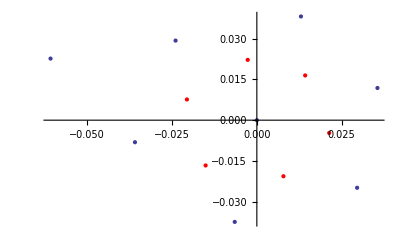

```mathematica
ListPlot[projPts,Epilog->{RGBColor[1,0,0],Map[Point,nbrs]},PlotRange->Automatic]
```

```mathematica
?ToString
```

RowBox[{"ToString", "[", StyleBox["expr", "TI"], "]"}] gives a string corresponding to the printed form of StyleBox["expr", "TI"] in OutputForm. 
RowBox[{"ToString", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["form", "TI"]}], "]"}] gives the string corresponding to output in the specified form.